```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[4order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
(*For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];

];

];
{kglob,fglob}
]
```

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},
(*psis=GeneratePsis[order];*)
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
For[i=1,i≤ nnodes,i++,

ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];

{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[order];
intpts=Length[intrule];
If[order==1,
nnodes=4  ;
];
If[order==2,
nnodes=9;
];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];
Print["elcoords = ",elcoords];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,topol_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];
(*nnodes=Length[allcoords] order;*)
sz= Length[nnodes]2;
If[order==1,
rows=4  ;
];
If[order==2,
rows=9;
];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineNewman[EF_,fx_,order_,nodes_,topol_,id1_,id2_,fxorfy_]:=Block[{k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,vecnodes,iel,vecids={},id={},idy},
iel=Length[topol];
vecnodes={};

If[fxorfy==1,(*fy*)
fi=0;
idy=2;
];
If[fxorfy==0,(*fx*)
fi=-1;
idy=1;
];
If[order==1,
k=4;
];
If[order==2,
k=9;
];

For[j=1,j≤iel,j++,
node={};
id={};
For[i=1,i≤k,i++,
If[nodes[[ topol[[j,i]] ]][[idy]]==nodes[[id1]][[idy]],
AppendTo[node,nodes[[ topol[[j,i]] ]]];
AppendTo[id,topol[[j,i]]];
];
];
If[Length[node]≠0,
node=SortBy[node,Small];
AppendTo[vecnodes,node];
If[order==1,
id=Sort[id,Greater];
];
If[order==2,
id=Sort[id];
id=Sort[id,Greater];
];
AppendTo[vecids,id];
];
];

(*Print["vecnodes = ",vecnodes];
Print["vecids = ",vecids];*)
el=Length[vecnodes];
{elsw,ids}=DefineLineNodes[id1,id2,nodes];
(*Print["ids = ",ids];
Print["iel = ",el];*)

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];
Print["co = ",co];
newco=co;
xx=Sum[shapes[[i]] newco[[i]][[1]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
(*Print["vecids[[i]]= ",vecids[[i]]];
Print["integralxi1= ",integralxi1];*)
If[order==1,
Ef[[ vecids[[i,1]] 2+fi]]+=integralxi1[[1]];
Ef[[ vecids[[i,2]] 2+fi]]+=integralxi1[[2]];
];
If[order==2,
(*Print["vecids[[i,1]] 2 = ",vecids[[i,1]] 2+fi];
Print["vecids[[i,2]] 2 = ",vecids[[i,2]] 2+fi];
Print["vecids[[i,3]] 2 = ",vecids[[i,3]] 2+fi];
Print["integralxi1[[1]]  = ",integralxi1[[1]]];*)
Ef[[vecids[[i,1]] 2+fi]]+=integralxi1[[1]];
Ef[[ vecids[[i,2]] 2+fi]]+=integralxi1[[2]];
Ef[[ vecids[[i,3]] 2+fi]]+=integralxi1[[3]];
];

];
Ef
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_]:=Block[{nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
nels=Length[topol];
sol=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

If[order==1,
kk=4;
];
If[order==2,
kk=9;
];

For[j=1,j≤kk,j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
];

For[j=1,j≤kk,j++,
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] DetJac);
sol[[i,2]]+=(psis[[j]] coefs[[2id]] DetJac);

(*duxdx*)
dsol[[i,1]]+=(D[psis[[j]],xi] coefs[[2 id-1]] DetJac);
(*duxdy*)
dsol[[i,2]]+=(D[psis[[j]],eta] coefs[[2id-1]] DetJac);
(*duydx*)
dsol[[i,3]]+=(D[psis[[j]],xi] coefs[[2id]] DetJac);
(*duydy*)
dsol[[i,4]]+=(D[psis[[j]],eta] coefs[[2id]] DetJac);
(*Print["j+k = ",j+k];
Print["j = ",j];*)
];

];
{sol,dsol}
]
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol2[topol_,coords_,allcoords_,order_,coefs_]:=Block[{iel,els,wpLocal,GradPhi,DetJ,InvJac,elcoords,l,w,intpts,intrule,GradPsi,nnodes,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},


intrule=IntegrationRule[order];
intpts=Length[intrule];
els=Length[allcoords];
sol=Table[0,{els},{2}];
dsol=Table[0,{els},{4}];
For[iel=1,iel≤els,iel++,
elcoords=allcoords[[iel]];
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
{psis,GradPsi,Jac,x,y}=ComputeData[xi,eta,elcoords,order];
nnodes=Length[psis] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
wpLocal=w  DetJ;
For[k=1,k≤nnodes,k++,
id=topol[[iel,k]];
sol[[iel,1]]+=(psis[[k]] coefs[[2 id-1]] DetJ);
sol[[iel,2]]+=(psis[[k]] coefs[[2id]] DetJ);

(*duxdx*)
dsol[[iel,1]]+=(GradPhi[[1,k]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[iel,2]]+=(GradPhi[[2,k]]coefs[[2id-1]]);
(*duydx*)
dsol[[iel,3]]+=(GradPhi[[1,k]] coefs[[2id]] );
(*duydy*)
dsol[[iel,4]]+=(GradPhi[[2,k]] coefs[[2id]] );

];
];
];
];
{sol,dsol}
];
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

eps=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.{ex,ey,exy};
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,eps}
];
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

eps=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.{ex,ey,exy};
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,eps}
];
```

{{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{3,4,1,2,3},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4}}

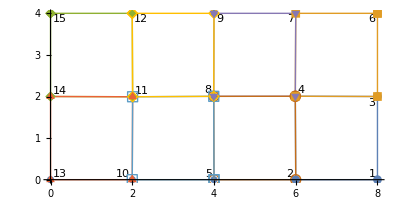

co = {{6,4},{8,4}}

co = {{0,4},{2,4}}

co = {{4,4},{6,4}}

co = {{2,4},{4,4}}

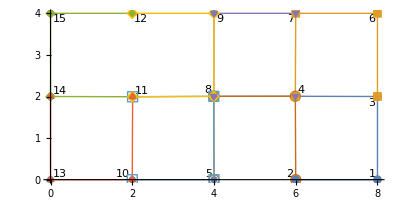

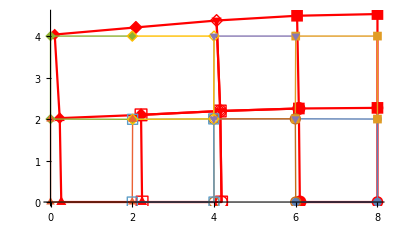

{-6.62581,95.6072,0.415804}

{-5.20215,-81.2283,-1.76351}

{-14.8393,-15.9368,44.8861}

{-12.1328,-14.7371,43.0045}

{-0.609362,-22.1904,-1.11998}

{-2.73153,54.6459,1.60318}

{20.1309,22.0097,-12.3183}

{2.72311,54.4378,2.54528}

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidels-ex1-p1.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\gidnodes-ex1-p1.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListLinePlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=MapThread[Part[#1,#2]&,{allcoords,ord}];
(*or*)
allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,13,1,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,6,{{10^12,1},{1,1}},{0,0}];

q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=-ContributeLineNewman[FE,f,order,nnodes,topol,15,6,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Banded"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]




defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]

solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],30 10^6,0.30][[1]];
stress[[1]]/.{xi->0,eta->0}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}
```

```mathematica
topol
```

{{2,1,3,4},{3,6,7,4},{12,15,14,11},{14,13,10,11},{7,9,8,4},{2,4,8,5},{10,5,8,11},{11,8,9,12}}

```mathematica
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
epsx=sol[[13 2-1]] D[psis[[1]],xi]+sol[[10 2-1]]D[psis[[2]],xi]+sol[[11 2-1]]D[psis[[3]],xi]+sol[[14 2-1]]D[psis[[4]],xi];
epsy=sol[[13 2]] D[psis[[1]],eta]+sol[[10 2]]D[psis[[2]],eta]+sol[[11 2]]D[psis[[3]],eta]+sol[[14 2]]D[psis[[4]],eta];
exy=epsx+epsy;
CC=Table[0,{3},{3}];
CC[[1,1]]=young/(1-nu^2);
CC[[1,2]]=nu young/(1-nu^2);
CC[[2,1]]=CC[[1,2]];
CC[[2,2]]=CC[[1,1]];
CC[[3,3]]=young/(2 (1+nu));
s=CC.{epsx,epsy,exy}/.{xi->0,eta->0}
```

{-0.568417,24.053,6.32276}

{{0,0},{10,0},{10,10},{0,10},{5,0},{10,5},{5,10},{0,5},{5,5}}

{{2,5,9,1,8,9,8,7,3,6,2,9,7}}

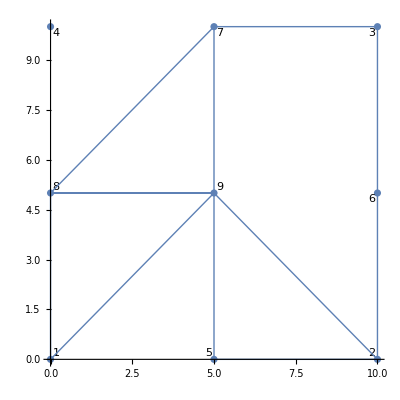

{{6,9,8,4,1,5,2,6,3,7,4}}

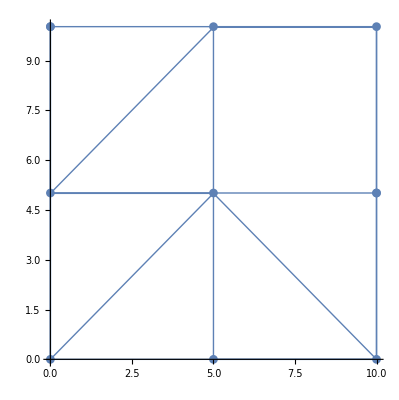

{0,0,0,0,0,0.00001,0,0.00001,0,0,0,5.×10^-6,0,0.00001,0,5.×10^-6,0,5.×10^-6}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
order=2;
young=30 10^6;
nu=0.0;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol={{1,2,3,4,5,6,7,8,9}};
nnodes={{0,0},{10,0},{10,10},{0,10},{5,0},{10,5},{5,10},{0,5},{5,5}}
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,9}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];



undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,2,{{10^12,1},{1,10^12}},{0,0}];

{KE,FE}=ApplyNodeBC[KE,FE,4,1,{{1,1},{1,1}},{0,50}];
{KE,FE}=ApplyNodeBC[KE,FE,7,1,{{1,1},{1,1}},{0,200}];
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{0,50}];

(*q=30;
FE=-ContributeLineNewman[FE,f,order,nnodes,topol,4,3,1];*)

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=2000;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick},PlotMarkers->Automatic];

Show[defplot,undefplot,PlotRange->All]
sol//Chop
KE.sol-FE//Chop
```

```mathematica
(*Clear[x]
nnodes={{0,0},{10,0},{10,10},{0,10},{5,0},{10,5},{5,10},{0,5},{5,5}}
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
{x,y}=Sum[psis[[i]] nnodes[[i]],{i,1,Length[nnodes]}];
grapsi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
J={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJ=Det[J];
graphi=Inverse[J].Transpose[grapsi];
c11=young/(1-nu^2);
c22=c11;
c12=nu young/(1-nu^2);
c33=young/(2 (1+nu));
NIntegrate[DetJ (graphi[[1,1]]c11 graphi[[1,2]]+graphi[[2,1]]c33 graphi[[2,2]]),{xi,-1,1},{eta,-1,1}]
NIntegrate[ DetJ(graphi[[1,1]]c12 graphi[[2,2]]+graphi[[2,1]]c33 graphi[[1,2]]),{xi,-1,1},{eta,-1,1}]
NIntegrate[ DetJ(graphi[[2,1]]c12 graphi[[1,2]]+graphi[[1,1]]c33 graphi[[2,2]]),{xi,-1,1},{eta,-1,1}]*)
```

{{0,0},{10,0},{10,10},{0,10}}

{{2,1,4,3,2}}

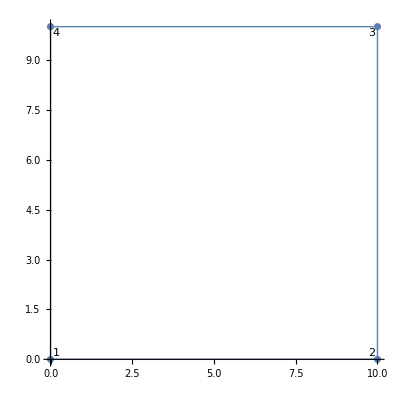

{{2,1,4,3,2}}

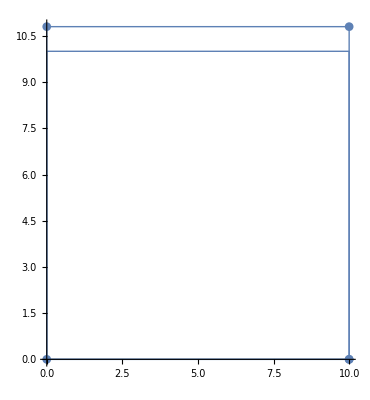

{0,0,0,0,0,0,0,0}

```mathematica
order=1;
young=30 10^6;
nu=0.;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol={{1,2,3,4}};
nnodes={{0,0},{10,0},{10,10},{0,10}}
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];



undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,2,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,4,1,{{1,1},{1,1}},{0,150}];
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{0,150}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=80000;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick},PlotMarkers->Automatic];

Show[defplot,undefplot,PlotRange->All]

KE.sol-FE//Chop
```

```mathematica
allcoordsNEW
```

{{{10.,8.×10^-13},{-3.78956×10^-29,8.×10^-13},{-1.89478×10^-16,10.8},{10.,10.8},{10.,8.×10^-13}}}

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{4,7,3,6,2,5,1,8,4}}

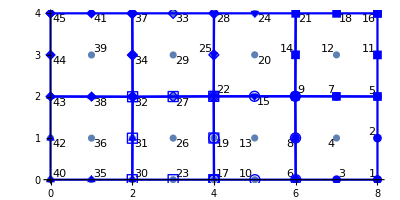

co = {{6,4},{7,4},{8,4}}

co = {{0,4},{1,4},{2,4}}

co = {{4,4},{5,4},{6,4}}

co = {{2,4},{3,4},{4,4}}

{{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{1,5,2,6,3,7,4,8,1},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5},{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{5,2,6,3,7,4,8,1,5}}

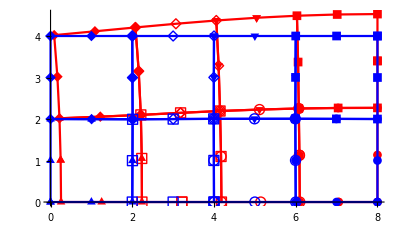

{-6.83805,97.0839,0.337054}

{-4.68528,-82.2585,-1.29114}

{-15.2448,-16.0284,45.863}

{-12.733,-14.8594,43.7498}

{-0.798232,-20.4163,-1.21909}

{-3.12441,54.8437,1.43973}

{20.5082,22.4026,-11.4797}

{2.66348,55.1483,1.8376}

```mathematica
order=2;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp2els9nodes.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp2nodes9nodes.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,9}];

allcoords2=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords2//Flatten[#,1]&

allcoordsNEW=Table[allcoords2[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],PlotMarkers->Automatic,AspectRatio->Automatic,PlotStyle->{Blue}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,40,1,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,16,{{10^12,1},{1,1}},{0,0}];

fE=FE;

(*{KE,FE}=ApplyNodeBC[KE,FE,16,1,{{1,1},{1,1}},{0,33.53}];
{KE,FE}=ApplyNodeBC[KE,FE,18,1,{{1,1},{1,1}},{0,130.26}];
{KE,FE}=ApplyNodeBC[KE,FE,21,1,{{1,1},{1,1}},{0,62.06}];
{KE,FE}=ApplyNodeBC[KE,FE,24,1,{{1,1},{1,1}},{0,110.43}];
{KE,FE}=ApplyNodeBC[KE,FE,28,1,{{1,1},{1,1}},{0,47.49}];
{KE,FE}=ApplyNodeBC[KE,FE,33,1,{{1,1},{1,1}},{0,73.79}];
{KE,FE}=ApplyNodeBC[KE,FE,37,1,{{1,1},{1,1}},{0,25.7}];
{KE,FE}=ApplyNodeBC[KE,FE,41,1,{{1,1},{1,1}},{0,25.9}];
{KE,FE}=ApplyNodeBC[KE,FE,45,1,{{1,1},{1,1}},{0,0.033}];*)

q=100;
L=16;
f[x_]:=q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,topol,45,16,1];


sol=LinearSolve[KE,FE,Method->"Banded"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],PlotMarkers->Automatic,AspectRatio->Automatic,PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]

solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],30 10^6,0.30][[1]];
stress[[1]]/.{xi->0,eta->0}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}
```

```mathematica
{sol,dsol}=ComputeSol2[topol,nnodes,allcoords,order,sol]
```

Part::partw: Part 11 of {«1»} does not exist.

Part::partw: Part 12 of {«1»} does not exist.

GradPhi[[1,k]] = 0.0289075

Part::partw: Part 11 of {«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

GradPhi[[1,k]] = 0.0087088

GradPhi[[1,k]] = -0.431188

GradPhi[[1,k]] = -1.36391

GradPhi[[1,k]] = -0.03634

GradPhi[[1,k]] = -0.0355533

GradPhi[[1,k]] = 1.79914

GradPhi[[1,k]] = -0.118129

GradPhi[[1,k]] = 0.148357

GradPhi[[1,k]] = 0.0255154

GradPhi[[1,k]] = 0.00552529

GradPhi[[1,k]] = -0.278188

GradPhi[[1,k]] = -1.21157

GradPhi[[1,k]] = -0.0297641

GradPhi[[1,k]] = -0.0225488

GradPhi[[1,k]] = 1.49381

GradPhi[[1,k]] = -0.104254

GradPhi[[1,k]] = 0.121476

GradPhi[[1,k]] = 0.0199694

GradPhi[[1,k]] = 0.000325208

GradPhi[[1,k]] = -0.0244189

GradPhi[[1,k]] = -0.958894

GradPhi[[1,k]] = -0.0190175

GradPhi[[1,k]] = -0.00131342

GradPhi[[1,k]] = 0.987365

GradPhi[[1,k]] = -0.0815753

GradPhi[[1,k]] = 0.07756

GradPhi[[1,k]] = 0.0131055

GradPhi[[1,k]] = -0.00610189

GradPhi[[1,k]] = 0.296192

GradPhi[[1,k]] = -0.639667

GradPhi[[1,k]] = -0.0057259

GradPhi[[1,k]] = 0.0249208

GradPhi[[1,k]] = 0.347528

GradPhi[[1,k]] = -0.0535184

GradPhi[[1,k]] = 0.0232662

GradPhi[[1,k]] = 0.00591044

GradPhi[[1,k]] = -0.012828

GradPhi[[1,k]] = 0.640545

GradPhi[[1,k]] = -0.296799

GradPhi[[1,k]] = 0.00819596

GradPhi[[1,k]] = 0.0523606

GradPhi[[1,k]] = -0.339691

GradPhi[[1,k]] = -0.024122

GradPhi[[1,k]] = -0.0335727

GradPhi[[1,k]] = -0.000643882

GradPhi[[1,k]] = -0.0189447

GradPhi[[1,k]] = 0.962138

GradPhi[[1,k]] = 0.0234077

GradPhi[[1,k]] = 0.0208675

GradPhi[[1,k]] = 0.0772994

GradPhi[[1,k]] = -0.981488

GradPhi[[1,k]] = 0.00264311

GradPhi[[1,k]] = -0.0852791

GradPhi[[1,k]] = -0.00573225

GradPhi[[1,k]] = -0.0236858

GradPhi[[1,k]] = 1.21736

GradPhi[[1,k]] = 0.277528

GradPhi[[1,k]] = 0.0306976

GradPhi[[1,k]] = 0.0966199

GradPhi[[1,k]] = -1.49083

GradPhi[[1,k]] = 0.0234124

GradPhi[[1,k]] = -0.125371

GradPhi[[1,k]] = -0.00875742

GradPhi[[1,k]] = -0.0265013

GradPhi[[1,k]] = 1.37152

GradPhi[[1,k]] = 0.431028

GradPhi[[1,k]] = 0.0365385

GradPhi[[1,k]] = 0.108089

GradPhi[[1,k]] = -1.79849

GradPhi[[1,k]] = 0.0357561

GradPhi[[1,k]] = -0.149185

GradPhi[[1,k]] = 0.118454

GradPhi[[1,k]] = 0.0370989

GradPhi[[1,k]] = -0.327998

GradPhi[[1,k]] = -1.03729

GradPhi[[1,k]] = -0.154798

GradPhi[[1,k]] = -0.167321

GradPhi[[1,k]] = 1.36858

GradPhi[[1,k]] = -0.534891

GradPhi[[1,k]] = 0.698161

GradPhi[[1,k]] = 0.10509

GradPhi[[1,k]] = 0.0238592

GradPhi[[1,k]] = -0.211628

GradPhi[[1,k]] = -0.921454

GradPhi[[1,k]] = -0.128195

GradPhi[[1,k]] = -0.107563

GradPhi[[1,k]] = 1.13638

GradPhi[[1,k]] = -0.474471

GradPhi[[1,k]] = 0.577982

GradPhi[[1,k]] = 0.0829913

GradPhi[[1,k]] = 0.00196459

GradPhi[[1,k]] = -0.0186019

GradPhi[[1,k]] = -0.72932

GradPhi[[1,k]] = -0.0842012

GradPhi[[1,k]] = -0.00878024

GradPhi[[1,k]] = 0.751221

GradPhi[[1,k]] = -0.374589

GradPhi[[1,k]] = 0.379316

GradPhi[[1,k]] = 0.0551872

GradPhi[[1,k]] = -0.0255812

GradPhi[[1,k]] = 0.22529

GradPhi[[1,k]] = -0.486555

GradPhi[[1,k]] = -0.028851

GradPhi[[1,k]] = 0.115432

GradPhi[[1,k]] = 0.264565

GradPhi[[1,k]] = -0.24899

GradPhi[[1,k]] = 0.129503

GradPhi[[1,k]] = 0.025468

GradPhi[[1,k]] = -0.0550231

GradPhi[[1,k]] = 0.487271

GradPhi[[1,k]] = -0.225784

GradPhi[[1,k]] = 0.0303106

GradPhi[[1,k]] = 0.248109

GradPhi[[1,k]] = -0.258185

GradPhi[[1,k]] = -0.114824

GradPhi[[1,k]] = -0.137343

GradPhi[[1,k]] = -0.0021529

GradPhi[[1,k]] = -0.0823852

GradPhi[[1,k]] = 0.731962

GradPhi[[1,k]] = 0.0177786

GradPhi[[1,k]] = 0.085294

GradPhi[[1,k]] = 0.371335

GradPhi[[1,k]] = -0.746437

GradPhi[[1,k]] = 0.00979165

GradPhi[[1,k]] = -0.385186

GradPhi[[1,k]] = -0.0239813

GradPhi[[1,k]] = -0.104008

GradPhi[[1,k]] = 0.92617

GradPhi[[1,k]] = 0.211091

GradPhi[[1,k]] = 0.128746

GradPhi[[1,k]] = 0.46866

GradPhi[[1,k]] = -1.13396

GradPhi[[1,k]] = 0.108219

GradPhi[[1,k]] = -0.58094

GradPhi[[1,k]] = -0.0371273

GradPhi[[1,k]] = -0.11703

GradPhi[[1,k]] = 1.04349

GradPhi[[1,k]] = 0.327868

GradPhi[[1,k]] = 0.154914

GradPhi[[1,k]] = 0.527248

GradPhi[[1,k]] = -1.36805

GradPhi[[1,k]] = 0.167474

GradPhi[[1,k]] = -0.698784

GradPhi[[1,k]] = 0.181417

GradPhi[[1,k]] = 0.0571659

GradPhi[[1,k]] = -0.183848

GradPhi[[1,k]] = -0.581048

GradPhi[[1,k]] = -0.238527

GradPhi[[1,k]] = -0.331849

GradPhi[[1,k]] = 0.767112

GradPhi[[1,k]] = -1.05508

GradPhi[[1,k]] = 1.38466

GradPhi[[1,k]] = 0.161082

GradPhi[[1,k]] = 0.0368408

GradPhi[[1,k]] = -0.118646

GradPhi[[1,k]] = -0.516207

GradPhi[[1,k]] = -0.197868

GradPhi[[1,k]] = -0.213727

GradPhi[[1,k]] = 0.63707

GradPhi[[1,k]] = -0.936586

GradPhi[[1,k]] = 1.14804

GradPhi[[1,k]] = 0.127391

GradPhi[[1,k]] = 0.00316418

GradPhi[[1,k]] = -0.0104721

GradPhi[[1,k]] = -0.408633

GradPhi[[1,k]] = -0.1305

GradPhi[[1,k]] = -0.0181269

GradPhi[[1,k]] = 0.421322

GradPhi[[1,k]] = -0.740369

GradPhi[[1,k]] = 0.756224

GradPhi[[1,k]] = 0.0848867

GradPhi[[1,k]] = -0.0393207

GradPhi[[1,k]] = 0.126246

GradPhi[[1,k]] = -0.272672

GradPhi[[1,k]] = -0.0455108

GradPhi[[1,k]] = 0.228429

GradPhi[[1,k]] = 0.148643

GradPhi[[1,k]] = -0.493035

GradPhi[[1,k]] = 0.262334

GradPhi[[1,k]] = 0.0393123

GradPhi[[1,k]] = -0.0848745

GradPhi[[1,k]] = 0.273153

GradPhi[[1,k]] = -0.126578

GradPhi[[1,k]] = 0.0456174

GradPhi[[1,k]] = 0.492541

GradPhi[[1,k]] = -0.144356

GradPhi[[1,k]] = -0.228088

GradPhi[[1,k]] = -0.266727

GradPhi[[1,k]] = -0.00317793

GradPhi[[1,k]] = -0.127346

GradPhi[[1,k]] = 0.410409

GradPhi[[1,k]] = 0.00991891

GradPhi[[1,k]] = 0.130579

GradPhi[[1,k]] = 0.738542

GradPhi[[1,k]] = -0.418108

GradPhi[[1,k]] = 0.0186937

GradPhi[[1,k]] = -0.759511

GradPhi[[1,k]] = -0.0368494

GradPhi[[1,k]] = -0.161002

GradPhi[[1,k]] = 0.519378

GradPhi[[1,k]] = 0.118286

GradPhi[[1,k]] = 0.197907

GradPhi[[1,k]] = 0.933324

GradPhi[[1,k]] = -0.635443

GradPhi[[1,k]] = 0.214094

GradPhi[[1,k]] = -1.14969

GradPhi[[1,k]] = -0.0571674

GradPhi[[1,k]] = -0.181311

GradPhi[[1,k]] = 0.585218

GradPhi[[1,k]] = 0.183762

GradPhi[[1,k]] = 0.238533

GradPhi[[1,k]] = 1.05079

GradPhi[[1,k]] = -0.766758

GradPhi[[1,k]] = 0.331932

GradPhi[[1,k]] = -1.385

GradPhi[[1,k]] = 0.108542

GradPhi[[1,k]] = 0.0343804

GradPhi[[1,k]] = -0.0498342

GradPhi[[1,k]] = -0.156953

GradPhi[[1,k]] = -0.143453

GradPhi[[1,k]] = -0.443471

GradPhi[[1,k]] = 0.207933

GradPhi[[1,k]] = -1.40755

GradPhi[[1,k]] = 1.8504

GradPhi[[1,k]] = 0.0964433

GradPhi[[1,k]] = 0.0221954

GradPhi[[1,k]] = -0.0321979

GradPhi[[1,k]] = -0.139504

GradPhi[[1,k]] = -0.11917

GradPhi[[1,k]] = -0.285784

GradPhi[[1,k]] = 0.172848

GradPhi[[1,k]] = -1.24976

GradPhi[[1,k]] = 1.53493

GradPhi[[1,k]] = 0.0763645

GradPhi[[1,k]] = 0.00197276

GradPhi[[1,k]] = -0.0029061

GradPhi[[1,k]] = -0.110523

GradPhi[[1,k]] = -0.0788685

GradPhi[[1,k]] = -0.0245233

GradPhi[[1,k]] = 0.114576

GradPhi[[1,k]] = -0.98833

GradPhi[[1,k]] = 1.01224

GradPhi[[1,k]] = 0.0509749

GradPhi[[1,k]] = -0.0235984

GradPhi[[1,k]] = 0.0341725

GradPhi[[1,k]] = -0.0738362

GradPhi[[1,k]] = -0.0279081

GradPhi[[1,k]] = 0.305051

GradPhi[[1,k]] = 0.0408112

GradPhi[[1,k]] = -0.658544

GradPhi[[1,k]] = 0.352877

GradPhi[[1,k]] = 0.023678

GradPhi[[1,k]] = -0.0510902

GradPhi[[1,k]] = 0.0740852

GradPhi[[1,k]] = -0.0343444

GradPhi[[1,k]] = 0.0268805

GradPhi[[1,k]] = 0.658409

GradPhi[[1,k]] = -0.0385927

GradPhi[[1,k]] = -0.304958

GradPhi[[1,k]] = -0.354067

GradPhi[[1,k]] = -0.00184018

GradPhi[[1,k]] = -0.0767904

GradPhi[[1,k]] = 0.111442

GradPhi[[1,k]] = 0.00261987

GradPhi[[1,k]] = 0.0780985

GradPhi[[1,k]] = 0.987832

GradPhi[[1,k]] = -0.112914

GradPhi[[1,k]] = 0.0246768

GradPhi[[1,k]] = -1.01313

GradPhi[[1,k]] = -0.0221091

GradPhi[[1,k]] = -0.0972036

GradPhi[[1,k]] = 0.141146

GradPhi[[1,k]] = 0.0320118

GradPhi[[1,k]] = 0.11878

GradPhi[[1,k]] = 1.24887

GradPhi[[1,k]] = -0.172009

GradPhi[[1,k]] = 0.285882

GradPhi[[1,k]] = -1.53537

GradPhi[[1,k]] = -0.0343599

GradPhi[[1,k]] = -0.109542

GradPhi[[1,k]] = 0.159112

GradPhi[[1,k]] = 0.04979

GradPhi[[1,k]] = 0.143369

GradPhi[[1,k]] = 1.40638

GradPhi[[1,k]] = -0.207753

GradPhi[[1,k]] = 0.443491

GradPhi[[1,k]] = -1.85048

GradPhi[[1,k]] = -0.158922

GradPhi[[1,k]] = -0.0498431

GradPhi[[1,k]] = 0.034395

GradPhi[[1,k]] = 0.109487

GradPhi[[1,k]] = 0.207974

GradPhi[[1,k]] = -0.443899

GradPhi[[1,k]] = -0.143515

GradPhi[[1,k]] = -1.40786

GradPhi[[1,k]] = 1.85219

GradPhi[[1,k]] = -0.14102

GradPhi[[1,k]] = -0.0320705

GradPhi[[1,k]] = 0.0221431

GradPhi[[1,k]] = 0.097175

GradPhi[[1,k]] = 0.172299

GradPhi[[1,k]] = -0.286131

GradPhi[[1,k]] = -0.118951

GradPhi[[1,k]] = -1.25016

GradPhi[[1,k]] = 1.53672

GradPhi[[1,k]] = -0.111402

GradPhi[[1,k]] = -0.00266688

GradPhi[[1,k]] = 0.00186254

GradPhi[[1,k]] = 0.076795

GradPhi[[1,k]] = 0.113277

GradPhi[[1,k]] = -0.0246757

GradPhi[[1,k]] = -0.0782907

GradPhi[[1,k]] = -0.988823

GradPhi[[1,k]] = 1.01392

GradPhi[[1,k]] = -0.0741149

GradPhi[[1,k]] = 0.0343494

GradPhi[[1,k]] = -0.0236875

GradPhi[[1,k]] = 0.0511195

GradPhi[[1,k]] = 0.038973

GradPhi[[1,k]] = 0.305254

GradPhi[[1,k]] = -0.0270649

GradPhi[[1,k]] = -0.659038

GradPhi[[1,k]] = 0.354209

GradPhi[[1,k]] = -0.0342306

GradPhi[[1,k]] = 0.0739427

GradPhi[[1,k]] = -0.0510397

GradPhi[[1,k]] = 0.0236324

GradPhi[[1,k]] = -0.0405051

GradPhi[[1,k]] = 0.659129

GradPhi[[1,k]] = 0.0277746

GradPhi[[1,k]] = -0.305318

GradPhi[[1,k]] = -0.353386

GradPhi[[1,k]] = 0.00286454

GradPhi[[1,k]] = 0.110766

GradPhi[[1,k]] = -0.0765004

GradPhi[[1,k]] = -0.00195409

GradPhi[[1,k]] = -0.114424

GradPhi[[1,k]] = 0.989161

GradPhi[[1,k]] = 0.078822

GradPhi[[1,k]] = 0.0245695

GradPhi[[1,k]] = -1.0133

GradPhi[[1,k]] = 0.0321988

GradPhi[[1,k]] = 0.139885

GradPhi[[1,k]] = -0.096649

GradPhi[[1,k]] = -0.0222024

GradPhi[[1,k]] = -0.172877

GradPhi[[1,k]] = 1.25077

GradPhi[[1,k]] = 0.119219

GradPhi[[1,k]] = 0.286061

GradPhi[[1,k]] = -1.5364

GradPhi[[1,k]] = 0.049873

GradPhi[[1,k]] = 0.157429

GradPhi[[1,k]] = -0.108795

GradPhi[[1,k]] = -0.0344088

GradPhi[[1,k]] = -0.208096

GradPhi[[1,k]] = 1.40866

GradPhi[[1,k]] = 0.143571

GradPhi[[1,k]] = 0.44388

GradPhi[[1,k]] = -1.85211

GradPhi[[1,k]] = -0.585322

GradPhi[[1,k]] = -0.184278

GradPhi[[1,k]] = 0.0573182

GradPhi[[1,k]] = 0.181827

GradPhi[[1,k]] = 0.768909

GradPhi[[1,k]] = -0.332782

GradPhi[[1,k]] = -0.239163

GradPhi[[1,k]] = -1.05506

GradPhi[[1,k]] = 1.38854

GradPhi[[1,k]] = -0.519655

GradPhi[[1,k]] = -0.118724

GradPhi[[1,k]] = 0.0369439

GradPhi[[1,k]] = 0.161456

GradPhi[[1,k]] = 0.637687

GradPhi[[1,k]] = -0.214533

GradPhi[[1,k]] = -0.198417

GradPhi[[1,k]] = -0.936922

GradPhi[[1,k]] = 1.15216

GradPhi[[1,k]] = -0.41088

GradPhi[[1,k]] = -0.0101365

GradPhi[[1,k]] = 0.00318158

GradPhi[[1,k]] = 0.127698

GradPhi[[1,k]] = 0.420326

GradPhi[[1,k]] = -0.0185471

GradPhi[[1,k]] = -0.130897

GradPhi[[1,k]] = -0.741128

GradPhi[[1,k]] = 0.760383

GradPhi[[1,k]] = -0.273709

GradPhi[[1,k]] = 0.126798

GradPhi[[1,k]] = -0.0394191

GradPhi[[1,k]] = 0.0851031

GradPhi[[1,k]] = 0.146219

GradPhi[[1,k]] = 0.228809

GradPhi[[1,k]] = -0.0457012

GradPhi[[1,k]] = -0.494014

GradPhi[[1,k]] = 0.265914

GradPhi[[1,k]] = -0.126695

GradPhi[[1,k]] = 0.273558

GradPhi[[1,k]] = -0.0851068

GradPhi[[1,k]] = 0.0394217

GradPhi[[1,k]] = -0.147556

GradPhi[[1,k]] = 0.494167

GradPhi[[1,k]] = 0.0456678

GradPhi[[1,k]] = -0.228915

GradPhi[[1,k]] = -0.264544

GradPhi[[1,k]] = 0.010309

GradPhi[[1,k]] = 0.410325

GradPhi[[1,k]] = -0.127712

GradPhi[[1,k]] = -0.00317728

GradPhi[[1,k]] = -0.421326

GradPhi[[1,k]] = 0.741695

GradPhi[[1,k]] = 0.130872

GradPhi[[1,k]] = 0.0183702

GradPhi[[1,k]] = -0.759355

GradPhi[[1,k]] = 0.118835

GradPhi[[1,k]] = 0.518663

GradPhi[[1,k]] = -0.16148

GradPhi[[1,k]] = -0.036941

GradPhi[[1,k]] = -0.638191

GradPhi[[1,k]] = 0.937935

GradPhi[[1,k]] = 0.198404

GradPhi[[1,k]] = 0.214418

GradPhi[[1,k]] = -1.15164

GradPhi[[1,k]] = 0.184304

GradPhi[[1,k]] = 0.584018

GradPhi[[1,k]] = -0.181859

GradPhi[[1,k]] = -0.0573173

GradPhi[[1,k]] = -0.769015

GradPhi[[1,k]] = 1.05639

GradPhi[[1,k]] = 0.239159

GradPhi[[1,k]] = 0.332753

GradPhi[[1,k]] = -1.38843

GradPhi[[1,k]] = -1.04491

GradPhi[[1,k]] = -0.329241

GradPhi[[1,k]] = 0.0372635

GradPhi[[1,k]] = 0.118134

GradPhi[[1,k]] = 1.37377

GradPhi[[1,k]] = -0.168077

GradPhi[[1,k]] = -0.155484

GradPhi[[1,k]] = -0.532771

GradPhi[[1,k]] = 0.701308

GradPhi[[1,k]] = -0.927782

GradPhi[[1,k]] = -0.212177

GradPhi[[1,k]] = 0.024023

GradPhi[[1,k]] = 0.104908

GradPhi[[1,k]] = 1.13958

GradPhi[[1,k]] = -0.108361

GradPhi[[1,k]] = -0.129017

GradPhi[[1,k]] = -0.47313

GradPhi[[1,k]] = 0.581951

GradPhi[[1,k]] = -0.73372

GradPhi[[1,k]] = -0.0182168

GradPhi[[1,k]] = 0.00207762

GradPhi[[1,k]] = 0.0829856

GradPhi[[1,k]] = 0.751562

GradPhi[[1,k]] = -0.00938022

GradPhi[[1,k]] = -0.085149

GradPhi[[1,k]] = -0.374274

GradPhi[[1,k]] = 0.384115

GradPhi[[1,k]] = -0.488906

GradPhi[[1,k]] = 0.226469

GradPhi[[1,k]] = -0.0256205

GradPhi[[1,k]] = 0.0553168

GradPhi[[1,k]] = 0.262061

GradPhi[[1,k]] = 0.115555

GradPhi[[1,k]] = -0.0297821

GradPhi[[1,k]] = -0.249496

GradPhi[[1,k]] = 0.134402

GradPhi[[1,k]] = -0.226413

GradPhi[[1,k]] = 0.488824

GradPhi[[1,k]] = -0.0553354

GradPhi[[1,k]] = 0.0256334

GradPhi[[1,k]] = -0.262786

GradPhi[[1,k]] = 0.249596

GradPhi[[1,k]] = 0.0296162

GradPhi[[1,k]] = -0.115624

GradPhi[[1,k]] = -0.133511

GradPhi[[1,k]] = 0.0183103

GradPhi[[1,k]] = 0.733419

GradPhi[[1,k]] = -0.0830544

GradPhi[[1,k]] = -0.00205622

GradPhi[[1,k]] = -0.752104

GradPhi[[1,k]] = 0.374643

GradPhi[[1,k]] = 0.0850247

GradPhi[[1,k]] = 0.00926528

GradPhi[[1,k]] = -0.383447

GradPhi[[1,k]] = 0.212238

GradPhi[[1,k]] = 0.927244

GradPhi[[1,k]] = -0.105031

GradPhi[[1,k]] = -0.0240091

GradPhi[[1,k]] = -1.13986

GradPhi[[1,k]] = 0.473789

GradPhi[[1,k]] = 0.128954

GradPhi[[1,k]] = 0.108286

GradPhi[[1,k]] = -0.581614

GradPhi[[1,k]] = 0.329255

GradPhi[[1,k]] = 1.0442

GradPhi[[1,k]] = -0.118296

GradPhi[[1,k]] = -0.0372602

GradPhi[[1,k]] = -1.37383

GradPhi[[1,k]] = 0.533638

GradPhi[[1,k]] = 0.15547

GradPhi[[1,k]] = 0.168059

GradPhi[[1,k]] = -0.701236

GradPhi[[1,k]] = -1.3744

GradPhi[[1,k]] = -0.433191

GradPhi[[1,k]] = 0.00877579

GradPhi[[1,k]] = 0.0278156

GradPhi[[1,k]] = 1.80751

GradPhi[[1,k]] = -0.035829

GradPhi[[1,k]] = -0.0366173

GradPhi[[1,k]] = -0.113561

GradPhi[[1,k]] = 0.149498

GradPhi[[1,k]] = -1.22039

GradPhi[[1,k]] = -0.279195

GradPhi[[1,k]] = 0.00565797

GradPhi[[1,k]] = 0.024702

GradPhi[[1,k]] = 1.4995

GradPhi[[1,k]] = -0.0231

GradPhi[[1,k]] = -0.0303859

GradPhi[[1,k]] = -0.100849

GradPhi[[1,k]] = 0.124058

GradPhi[[1,k]] = -0.965192

GradPhi[[1,k]] = -0.024019

GradPhi[[1,k]] = 0.000490009

GradPhi[[1,k]] = 0.0195411

GradPhi[[1,k]] = 0.989128

GradPhi[[1,k]] = -0.00200085

GradPhi[[1,k]] = -0.0200571

GradPhi[[1,k]] = -0.0797795

GradPhi[[1,k]] = 0.0818888

GradPhi[[1,k]] = -0.643209

GradPhi[[1,k]] = 0.297935

GradPhi[[1,k]] = -0.00603328

GradPhi[[1,k]] = 0.0130267

GradPhi[[1,k]] = 0.345192

GradPhi[[1,k]] = 0.0246319

GradPhi[[1,k]] = -0.00701939

GradPhi[[1,k]] = -0.0531838

GradPhi[[1,k]] = 0.0286604

GradPhi[[1,k]] = -0.297923

GradPhi[[1,k]] = 0.643191

GradPhi[[1,k]] = -0.0130323

GradPhi[[1,k]] = 0.00603718

GradPhi[[1,k]] = -0.345351

GradPhi[[1,k]] = 0.0532073

GradPhi[[1,k]] = 0.00696911

GradPhi[[1,k]] = -0.0246482

GradPhi[[1,k]] = -0.0284506

GradPhi[[1,k]] = 0.0240396

GradPhi[[1,k]] = 0.965125

GradPhi[[1,k]] = -0.0195619

GradPhi[[1,k]] = -0.000483522

GradPhi[[1,k]] = -0.989247

GradPhi[[1,k]] = 0.0798665

GradPhi[[1,k]] = 0.0200194

GradPhi[[1,k]] = 0.00197379

GradPhi[[1,k]] = -0.0817316

GradPhi[[1,k]] = 0.279208

GradPhi[[1,k]] = 1.22027

GradPhi[[1,k]] = -0.0247392

GradPhi[[1,k]] = -0.00565375

GradPhi[[1,k]] = -1.49956

GradPhi[[1,k]] = 0.101005

GradPhi[[1,k]] = 0.0303669

GradPhi[[1,k]] = 0.0230824

GradPhi[[1,k]] = -0.123978

GradPhi[[1,k]] = 0.433194

GradPhi[[1,k]] = 1.37424

GradPhi[[1,k]] = -0.0278645

GradPhi[[1,k]] = -0.0087748

GradPhi[[1,k]] = -1.80752

GradPhi[[1,k]] = 0.113765

GradPhi[[1,k]] = 0.0366133

GradPhi[[1,k]] = 0.0358249

GradPhi[[1,k]] = -0.149481

GradPhi[[1,k]] = -0.431021

GradPhi[[1,k]] = 0.00875737

GradPhi[[1,k]] = 0.0264975

GradPhi[[1,k]] = -1.37151

GradPhi[[1,k]] = -0.0357559

GradPhi[[1,k]] = -0.0365383

GradPhi[[1,k]] = -0.108073

GradPhi[[1,k]] = 1.79846

GradPhi[[1,k]] = 0.149184

GradPhi[[1,k]] = -0.327864

GradPhi[[1,k]] = 0.0371268

GradPhi[[1,k]] = 0.117027

GradPhi[[1,k]] = -1.04348

GradPhi[[1,k]] = -0.167472

GradPhi[[1,k]] = -0.154912

GradPhi[[1,k]] = -0.527231

GradPhi[[1,k]] = 1.36803

GradPhi[[1,k]] = 0.698776

GradPhi[[1,k]] = -0.18376

GradPhi[[1,k]] = 0.0571668

GradPhi[[1,k]] = 0.181309

GradPhi[[1,k]] = -0.585217

GradPhi[[1,k]] = -0.331929

GradPhi[[1,k]] = -0.238531

GradPhi[[1,k]] = -1.05077

GradPhi[[1,k]] = 0.766749

GradPhi[[1,k]] = 1.38498

GradPhi[[1,k]] = -0.0497895

GradPhi[[1,k]] = 0.0343596

GradPhi[[1,k]] = 0.109542

GradPhi[[1,k]] = -0.159114

GradPhi[[1,k]] = -0.443487

GradPhi[[1,k]] = -0.143368

GradPhi[[1,k]] = -1.40636

GradPhi[[1,k]] = 0.207751

GradPhi[[1,k]] = 1.85047

GradPhi[[1,k]] = 0.0344086

GradPhi[[1,k]] = -0.0498728

GradPhi[[1,k]] = -0.157426

GradPhi[[1,k]] = 0.108793

GradPhi[[1,k]] = -0.443877

GradPhi[[1,k]] = 0.208095

GradPhi[[1,k]] = -1.40865

GradPhi[[1,k]] = -0.143571

GradPhi[[1,k]] = 1.8521

GradPhi[[1,k]] = 0.0573171

GradPhi[[1,k]] = -0.184303

GradPhi[[1,k]] = -0.584014

GradPhi[[1,k]] = 0.181858

GradPhi[[1,k]] = -0.332752

GradPhi[[1,k]] = 0.769012

GradPhi[[1,k]] = -1.05638

GradPhi[[1,k]] = -0.239158

GradPhi[[1,k]] = 1.38842

GradPhi[[1,k]] = 0.0372601

GradPhi[[1,k]] = -0.329254

GradPhi[[1,k]] = -1.0442

GradPhi[[1,k]] = 0.118296

GradPhi[[1,k]] = -0.168059

GradPhi[[1,k]] = 1.37383

GradPhi[[1,k]] = -0.533638

GradPhi[[1,k]] = -0.15547

GradPhi[[1,k]] = 0.701235

GradPhi[[1,k]] = 0.00877479

GradPhi[[1,k]] = -0.433194

GradPhi[[1,k]] = -1.37424

GradPhi[[1,k]] = 0.0278646

GradPhi[[1,k]] = -0.0358248

GradPhi[[1,k]] = 1.80752

GradPhi[[1,k]] = -0.113765

GradPhi[[1,k]] = -0.0366133

GradPhi[[1,k]] = 0.149481

GradPhi[[1,k]] = -0.277523

GradPhi[[1,k]] = 0.00573247

GradPhi[[1,k]] = 0.0236829

GradPhi[[1,k]] = -1.21735

GradPhi[[1,k]] = -0.0234133

GradPhi[[1,k]] = -0.0306985

GradPhi[[1,k]] = -0.0966076

GradPhi[[1,k]] = 1.4908

GradPhi[[1,k]] = 0.125375

GradPhi[[1,k]] = -0.211088

GradPhi[[1,k]] = 0.0239812

GradPhi[[1,k]] = 0.104005

GradPhi[[1,k]] = -0.926165

GradPhi[[1,k]] = -0.108219

GradPhi[[1,k]] = -0.128745

GradPhi[[1,k]] = -0.468645

GradPhi[[1,k]] = 1.13394

GradPhi[[1,k]] = 0.580937

GradPhi[[1,k]] = -0.118284

GradPhi[[1,k]] = 0.036849

GradPhi[[1,k]] = 0.161

GradPhi[[1,k]] = -0.519377

GradPhi[[1,k]] = -0.214092

GradPhi[[1,k]] = -0.197905

GradPhi[[1,k]] = -0.933309

GradPhi[[1,k]] = 0.635434

GradPhi[[1,k]] = 1.14968

GradPhi[[1,k]] = -0.0320112

GradPhi[[1,k]] = 0.0221088

GradPhi[[1,k]] = 0.0972039

GradPhi[[1,k]] = -0.141147

GradPhi[[1,k]] = -0.285879

GradPhi[[1,k]] = -0.118779

GradPhi[[1,k]] = -1.24886

GradPhi[[1,k]] = 0.172006

GradPhi[[1,k]] = 1.53535

GradPhi[[1,k]] = 0.0222024

GradPhi[[1,k]] = -0.0321988

GradPhi[[1,k]] = -0.139883

GradPhi[[1,k]] = 0.0966476

GradPhi[[1,k]] = -0.286059

GradPhi[[1,k]] = 0.172877

GradPhi[[1,k]] = -1.25076

GradPhi[[1,k]] = -0.119219

GradPhi[[1,k]] = 1.53639

GradPhi[[1,k]] = 0.0369409

GradPhi[[1,k]] = -0.118835

GradPhi[[1,k]] = -0.51866

GradPhi[[1,k]] = 0.161479

GradPhi[[1,k]] = -0.214417

GradPhi[[1,k]] = 0.63819

GradPhi[[1,k]] = -0.937933

GradPhi[[1,k]] = -0.198403

GradPhi[[1,k]] = 1.15164

GradPhi[[1,k]] = 0.024009

GradPhi[[1,k]] = -0.212237

GradPhi[[1,k]] = -0.927242

GradPhi[[1,k]] = 0.105031

GradPhi[[1,k]] = -0.108286

GradPhi[[1,k]] = 1.13986

GradPhi[[1,k]] = -0.473789

GradPhi[[1,k]] = -0.128953

GradPhi[[1,k]] = 0.581612

GradPhi[[1,k]] = 0.00565375

GradPhi[[1,k]] = -0.279208

GradPhi[[1,k]] = -1.22027

GradPhi[[1,k]] = 0.0247393

GradPhi[[1,k]] = -0.0230824

GradPhi[[1,k]] = 1.49956

GradPhi[[1,k]] = -0.101005

GradPhi[[1,k]] = -0.0303669

GradPhi[[1,k]] = 0.123978

GradPhi[[1,k]] = -0.0234059

GradPhi[[1,k]] = 0.000644329

GradPhi[[1,k]] = 0.0189429

GradPhi[[1,k]] = -0.962129

GradPhi[[1,k]] = -0.00264497

GradPhi[[1,k]] = -0.0208699

GradPhi[[1,k]] = -0.0772922

GradPhi[[1,k]] = 0.981466

GradPhi[[1,k]] = 0.085289

GradPhi[[1,k]] = -0.0177772

GradPhi[[1,k]] = 0.00215314

GradPhi[[1,k]] = 0.0823833

GradPhi[[1,k]] = -0.731956

GradPhi[[1,k]] = -0.00979297

GradPhi[[1,k]] = -0.0852944

GradPhi[[1,k]] = -0.371325

GradPhi[[1,k]] = 0.746421

GradPhi[[1,k]] = 0.385189

GradPhi[[1,k]] = -0.00991801

GradPhi[[1,k]] = 0.00317792

GradPhi[[1,k]] = 0.127344

GradPhi[[1,k]] = -0.410407

GradPhi[[1,k]] = -0.0186943

GradPhi[[1,k]] = -0.130578

GradPhi[[1,k]] = -0.738532

GradPhi[[1,k]] = 0.418099

GradPhi[[1,k]] = 0.759508

GradPhi[[1,k]] = -0.00261944

GradPhi[[1,k]] = 0.00183998

GradPhi[[1,k]] = 0.0767903

GradPhi[[1,k]] = -0.111443

GradPhi[[1,k]] = -0.0246768

GradPhi[[1,k]] = -0.0780967

GradPhi[[1,k]] = -0.987823

GradPhi[[1,k]] = 0.11291

GradPhi[[1,k]] = 1.01312

GradPhi[[1,k]] = 0.00195421

GradPhi[[1,k]] = -0.00286481

GradPhi[[1,k]] = -0.110765

GradPhi[[1,k]] = 0.0764995

GradPhi[[1,k]] = -0.0245692

GradPhi[[1,k]] = 0.114425

GradPhi[[1,k]] = -0.989156

GradPhi[[1,k]] = -0.0788223

GradPhi[[1,k]] = 1.0133

GradPhi[[1,k]] = 0.00317726

GradPhi[[1,k]] = -0.0103092

GradPhi[[1,k]] = -0.410323

GradPhi[[1,k]] = 0.127711

GradPhi[[1,k]] = -0.0183699

GradPhi[[1,k]] = 0.421326

GradPhi[[1,k]] = -0.741693

GradPhi[[1,k]] = -0.130871

GradPhi[[1,k]] = 0.759351

GradPhi[[1,k]] = 0.00205618

GradPhi[[1,k]] = -0.0183104

GradPhi[[1,k]] = -0.733417

GradPhi[[1,k]] = 0.0830544

GradPhi[[1,k]] = -0.0092651

GradPhi[[1,k]] = 0.752104

GradPhi[[1,k]] = -0.374643

GradPhi[[1,k]] = -0.0850244

GradPhi[[1,k]] = 0.383446

GradPhi[[1,k]] = 0.000483513

GradPhi[[1,k]] = -0.0240396

GradPhi[[1,k]] = -0.965125

GradPhi[[1,k]] = 0.0195619

GradPhi[[1,k]] = -0.00197375

GradPhi[[1,k]] = 0.989247

GradPhi[[1,k]] = -0.0798666

GradPhi[[1,k]] = -0.0200193

GradPhi[[1,k]] = 0.0817314

GradPhi[[1,k]] = 0.296796

GradPhi[[1,k]] = -0.00591009

GradPhi[[1,k]] = 0.0128275

GradPhi[[1,k]] = -0.640537

GradPhi[[1,k]] = 0.0241205

GradPhi[[1,k]] = -0.00819937

GradPhi[[1,k]] = -0.0523582

GradPhi[[1,k]] = 0.339675

GradPhi[[1,k]] = 0.0335869

GradPhi[[1,k]] = 0.225782

GradPhi[[1,k]] = -0.0254675

GradPhi[[1,k]] = 0.0550222

GradPhi[[1,k]] = -0.487265

GradPhi[[1,k]] = 0.114821

GradPhi[[1,k]] = -0.0303123

GradPhi[[1,k]] = -0.248105

GradPhi[[1,k]] = 0.258172

GradPhi[[1,k]] = 0.137352

GradPhi[[1,k]] = 0.126578

GradPhi[[1,k]] = -0.0393119

GradPhi[[1,k]] = 0.0848736

GradPhi[[1,k]] = -0.273151

GradPhi[[1,k]] = 0.228085

GradPhi[[1,k]] = -0.0456171

GradPhi[[1,k]] = -0.492535

GradPhi[[1,k]] = 0.144348

GradPhi[[1,k]] = 0.266731

GradPhi[[1,k]] = 0.0343443

GradPhi[[1,k]] = -0.0236779

GradPhi[[1,k]] = 0.05109

GradPhi[[1,k]] = -0.0740849

GradPhi[[1,k]] = 0.304956

GradPhi[[1,k]] = -0.0268788

GradPhi[[1,k]] = -0.658403

GradPhi[[1,k]] = 0.0385892

GradPhi[[1,k]] = 0.354066

GradPhi[[1,k]] = -0.0236322

GradPhi[[1,k]] = 0.0342302

GradPhi[[1,k]] = -0.073942

GradPhi[[1,k]] = 0.0510393

GradPhi[[1,k]] = 0.305316

GradPhi[[1,k]] = 0.040507

GradPhi[[1,k]] = -0.659126

GradPhi[[1,k]] = -0.0277754

GradPhi[[1,k]] = 0.353383

GradPhi[[1,k]] = -0.0394215

GradPhi[[1,k]] = 0.126694

GradPhi[[1,k]] = -0.273557

GradPhi[[1,k]] = 0.0851065

GradPhi[[1,k]] = 0.228914

GradPhi[[1,k]] = 0.147557

GradPhi[[1,k]] = -0.494166

GradPhi[[1,k]] = -0.0456676

GradPhi[[1,k]] = 0.264541

GradPhi[[1,k]] = -0.0256333

GradPhi[[1,k]] = 0.226413

GradPhi[[1,k]] = -0.488823

GradPhi[[1,k]] = 0.0553354

GradPhi[[1,k]] = 0.115624

GradPhi[[1,k]] = 0.262787

GradPhi[[1,k]] = -0.249596

GradPhi[[1,k]] = -0.029616

GradPhi[[1,k]] = 0.13351

GradPhi[[1,k]] = -0.00603718

GradPhi[[1,k]] = 0.297923

GradPhi[[1,k]] = -0.643191

GradPhi[[1,k]] = 0.0130323

GradPhi[[1,k]] = 0.0246482

GradPhi[[1,k]] = 0.345351

GradPhi[[1,k]] = -0.0532074

GradPhi[[1,k]] = -0.00696904

GradPhi[[1,k]] = 0.0284503

GradPhi[[1,k]] = 0.639656

GradPhi[[1,k]] = -0.0131057

GradPhi[[1,k]] = 0.00610208

GradPhi[[1,k]] = -0.296187

GradPhi[[1,k]] = 0.0535193

GradPhi[[1,k]] = 0.00572229

GradPhi[[1,k]] = -0.0249216

GradPhi[[1,k]] = -0.347534

GradPhi[[1,k]] = -0.0232512

GradPhi[[1,k]] = 0.486548

GradPhi[[1,k]] = -0.0551868

GradPhi[[1,k]] = 0.025581

GradPhi[[1,k]] = -0.225286

GradPhi[[1,k]] = 0.248988

GradPhi[[1,k]] = 0.0288485

GradPhi[[1,k]] = -0.115431

GradPhi[[1,k]] = -0.264571

GradPhi[[1,k]] = -0.129491

GradPhi[[1,k]] = 0.272668

GradPhi[[1,k]] = -0.0848858

GradPhi[[1,k]] = 0.0393203

GradPhi[[1,k]] = -0.126245

GradPhi[[1,k]] = 0.493031

GradPhi[[1,k]] = 0.0455101

GradPhi[[1,k]] = -0.228427

GradPhi[[1,k]] = -0.148648

GradPhi[[1,k]] = -0.262324

GradPhi[[1,k]] = 0.0738352

GradPhi[[1,k]] = -0.0509743

GradPhi[[1,k]] = 0.0235981

GradPhi[[1,k]] = -0.034172

GradPhi[[1,k]] = 0.658539

GradPhi[[1,k]] = 0.0279093

GradPhi[[1,k]] = -0.305049

GradPhi[[1,k]] = -0.040814

GradPhi[[1,k]] = -0.352872

GradPhi[[1,k]] = -0.0511193

GradPhi[[1,k]] = 0.0741147

GradPhi[[1,k]] = -0.0343493

GradPhi[[1,k]] = 0.0236874

GradPhi[[1,k]] = 0.659034

GradPhi[[1,k]] = -0.0389706

GradPhi[[1,k]] = -0.305252

GradPhi[[1,k]] = 0.0270637

GradPhi[[1,k]] = -0.354208

GradPhi[[1,k]] = -0.0851028

GradPhi[[1,k]] = 0.273708

GradPhi[[1,k]] = -0.126798

GradPhi[[1,k]] = 0.039419

GradPhi[[1,k]] = 0.494012

GradPhi[[1,k]] = -0.146216

GradPhi[[1,k]] = -0.228808

GradPhi[[1,k]] = 0.0457011

GradPhi[[1,k]] = -0.265915

GradPhi[[1,k]] = -0.0553167

GradPhi[[1,k]] = 0.488905

GradPhi[[1,k]] = -0.226469

GradPhi[[1,k]] = 0.0256205

GradPhi[[1,k]] = 0.249496

GradPhi[[1,k]] = -0.26206

GradPhi[[1,k]] = -0.115555

GradPhi[[1,k]] = 0.0297823

GradPhi[[1,k]] = -0.134403

GradPhi[[1,k]] = -0.0130267

GradPhi[[1,k]] = 0.643209

GradPhi[[1,k]] = -0.297935

GradPhi[[1,k]] = 0.00603327

GradPhi[[1,k]] = 0.0531837

GradPhi[[1,k]] = -0.345191

GradPhi[[1,k]] = -0.0246319

GradPhi[[1,k]] = 0.00701946

GradPhi[[1,k]] = -0.0286607

GradPhi[[1,k]] = 0.958876

GradPhi[[1,k]] = -0.0199706

GradPhi[[1,k]] = -0.000324749

GradPhi[[1,k]] = 0.02442

GradPhi[[1,k]] = 0.0815802

GradPhi[[1,k]] = 0.0190146

GradPhi[[1,k]] = 0.00131151

GradPhi[[1,k]] = -0.987359

GradPhi[[1,k]] = -0.0775479

GradPhi[[1,k]] = 0.729307

GradPhi[[1,k]] = -0.0829911

GradPhi[[1,k]] = -0.00196429

GradPhi[[1,k]] = 0.0186028

GradPhi[[1,k]] = 0.374589

GradPhi[[1,k]] = 0.0841985

GradPhi[[1,k]] = 0.00877869

GradPhi[[1,k]] = -0.751218

GradPhi[[1,k]] = -0.379303

GradPhi[[1,k]] = 0.408626

GradPhi[[1,k]] = -0.127389

GradPhi[[1,k]] = -0.00316413

GradPhi[[1,k]] = 0.0104728

GradPhi[[1,k]] = 0.740364

GradPhi[[1,k]] = 0.130498

GradPhi[[1,k]] = 0.0181259

GradPhi[[1,k]] = -0.421322

GradPhi[[1,k]] = -0.756211

GradPhi[[1,k]] = 0.11052

GradPhi[[1,k]] = -0.0763632

GradPhi[[1,k]] = -0.00197294

GradPhi[[1,k]] = 0.00290648

GradPhi[[1,k]] = 0.988323

GradPhi[[1,k]] = 0.0788689

GradPhi[[1,k]] = 0.0245229

GradPhi[[1,k]] = -0.114577

GradPhi[[1,k]] = -1.01223

GradPhi[[1,k]] = -0.076795

GradPhi[[1,k]] = 0.111402

GradPhi[[1,k]] = 0.00266659

GradPhi[[1,k]] = -0.0018624

GradPhi[[1,k]] = 0.988817

GradPhi[[1,k]] = -0.113275

GradPhi[[1,k]] = 0.0246757

GradPhi[[1,k]] = 0.0782894

GradPhi[[1,k]] = -1.01392

GradPhi[[1,k]] = -0.127698

GradPhi[[1,k]] = 0.41088

GradPhi[[1,k]] = 0.0101362

GradPhi[[1,k]] = -0.00318158

GradPhi[[1,k]] = 0.741124

GradPhi[[1,k]] = -0.420323

GradPhi[[1,k]] = 0.0185472

GradPhi[[1,k]] = 0.130896

GradPhi[[1,k]] = -0.760382

GradPhi[[1,k]] = -0.0829854

GradPhi[[1,k]] = 0.733719

GradPhi[[1,k]] = 0.0182166

GradPhi[[1,k]] = -0.00207765

GradPhi[[1,k]] = 0.374273

GradPhi[[1,k]] = -0.75156

GradPhi[[1,k]] = 0.00938037

GradPhi[[1,k]] = 0.0851491

GradPhi[[1,k]] = -0.384115

GradPhi[[1,k]] = -0.019541

GradPhi[[1,k]] = 0.965191

GradPhi[[1,k]] = 0.024019

GradPhi[[1,k]] = -0.000490018

GradPhi[[1,k]] = 0.0797793

GradPhi[[1,k]] = -0.989128

GradPhi[[1,k]] = 0.00200089

GradPhi[[1,k]] = 0.0200571

GradPhi[[1,k]] = -0.081889

GradPhi[[1,k]] = 1.21154

GradPhi[[1,k]] = -0.0255177

GradPhi[[1,k]] = -0.00552491

GradPhi[[1,k]] = 0.278185

GradPhi[[1,k]] = 0.104263

GradPhi[[1,k]] = 0.0297623

GradPhi[[1,k]] = 0.0225473

GradPhi[[1,k]] = -1.49379

GradPhi[[1,k]] = -0.121469

GradPhi[[1,k]] = 0.921436

GradPhi[[1,k]] = -0.105091

GradPhi[[1,k]] = -0.0238587

GradPhi[[1,k]] = 0.211626

GradPhi[[1,k]] = 0.474473

GradPhi[[1,k]] = 0.128193

GradPhi[[1,k]] = 0.107561

GradPhi[[1,k]] = -1.13637

GradPhi[[1,k]] = -0.577971

GradPhi[[1,k]] = 0.516197

GradPhi[[1,k]] = -0.161081

GradPhi[[1,k]] = -0.0368404

GradPhi[[1,k]] = 0.118645

GradPhi[[1,k]] = 0.936581

GradPhi[[1,k]] = 0.197866

GradPhi[[1,k]] = 0.213724

GradPhi[[1,k]] = -0.637065

GradPhi[[1,k]] = -1.14803

GradPhi[[1,k]] = 0.1395

GradPhi[[1,k]] = -0.0964414

GradPhi[[1,k]] = -0.0221953

GradPhi[[1,k]] = 0.0321979

GradPhi[[1,k]] = 1.24975

GradPhi[[1,k]] = 0.119169

GradPhi[[1,k]] = 0.285781

GradPhi[[1,k]] = -0.172848

GradPhi[[1,k]] = -1.53491

GradPhi[[1,k]] = -0.0971752

GradPhi[[1,k]] = 0.141021

GradPhi[[1,k]] = 0.0320701

GradPhi[[1,k]] = -0.0221428

GradPhi[[1,k]] = 1.25016

GradPhi[[1,k]] = -0.172297

GradPhi[[1,k]] = 0.28613

GradPhi[[1,k]] = 0.11895

GradPhi[[1,k]] = -1.53671

GradPhi[[1,k]] = -0.161455

GradPhi[[1,k]] = 0.519654

GradPhi[[1,k]] = 0.118723

GradPhi[[1,k]] = -0.0369438

GradPhi[[1,k]] = 0.936918

GradPhi[[1,k]] = -0.637684

GradPhi[[1,k]] = 0.214533

GradPhi[[1,k]] = 0.198416

GradPhi[[1,k]] = -1.15216

GradPhi[[1,k]] = -0.104908

GradPhi[[1,k]] = 0.927781

GradPhi[[1,k]] = 0.212177

GradPhi[[1,k]] = -0.024023

GradPhi[[1,k]] = 0.473128

GradPhi[[1,k]] = -1.13958

GradPhi[[1,k]] = 0.108361

GradPhi[[1,k]] = 0.129016

GradPhi[[1,k]] = -0.581951

GradPhi[[1,k]] = -0.0247019

GradPhi[[1,k]] = 1.22039

GradPhi[[1,k]] = 0.279195

GradPhi[[1,k]] = -0.00565797

GradPhi[[1,k]] = 0.100849

GradPhi[[1,k]] = -1.4995

GradPhi[[1,k]] = 0.0231

GradPhi[[1,k]] = 0.030386

GradPhi[[1,k]] = -0.124058

GradPhi[[1,k]] = 1.36388

GradPhi[[1,k]] = -0.0289106

GradPhi[[1,k]] = -0.00870861

GradPhi[[1,k]] = 0.431182

GradPhi[[1,k]] = 0.118142

GradPhi[[1,k]] = 0.0363393

GradPhi[[1,k]] = 0.0355525

GradPhi[[1,k]] = -1.79912

GradPhi[[1,k]] = -0.148353

GradPhi[[1,k]] = 1.03726

GradPhi[[1,k]] = -0.118454

GradPhi[[1,k]] = -0.0370984

GradPhi[[1,k]] = 0.327994

GradPhi[[1,k]] = 0.534895

GradPhi[[1,k]] = 0.154796

GradPhi[[1,k]] = 0.167319

GradPhi[[1,k]] = -1.36856

GradPhi[[1,k]] = -0.698151

GradPhi[[1,k]] = 0.581036

GradPhi[[1,k]] = -0.181415

GradPhi[[1,k]] = -0.0571653

GradPhi[[1,k]] = 0.183846

GradPhi[[1,k]] = 1.05507

GradPhi[[1,k]] = 0.238525

GradPhi[[1,k]] = 0.331845

GradPhi[[1,k]] = -0.767104

GradPhi[[1,k]] = -1.38464

GradPhi[[1,k]] = 0.156949

GradPhi[[1,k]] = -0.108539

GradPhi[[1,k]] = -0.0343802

GradPhi[[1,k]] = 0.0498338

GradPhi[[1,k]] = 1.40754

GradPhi[[1,k]] = 0.143452

GradPhi[[1,k]] = 0.443467

GradPhi[[1,k]] = -0.207932

GradPhi[[1,k]] = -1.85039

GradPhi[[1,k]] = -0.109487

GradPhi[[1,k]] = 0.158924

GradPhi[[1,k]] = 0.0498428

GradPhi[[1,k]] = -0.0343947

GradPhi[[1,k]] = 1.40785

GradPhi[[1,k]] = -0.207972

GradPhi[[1,k]] = 0.443896

GradPhi[[1,k]] = 0.143514

GradPhi[[1,k]] = -1.85218

GradPhi[[1,k]] = -0.181826

GradPhi[[1,k]] = 0.585322

GradPhi[[1,k]] = 0.184277

GradPhi[[1,k]] = -0.057318

GradPhi[[1,k]] = 1.05505

GradPhi[[1,k]] = -0.768907

GradPhi[[1,k]] = 0.33278

GradPhi[[1,k]] = 0.239162

GradPhi[[1,k]] = -1.38854

GradPhi[[1,k]] = -0.118134

GradPhi[[1,k]] = 1.04491

GradPhi[[1,k]] = 0.329241

GradPhi[[1,k]] = -0.0372635

GradPhi[[1,k]] = 0.532769

GradPhi[[1,k]] = -1.37377

GradPhi[[1,k]] = 0.168077

GradPhi[[1,k]] = 0.155483

GradPhi[[1,k]] = -0.701307

GradPhi[[1,k]] = -0.0278155

GradPhi[[1,k]] = 1.3744

GradPhi[[1,k]] = 0.433191

GradPhi[[1,k]] = -0.00877579

GradPhi[[1,k]] = 0.11356

GradPhi[[1,k]] = -1.80751

GradPhi[[1,k]] = 0.035829

GradPhi[[1,k]] = 0.0366173

GradPhi[[1,k]] = -0.149498

GradPhi[[1,k]] = -0.028997

GradPhi[[1,k]] = -0.00871425

GradPhi[[1,k]] = 0.431529

GradPhi[[1,k]] = 1.36476

GradPhi[[1,k]] = 0.0363629

GradPhi[[1,k]] = 0.0355754

GradPhi[[1,k]] = -1.80057

GradPhi[[1,k]] = 0.1185

GradPhi[[1,k]] = -0.14845

GradPhi[[1,k]] = -0.0255862

GradPhi[[1,k]] = -0.00552384

GradPhi[[1,k]] = 0.278423

GradPhi[[1,k]] = 1.21235

GradPhi[[1,k]] = 0.0297614

GradPhi[[1,k]] = 0.0225424

GradPhi[[1,k]] = -1.49505

GradPhi[[1,k]] = 0.104548

GradPhi[[1,k]] = -0.121463

GradPhi[[1,k]] = -0.0200135

GradPhi[[1,k]] = -0.000316595

GradPhi[[1,k]] = 0.0244661

GradPhi[[1,k]] = 0.959553

GradPhi[[1,k]] = 0.0189809

GradPhi[[1,k]] = 0.00127745

GradPhi[[1,k]] = -0.9883

GradPhi[[1,k]] = 0.0817579

GradPhi[[1,k]] = -0.0774058

GradPhi[[1,k]] = -0.0131235

GradPhi[[1,k]] = 0.00611199

GradPhi[[1,k]] = -0.296407

GradPhi[[1,k]] = 0.640142

GradPhi[[1,k]] = 0.00566158

GradPhi[[1,k]] = -0.0249625

GradPhi[[1,k]] = -0.348018

GradPhi[[1,k]] = 0.0535924

GradPhi[[1,k]] = -0.0229974

GradPhi[[1,k]] = -0.00590973

GradPhi[[1,k]] = 0.0128303

GradPhi[[1,k]] = -0.64107

GradPhi[[1,k]] = 0.297048

GradPhi[[1,k]] = -0.00827123

GradPhi[[1,k]] = -0.0523692

GradPhi[[1,k]] = 0.339738

GradPhi[[1,k]] = 0.0241186

GradPhi[[1,k]] = 0.0338863

GradPhi[[1,k]] = 0.000653279

GradPhi[[1,k]] = 0.0189309

GradPhi[[1,k]] = -0.962981

GradPhi[[1,k]] = -0.0233978

GradPhi[[1,k]] = -0.0209355

GradPhi[[1,k]] = -0.0772405

GradPhi[[1,k]] = 0.982092

GradPhi[[1,k]] = -0.00268228

GradPhi[[1,k]] = 0.0855613

GradPhi[[1,k]] = 0.00574252

GradPhi[[1,k]] = 0.0236533

GradPhi[[1,k]] = -1.21847

GradPhi[[1,k]] = -0.277727

GradPhi[[1,k]] = -0.0307476

GradPhi[[1,k]] = -0.0964823

GradPhi[[1,k]] = 1.49191

GradPhi[[1,k]] = -0.0234548

GradPhi[[1,k]] = 0.125578

GradPhi[[1,k]] = 0.00876563

GradPhi[[1,k]] = 0.0264548

GradPhi[[1,k]] = -1.37281

GradPhi[[1,k]] = -0.431361

GradPhi[[1,k]] = -0.0365727

GradPhi[[1,k]] = -0.107893

GradPhi[[1,k]] = 1.79988

GradPhi[[1,k]] = -0.0357898

GradPhi[[1,k]] = 0.149325

GradPhi[[1,k]] = -0.118578

GradPhi[[1,k]] = -0.0371247

GradPhi[[1,k]] = 0.328237

GradPhi[[1,k]] = 1.03786

GradPhi[[1,k]] = 0.154906

GradPhi[[1,k]] = 0.167436

GradPhi[[1,k]] = -1.36958

GradPhi[[1,k]] = 0.535486

GradPhi[[1,k]] = -0.698643

GradPhi[[1,k]] = -0.105196

GradPhi[[1,k]] = -0.0238729

GradPhi[[1,k]] = 0.211794

GradPhi[[1,k]] = 0.921983

GradPhi[[1,k]] = 0.128272

GradPhi[[1,k]] = 0.107622

GradPhi[[1,k]] = -1.13726

GradPhi[[1,k]] = 0.474972

GradPhi[[1,k]] = -0.578314

GradPhi[[1,k]] = -0.0830676

GradPhi[[1,k]] = -0.00196075

GradPhi[[1,k]] = 0.0186381

GradPhi[[1,k]] = 0.729769

GradPhi[[1,k]] = 0.0842311

GradPhi[[1,k]] = 0.00875839

GradPhi[[1,k]] = -0.751892

GradPhi[[1,k]] = 0.374948

GradPhi[[1,k]] = -0.379424

GradPhi[[1,k]] = -0.0552313

GradPhi[[1,k]] = 0.0256027

GradPhi[[1,k]] = -0.225438

GradPhi[[1,k]] = 0.486884

GradPhi[[1,k]] = 0.028831

GradPhi[[1,k]] = -0.115531

GradPhi[[1,k]] = -0.264933

GradPhi[[1,k]] = 0.249193

GradPhi[[1,k]] = -0.129378

GradPhi[[1,k]] = -0.0254831

GradPhi[[1,k]] = 0.055058

GradPhi[[1,k]] = -0.48764

GradPhi[[1,k]] = 0.22596

GradPhi[[1,k]] = -0.030373

GradPhi[[1,k]] = -0.248262

GradPhi[[1,k]] = 0.258192

GradPhi[[1,k]] = 0.114889

GradPhi[[1,k]] = 0.13766

GradPhi[[1,k]] = 0.0021597

GradPhi[[1,k]] = 0.0824274

GradPhi[[1,k]] = -0.732561

GradPhi[[1,k]] = -0.0177684

GradPhi[[1,k]] = -0.0853856

GradPhi[[1,k]] = -0.37151

GradPhi[[1,k]] = 0.746839

GradPhi[[1,k]] = -0.00982689

GradPhi[[1,k]] = 0.385626

GradPhi[[1,k]] = 0.0240019

GradPhi[[1,k]] = 0.104053

GradPhi[[1,k]] = -0.926966

GradPhi[[1,k]] = -0.211228

GradPhi[[1,k]] = -0.128853

GradPhi[[1,k]] = -0.468834

GradPhi[[1,k]] = 1.1347

GradPhi[[1,k]] = -0.108315

GradPhi[[1,k]] = 0.58144

GradPhi[[1,k]] = 0.0371547

GradPhi[[1,k]] = 0.117075

GradPhi[[1,k]] = -1.04441

GradPhi[[1,k]] = -0.3281

GradPhi[[1,k]] = -0.155028

GradPhi[[1,k]] = -0.527413

GradPhi[[1,k]] = 1.36902

GradPhi[[1,k]] = -0.167598

GradPhi[[1,k]] = 0.699303

GradPhi[[1,k]] = -0.18153

GradPhi[[1,k]] = -0.0572006

GradPhi[[1,k]] = 0.183963

GradPhi[[1,k]] = 0.581285

GradPhi[[1,k]] = 0.238672

GradPhi[[1,k]] = 0.332048

GradPhi[[1,k]] = -0.767588

GradPhi[[1,k]] = 1.05584

GradPhi[[1,k]] = -1.38549

GradPhi[[1,k]] = -0.161183

GradPhi[[1,k]] = -0.036863

GradPhi[[1,k]] = 0.118728

GradPhi[[1,k]] = 0.516433

GradPhi[[1,k]] = 0.197987

GradPhi[[1,k]] = 0.213847

GradPhi[[1,k]] = -0.637502

GradPhi[[1,k]] = 0.937247

GradPhi[[1,k]] = -1.14869

GradPhi[[1,k]] = -0.127469

GradPhi[[1,k]] = -0.00316572

GradPhi[[1,k]] = 0.0104939

GradPhi[[1,k]] = 0.408832

GradPhi[[1,k]] = 0.130577

GradPhi[[1,k]] = 0.0181221

GradPhi[[1,k]] = -0.421668

GradPhi[[1,k]] = 0.740871

GradPhi[[1,k]] = -0.756593

GradPhi[[1,k]] = -0.0849387

GradPhi[[1,k]] = 0.0393448

GradPhi[[1,k]] = -0.126314

GradPhi[[1,k]] = 0.272825

GradPhi[[1,k]] = 0.0455355

GradPhi[[1,k]] = -0.228577

GradPhi[[1,k]] = -0.148853

GradPhi[[1,k]] = 0.493349

GradPhi[[1,k]] = -0.262371

GradPhi[[1,k]] = -0.039336

GradPhi[[1,k]] = 0.0849259

GradPhi[[1,k]] = -0.273333

GradPhi[[1,k]] = 0.126665

GradPhi[[1,k]] = -0.0456482

GradPhi[[1,k]] = -0.492827

GradPhi[[1,k]] = 0.144324

GradPhi[[1,k]] = 0.228217

GradPhi[[1,k]] = 0.267012

GradPhi[[1,k]] = 0.00318025

GradPhi[[1,k]] = 0.127422

GradPhi[[1,k]] = -0.410709

GradPhi[[1,k]] = -0.00990952

GradPhi[[1,k]] = -0.130661

GradPhi[[1,k]] = -0.738941

GradPhi[[1,k]] = 0.418273

GradPhi[[1,k]] = -0.0187209

GradPhi[[1,k]] = 0.760066

GradPhi[[1,k]] = 0.0368721

GradPhi[[1,k]] = 0.161098

GradPhi[[1,k]] = -0.519783

GradPhi[[1,k]] = -0.118348

GradPhi[[1,k]] = -0.198028

GradPhi[[1,k]] = -0.933802

GradPhi[[1,k]] = 0.635785

GradPhi[[1,k]] = -0.214235

GradPhi[[1,k]] = 1.15044

GradPhi[[1,k]] = 0.0572023

GradPhi[[1,k]] = 0.181418

GradPhi[[1,k]] = -0.585691

GradPhi[[1,k]] = -0.183871

GradPhi[[1,k]] = -0.238679

GradPhi[[1,k]] = -1.05131

GradPhi[[1,k]] = 0.767216

GradPhi[[1,k]] = -0.332137

GradPhi[[1,k]] = 1.38585

GradPhi[[1,k]] = -0.108565

GradPhi[[1,k]] = -0.0343972

GradPhi[[1,k]] = 0.0498589

GradPhi[[1,k]] = 0.156967

GradPhi[[1,k]] = 0.143523

GradPhi[[1,k]] = 0.44368

GradPhi[[1,k]] = -0.208037

GradPhi[[1,k]] = 1.40824

GradPhi[[1,k]] = -1.85127

GradPhi[[1,k]] = -0.0964677

GradPhi[[1,k]] = -0.0222083

GradPhi[[1,k]] = 0.0322183

GradPhi[[1,k]] = 0.139524

GradPhi[[1,k]] = 0.119237

GradPhi[[1,k]] = 0.285916

GradPhi[[1,k]] = -0.172953

GradPhi[[1,k]] = 1.25037

GradPhi[[1,k]] = -1.53564

GradPhi[[1,k]] = -0.0763887

GradPhi[[1,k]] = -0.00197738

GradPhi[[1,k]] = 0.00291543

GradPhi[[1,k]] = 0.110549

GradPhi[[1,k]] = 0.0789272

GradPhi[[1,k]] = 0.0245306

GradPhi[[1,k]] = -0.114676

GradPhi[[1,k]] = 0.988811

GradPhi[[1,k]] = -1.01269

GradPhi[[1,k]] = -0.0509958

GradPhi[[1,k]] = 0.0236073

GradPhi[[1,k]] = -0.0341838

GradPhi[[1,k]] = 0.0738641

GradPhi[[1,k]] = 0.0279499

GradPhi[[1,k]] = -0.305198

GradPhi[[1,k]] = -0.0408923

GradPhi[[1,k]] = 0.658859

GradPhi[[1,k]] = -0.35301

GradPhi[[1,k]] = -0.0236914

GradPhi[[1,k]] = 0.0511176

GradPhi[[1,k]] = -0.0741272

GradPhi[[1,k]] = 0.0343654

GradPhi[[1,k]] = -0.0268645

GradPhi[[1,k]] = -0.658717

GradPhi[[1,k]] = 0.0385491

GradPhi[[1,k]] = 0.3051

GradPhi[[1,k]] = 0.354268

GradPhi[[1,k]] = 0.00183736

GradPhi[[1,k]] = 0.0768386

GradPhi[[1,k]] = -0.111521

GradPhi[[1,k]] = -0.00261313

GradPhi[[1,k]] = -0.0781139

GradPhi[[1,k]] = -0.988285

GradPhi[[1,k]] = 0.112921

GradPhi[[1,k]] = -0.0246928

GradPhi[[1,k]] = 1.01363

GradPhi[[1,k]] = 0.0221172

GradPhi[[1,k]] = 0.0972709

GradPhi[[1,k]] = -0.141259

GradPhi[[1,k]] = -0.0320217

GradPhi[[1,k]] = -0.118826

GradPhi[[1,k]] = -1.24943

GradPhi[[1,k]] = 0.172067

GradPhi[[1,k]] = -0.28602

GradPhi[[1,k]] = 1.53611

GradPhi[[1,k]] = 0.0343756

GradPhi[[1,k]] = 0.109621

GradPhi[[1,k]] = -0.159248

GradPhi[[1,k]] = -0.0498123

GradPhi[[1,k]] = -0.143435

GradPhi[[1,k]] = -1.40701

GradPhi[[1,k]] = 0.207846

GradPhi[[1,k]] = -0.443701

GradPhi[[1,k]] = 1.85136

GradPhi[[1,k]] = 0.159016

GradPhi[[1,k]] = 0.0498585

GradPhi[[1,k]] = -0.0344058

GradPhi[[1,k]] = -0.109542

GradPhi[[1,k]] = -0.208038

GradPhi[[1,k]] = 0.444044

GradPhi[[1,k]] = 0.14356

GradPhi[[1,k]] = 1.4083

GradPhi[[1,k]] = -1.85279

GradPhi[[1,k]] = 0.141098

GradPhi[[1,k]] = 0.0320774

GradPhi[[1,k]] = -0.0221486

GradPhi[[1,k]] = -0.0972213

GradPhi[[1,k]] = -0.172339

GradPhi[[1,k]] = 0.286226

GradPhi[[1,k]] = 0.118983

GradPhi[[1,k]] = 1.25055

GradPhi[[1,k]] = -1.53723

GradPhi[[1,k]] = 0.111456

GradPhi[[1,k]] = 0.00266226

GradPhi[[1,k]] = -0.0018606

GradPhi[[1,k]] = -0.0768283

GradPhi[[1,k]] = -0.113282

GradPhi[[1,k]] = 0.0246867

GradPhi[[1,k]] = 0.0783014

GradPhi[[1,k]] = 0.989136

GradPhi[[1,k]] = -1.01427

GradPhi[[1,k]] = 0.0741439

GradPhi[[1,k]] = -0.0343639

GradPhi[[1,k]] = 0.0236967

GradPhi[[1,k]] = -0.0511384

GradPhi[[1,k]] = -0.0389431

GradPhi[[1,k]] = -0.305352

GradPhi[[1,k]] = 0.027054

GradPhi[[1,k]] = 0.65925

GradPhi[[1,k]] = -0.354347

GradPhi[[1,k]] = 0.0342384

GradPhi[[1,k]] = -0.0739621

GradPhi[[1,k]] = 0.0510541

GradPhi[[1,k]] = -0.0236386

GradPhi[[1,k]] = 0.040561

GradPhi[[1,k]] = -0.659347

GradPhi[[1,k]] = -0.0278034

GradPhi[[1,k]] = 0.305419

GradPhi[[1,k]] = 0.353478

GradPhi[[1,k]] = -0.00287099

GradPhi[[1,k]] = -0.110785

GradPhi[[1,k]] = 0.0765172

GradPhi[[1,k]] = 0.00195728

GradPhi[[1,k]] = 0.114493

GradPhi[[1,k]] = -0.989494

GradPhi[[1,k]] = -0.0788625

GradPhi[[1,k]] = -0.0245746

GradPhi[[1,k]] = 1.01362

GradPhi[[1,k]] = -0.0322129

GradPhi[[1,k]] = -0.139899

GradPhi[[1,k]] = 0.0966659

GradPhi[[1,k]] = 0.0222114

GradPhi[[1,k]] = 0.17295

GradPhi[[1,k]] = -1.25119

GradPhi[[1,k]] = -0.119265

GradPhi[[1,k]] = -0.286152

GradPhi[[1,k]] = 1.5369

GradPhi[[1,k]] = -0.0498902

GradPhi[[1,k]] = -0.157439

GradPhi[[1,k]] = 0.108811

GradPhi[[1,k]] = 0.0344204

GradPhi[[1,k]] = 0.208168

GradPhi[[1,k]] = -1.40914

GradPhi[[1,k]] = -0.14362

GradPhi[[1,k]] = -0.444025

GradPhi[[1,k]] = 1.85271

GradPhi[[1,k]] = 0.585469

GradPhi[[1,k]] = 0.184312

GradPhi[[1,k]] = -0.057329

GradPhi[[1,k]] = -0.181861

GradPhi[[1,k]] = -0.769052

GradPhi[[1,k]] = 0.332845

GradPhi[[1,k]] = 0.239208

GradPhi[[1,k]] = 1.05522

GradPhi[[1,k]] = -1.38881

GradPhi[[1,k]] = 0.519781

GradPhi[[1,k]] = 0.118743

GradPhi[[1,k]] = -0.036951

GradPhi[[1,k]] = -0.161486

GradPhi[[1,k]] = -0.637794

GradPhi[[1,k]] = 0.214577

GradPhi[[1,k]] = 0.198455

GradPhi[[1,k]] = 0.937072

GradPhi[[1,k]] = -1.1524

GradPhi[[1,k]] = 0.410974

GradPhi[[1,k]] = 0.0101336

GradPhi[[1,k]] = -0.0031823

GradPhi[[1,k]] = -0.127722

GradPhi[[1,k]] = -0.420377

GradPhi[[1,k]] = 0.0185555

GradPhi[[1,k]] = 0.130922

GradPhi[[1,k]] = 0.741252

GradPhi[[1,k]] = -0.760556

GradPhi[[1,k]] = 0.273765

GradPhi[[1,k]] = -0.126825

GradPhi[[1,k]] = 0.0394265

GradPhi[[1,k]] = -0.0851191

GradPhi[[1,k]] = -0.146209

GradPhi[[1,k]] = -0.228849

GradPhi[[1,k]] = 0.0457108

GradPhi[[1,k]] = 0.494103

GradPhi[[1,k]] = -0.266003

GradPhi[[1,k]] = 0.126716

GradPhi[[1,k]] = -0.273606

GradPhi[[1,k]] = 0.085123

GradPhi[[1,k]] = -0.0394292

GradPhi[[1,k]] = 0.147621

GradPhi[[1,k]] = -0.494265

GradPhi[[1,k]] = -0.0456756

GradPhi[[1,k]] = 0.228961

GradPhi[[1,k]] = 0.264556

GradPhi[[1,k]] = -0.0103157

GradPhi[[1,k]] = -0.410387

GradPhi[[1,k]] = 0.127736

GradPhi[[1,k]] = 0.00317776

GradPhi[[1,k]] = 0.421434

GradPhi[[1,k]] = -0.741851

GradPhi[[1,k]] = -0.130896

GradPhi[[1,k]] = -0.0183688

GradPhi[[1,k]] = 0.759471

GradPhi[[1,k]] = -0.118861

GradPhi[[1,k]] = -0.518734

GradPhi[[1,k]] = 0.161511

GradPhi[[1,k]] = 0.036948

GradPhi[[1,k]] = 0.638326

GradPhi[[1,k]] = -0.938141

GradPhi[[1,k]] = -0.198441

GradPhi[[1,k]] = -0.214455

GradPhi[[1,k]] = 1.15185

GradPhi[[1,k]] = -0.18434

GradPhi[[1,k]] = -0.584093

GradPhi[[1,k]] = 0.181894

GradPhi[[1,k]] = 0.0573282

GradPhi[[1,k]] = 0.769164

GradPhi[[1,k]] = -1.05662

GradPhi[[1,k]] = -0.239204

GradPhi[[1,k]] = -0.332816

GradPhi[[1,k]] = 1.38869

GradPhi[[1,k]] = 1.04501

GradPhi[[1,k]] = 0.329267

GradPhi[[1,k]] = -0.0372667

GradPhi[[1,k]] = -0.118139

GradPhi[[1,k]] = -1.37388

GradPhi[[1,k]] = 0.168091

GradPhi[[1,k]] = 0.155497

GradPhi[[1,k]] = 0.53279

GradPhi[[1,k]] = -0.701367

GradPhi[[1,k]] = 0.927872

GradPhi[[1,k]] = 0.212193

GradPhi[[1,k]] = -0.0240254

GradPhi[[1,k]] = -0.104913

GradPhi[[1,k]] = -1.13967

GradPhi[[1,k]] = 0.108372

GradPhi[[1,k]] = 0.129029

GradPhi[[1,k]] = 0.47315

GradPhi[[1,k]] = -0.582008

GradPhi[[1,k]] = 0.733788

GradPhi[[1,k]] = 0.0182156

GradPhi[[1,k]] = -0.00207838

GradPhi[[1,k]] = -0.0829905

GradPhi[[1,k]] = -0.751608

GradPhi[[1,k]] = 0.00938418

GradPhi[[1,k]] = 0.0851594

GradPhi[[1,k]] = 0.374294

GradPhi[[1,k]] = -0.384165

GradPhi[[1,k]] = 0.488948

GradPhi[[1,k]] = -0.226489

GradPhi[[1,k]] = 0.0256222

GradPhi[[1,k]] = -0.0553208

GradPhi[[1,k]] = -0.262063

GradPhi[[1,k]] = -0.115562

GradPhi[[1,k]] = 0.0297891

GradPhi[[1,k]] = 0.249514

GradPhi[[1,k]] = -0.134438

GradPhi[[1,k]] = 0.22643

GradPhi[[1,k]] = -0.488862

GradPhi[[1,k]] = 0.0553405

GradPhi[[1,k]] = -0.0256358

GradPhi[[1,k]] = 0.262828

GradPhi[[1,k]] = -0.249619

GradPhi[[1,k]] = -0.029614

GradPhi[[1,k]] = 0.115635

GradPhi[[1,k]] = 0.133498

GradPhi[[1,k]] = -0.0183144

GradPhi[[1,k]] = -0.73347

GradPhi[[1,k]] = 0.0830631

GradPhi[[1,k]] = 0.00205579

GradPhi[[1,k]] = 0.752181

GradPhi[[1,k]] = -0.374684

GradPhi[[1,k]] = -0.0850282

GradPhi[[1,k]] = -0.00926283

GradPhi[[1,k]] = 0.38346

GradPhi[[1,k]] = -0.212257

GradPhi[[1,k]] = -0.927304

GradPhi[[1,k]] = 0.105043

GradPhi[[1,k]] = 0.0240107

GradPhi[[1,k]] = 1.13996

GradPhi[[1,k]] = -0.473846

GradPhi[[1,k]] = -0.128962

GradPhi[[1,k]] = -0.108293

GradPhi[[1,k]] = 0.581652

GradPhi[[1,k]] = -0.329282

GradPhi[[1,k]] = -1.04426

GradPhi[[1,k]] = 0.11831

GradPhi[[1,k]] = 0.0372632

GradPhi[[1,k]] = 1.37394

GradPhi[[1,k]] = -0.533706

GradPhi[[1,k]] = -0.155482

GradPhi[[1,k]] = -0.168073

GradPhi[[1,k]] = 0.701291

GradPhi[[1,k]] = 1.37443

GradPhi[[1,k]] = 0.433197

GradPhi[[1,k]] = -0.00877596

GradPhi[[1,k]] = -0.0278146

GradPhi[[1,k]] = -1.80754

GradPhi[[1,k]] = 0.0358297

GradPhi[[1,k]] = 0.036618

GradPhi[[1,k]] = 0.113557

GradPhi[[1,k]] = -0.149501

GradPhi[[1,k]] = 1.22041

GradPhi[[1,k]] = 0.279199

GradPhi[[1,k]] = -0.00565818

GradPhi[[1,k]] = -0.0247013

GradPhi[[1,k]] = -1.49952

GradPhi[[1,k]] = 0.0231009

GradPhi[[1,k]] = 0.030387

GradPhi[[1,k]] = 0.100847

GradPhi[[1,k]] = -0.124062

GradPhi[[1,k]] = 0.965209

GradPhi[[1,k]] = 0.0240188

GradPhi[[1,k]] = -0.000490197

GradPhi[[1,k]] = -0.0195408

GradPhi[[1,k]] = -0.989141

GradPhi[[1,k]] = 0.00200164

GradPhi[[1,k]] = 0.0200584

GradPhi[[1,k]] = 0.0797783

GradPhi[[1,k]] = -0.0818945

GradPhi[[1,k]] = 0.64322

GradPhi[[1,k]] = -0.29794

GradPhi[[1,k]] = 0.00603327

GradPhi[[1,k]] = -0.0130267

GradPhi[[1,k]] = -0.345193

GradPhi[[1,k]] = -0.0246319

GradPhi[[1,k]] = 0.0070209

GradPhi[[1,k]] = 0.053184

GradPhi[[1,k]] = -0.0286667

GradPhi[[1,k]] = 0.297927

GradPhi[[1,k]] = -0.643201

GradPhi[[1,k]] = 0.0130327

GradPhi[[1,k]] = -0.00603738

GradPhi[[1,k]] = 0.345361

GradPhi[[1,k]] = -0.0532088

GradPhi[[1,k]] = -0.00696782

GradPhi[[1,k]] = 0.024649

GradPhi[[1,k]] = 0.0284452

GradPhi[[1,k]] = -0.0240405

GradPhi[[1,k]] = -0.965139

GradPhi[[1,k]] = 0.0195628

GradPhi[[1,k]] = 0.000483349

GradPhi[[1,k]] = 0.989267

GradPhi[[1,k]] = -0.0798702

GradPhi[[1,k]] = -0.0200187

GradPhi[[1,k]] = -0.00197306

GradPhi[[1,k]] = 0.0817286

GradPhi[[1,k]] = -0.279213

GradPhi[[1,k]] = -1.22029

GradPhi[[1,k]] = 0.0247407

GradPhi[[1,k]] = 0.00565373

GradPhi[[1,k]] = 1.49959

GradPhi[[1,k]] = -0.101011

GradPhi[[1,k]] = -0.0303669

GradPhi[[1,k]] = -0.0230823

GradPhi[[1,k]] = 0.123978

GradPhi[[1,k]] = -0.433201

GradPhi[[1,k]] = -1.37426

GradPhi[[1,k]] = 0.0278663

GradPhi[[1,k]] = 0.00877491

GradPhi[[1,k]] = 1.80755

GradPhi[[1,k]] = -0.113772

GradPhi[[1,k]] = -0.0366137

GradPhi[[1,k]] = -0.0358253

GradPhi[[1,k]] = 0.149483

GradPhi[[1,k]] = 0.431355

GradPhi[[1,k]] = -0.0087656

GradPhi[[1,k]] = -0.0264507

GradPhi[[1,k]] = 1.3728

GradPhi[[1,k]] = 0.0357897

GradPhi[[1,k]] = 0.0365725

GradPhi[[1,k]] = 0.107876

GradPhi[[1,k]] = -1.79986

GradPhi[[1,k]] = -0.149324

GradPhi[[1,k]] = 0.328096

GradPhi[[1,k]] = -0.0371543

GradPhi[[1,k]] = -0.117071

GradPhi[[1,k]] = 1.04441

GradPhi[[1,k]] = 0.167596

GradPhi[[1,k]] = 0.155027

GradPhi[[1,k]] = 0.527395

GradPhi[[1,k]] = -1.369

GradPhi[[1,k]] = -0.699296

GradPhi[[1,k]] = 0.18387

GradPhi[[1,k]] = -0.0572018

GradPhi[[1,k]] = -0.181416

GradPhi[[1,k]] = 0.585692

GradPhi[[1,k]] = 0.332134

GradPhi[[1,k]] = 0.238677

GradPhi[[1,k]] = 1.05129

GradPhi[[1,k]] = -0.767208

GradPhi[[1,k]] = -1.38584

GradPhi[[1,k]] = 0.0498119

GradPhi[[1,k]] = -0.0343753

GradPhi[[1,k]] = -0.109622

GradPhi[[1,k]] = 0.15925

GradPhi[[1,k]] = 0.443698

GradPhi[[1,k]] = 0.143433

GradPhi[[1,k]] = 1.407

GradPhi[[1,k]] = -0.207844

GradPhi[[1,k]] = -1.85135

GradPhi[[1,k]] = -0.0344202

GradPhi[[1,k]] = 0.04989

GradPhi[[1,k]] = 0.157436

GradPhi[[1,k]] = -0.10881

GradPhi[[1,k]] = 0.444022

GradPhi[[1,k]] = -0.208167

GradPhi[[1,k]] = 1.40913

GradPhi[[1,k]] = 0.143619

GradPhi[[1,k]] = -1.8527

GradPhi[[1,k]] = -0.057328

GradPhi[[1,k]] = 0.184339

GradPhi[[1,k]] = 0.584089

GradPhi[[1,k]] = -0.181894

GradPhi[[1,k]] = 0.332815

GradPhi[[1,k]] = -0.769162

GradPhi[[1,k]] = 1.05662

GradPhi[[1,k]] = 0.239204

GradPhi[[1,k]] = -1.38869

GradPhi[[1,k]] = -0.0372631

GradPhi[[1,k]] = 0.329282

GradPhi[[1,k]] = 1.04426

GradPhi[[1,k]] = -0.11831

GradPhi[[1,k]] = 0.168072

GradPhi[[1,k]] = -1.37394

GradPhi[[1,k]] = 0.533706

GradPhi[[1,k]] = 0.155482

GradPhi[[1,k]] = -0.70129

GradPhi[[1,k]] = -0.00877491

GradPhi[[1,k]] = 0.433201

GradPhi[[1,k]] = 1.37426

GradPhi[[1,k]] = -0.0278664

GradPhi[[1,k]] = 0.0358253

GradPhi[[1,k]] = -1.80755

GradPhi[[1,k]] = 0.113773

GradPhi[[1,k]] = 0.0366137

GradPhi[[1,k]] = -0.149483

GradPhi[[1,k]] = 0.277722

GradPhi[[1,k]] = -0.00574278

GradPhi[[1,k]] = -0.02365

GradPhi[[1,k]] = 1.21847

GradPhi[[1,k]] = 0.0234559

GradPhi[[1,k]] = 0.0307488

GradPhi[[1,k]] = 0.0964689

GradPhi[[1,k]] = -1.49189

GradPhi[[1,k]] = -0.125583

GradPhi[[1,k]] = 0.211224

GradPhi[[1,k]] = -0.0240018

GradPhi[[1,k]] = -0.10405

GradPhi[[1,k]] = 0.926963

GradPhi[[1,k]] = 0.108315

GradPhi[[1,k]] = 0.128853

GradPhi[[1,k]] = 0.468819

GradPhi[[1,k]] = -1.13469

GradPhi[[1,k]] = -0.581438

GradPhi[[1,k]] = 0.118346

GradPhi[[1,k]] = -0.0368718

GradPhi[[1,k]] = -0.161096

GradPhi[[1,k]] = 0.519783

GradPhi[[1,k]] = 0.214233

GradPhi[[1,k]] = 0.198027

GradPhi[[1,k]] = 0.933787

GradPhi[[1,k]] = -0.635776

GradPhi[[1,k]] = -1.15043

GradPhi[[1,k]] = 0.0320212

GradPhi[[1,k]] = -0.0221169

GradPhi[[1,k]] = -0.0972714

GradPhi[[1,k]] = 0.14126

GradPhi[[1,k]] = 0.286018

GradPhi[[1,k]] = 0.118824

GradPhi[[1,k]] = 1.24942

GradPhi[[1,k]] = -0.172064

GradPhi[[1,k]] = -1.53609

GradPhi[[1,k]] = -0.0222113

GradPhi[[1,k]] = 0.0322129

GradPhi[[1,k]] = 0.139897

GradPhi[[1,k]] = -0.0966645

GradPhi[[1,k]] = 0.286151

GradPhi[[1,k]] = -0.17295

GradPhi[[1,k]] = 1.25119

GradPhi[[1,k]] = 0.119265

GradPhi[[1,k]] = -1.53689

GradPhi[[1,k]] = -0.0369479

GradPhi[[1,k]] = 0.118861

GradPhi[[1,k]] = 0.518731

GradPhi[[1,k]] = -0.161511

GradPhi[[1,k]] = 0.214455

GradPhi[[1,k]] = -0.638325

GradPhi[[1,k]] = 0.93814

GradPhi[[1,k]] = 0.19844

GradPhi[[1,k]] = -1.15184

GradPhi[[1,k]] = -0.0240106

GradPhi[[1,k]] = 0.212256

GradPhi[[1,k]] = 0.927302

GradPhi[[1,k]] = -0.105043

GradPhi[[1,k]] = 0.108293

GradPhi[[1,k]] = -1.13996

GradPhi[[1,k]] = 0.473847

GradPhi[[1,k]] = 0.128962

GradPhi[[1,k]] = -0.58165

GradPhi[[1,k]] = -0.00565372

GradPhi[[1,k]] = 0.279213

GradPhi[[1,k]] = 1.22029

GradPhi[[1,k]] = -0.0247407

GradPhi[[1,k]] = 0.0230823

GradPhi[[1,k]] = -1.49959

GradPhi[[1,k]] = 0.101011

GradPhi[[1,k]] = 0.0303668

GradPhi[[1,k]] = -0.123978

GradPhi[[1,k]] = 0.0233959

GradPhi[[1,k]] = -0.00065378

GradPhi[[1,k]] = -0.018929

GradPhi[[1,k]] = 0.962974

GradPhi[[1,k]] = 0.00268437

GradPhi[[1,k]] = 0.0209382

GradPhi[[1,k]] = 0.0772327

GradPhi[[1,k]] = -0.98207

GradPhi[[1,k]] = -0.0855725

GradPhi[[1,k]] = 0.0177669

GradPhi[[1,k]] = -0.00215998

GradPhi[[1,k]] = -0.0824255

GradPhi[[1,k]] = 0.732557

GradPhi[[1,k]] = 0.00982839

GradPhi[[1,k]] = 0.0853864

GradPhi[[1,k]] = 0.371501

GradPhi[[1,k]] = -0.746823

GradPhi[[1,k]] = -0.385631

GradPhi[[1,k]] = 0.00990854

GradPhi[[1,k]] = -0.00318024

GradPhi[[1,k]] = -0.127421

GradPhi[[1,k]] = 0.410708

GradPhi[[1,k]] = 0.0187216

GradPhi[[1,k]] = 0.130659

GradPhi[[1,k]] = 0.738931

GradPhi[[1,k]] = -0.418264

GradPhi[[1,k]] = -0.760064

GradPhi[[1,k]] = 0.00261265

GradPhi[[1,k]] = -0.00183713

GradPhi[[1,k]] = -0.0768387

GradPhi[[1,k]] = 0.111521

GradPhi[[1,k]] = 0.0246928

GradPhi[[1,k]] = 0.0781121

GradPhi[[1,k]] = 0.988277

GradPhi[[1,k]] = -0.112917

GradPhi[[1,k]] = -1.01362

GradPhi[[1,k]] = -0.00195742

GradPhi[[1,k]] = 0.00287129

GradPhi[[1,k]] = 0.110783

GradPhi[[1,k]] = -0.0765163

GradPhi[[1,k]] = 0.0245743

GradPhi[[1,k]] = -0.114495

GradPhi[[1,k]] = 0.989489

GradPhi[[1,k]] = 0.078863

GradPhi[[1,k]] = -1.01361

GradPhi[[1,k]] = -0.00317775

GradPhi[[1,k]] = 0.010316

GradPhi[[1,k]] = 0.410385

GradPhi[[1,k]] = -0.127736

GradPhi[[1,k]] = 0.0183685

GradPhi[[1,k]] = -0.421434

GradPhi[[1,k]] = 0.74185

GradPhi[[1,k]] = 0.130895

GradPhi[[1,k]] = -0.759467

GradPhi[[1,k]] = -0.00205575

GradPhi[[1,k]] = 0.0183145

GradPhi[[1,k]] = 0.733468

GradPhi[[1,k]] = -0.0830631

GradPhi[[1,k]] = 0.00926264

GradPhi[[1,k]] = -0.75218

GradPhi[[1,k]] = 0.374684

GradPhi[[1,k]] = 0.0850279

GradPhi[[1,k]] = -0.383458

GradPhi[[1,k]] = -0.000483339

GradPhi[[1,k]] = 0.0240406

GradPhi[[1,k]] = 0.965138

GradPhi[[1,k]] = -0.0195628

GradPhi[[1,k]] = 0.00197302

GradPhi[[1,k]] = -0.989266

GradPhi[[1,k]] = 0.0798703

GradPhi[[1,k]] = 0.0200186

GradPhi[[1,k]] = -0.0817283

GradPhi[[1,k]] = -0.297045

GradPhi[[1,k]] = 0.00590935

GradPhi[[1,k]] = -0.0128297

GradPhi[[1,k]] = 0.641064

GradPhi[[1,k]] = -0.024117

GradPhi[[1,k]] = 0.00827507

GradPhi[[1,k]] = 0.0523667

GradPhi[[1,k]] = -0.339721

GradPhi[[1,k]] = -0.0339023

GradPhi[[1,k]] = -0.225958

GradPhi[[1,k]] = 0.0254826

GradPhi[[1,k]] = -0.0550571

GradPhi[[1,k]] = 0.487635

GradPhi[[1,k]] = -0.114887

GradPhi[[1,k]] = 0.030375

GradPhi[[1,k]] = 0.248258

GradPhi[[1,k]] = -0.258179

GradPhi[[1,k]] = -0.137671

GradPhi[[1,k]] = -0.126664

GradPhi[[1,k]] = 0.0393356

GradPhi[[1,k]] = -0.084925

GradPhi[[1,k]] = 0.273331

GradPhi[[1,k]] = -0.228214

GradPhi[[1,k]] = 0.0456479

GradPhi[[1,k]] = 0.492821

GradPhi[[1,k]] = -0.144316

GradPhi[[1,k]] = -0.267017

GradPhi[[1,k]] = -0.0343654

GradPhi[[1,k]] = 0.0236913

GradPhi[[1,k]] = -0.0511174

GradPhi[[1,k]] = 0.074127

GradPhi[[1,k]] = -0.305098

GradPhi[[1,k]] = 0.0268627

GradPhi[[1,k]] = 0.658711

GradPhi[[1,k]] = -0.0385453

GradPhi[[1,k]] = -0.354267

GradPhi[[1,k]] = 0.0236384

GradPhi[[1,k]] = -0.0342381

GradPhi[[1,k]] = 0.0739614

GradPhi[[1,k]] = -0.0510538

GradPhi[[1,k]] = -0.305418

GradPhi[[1,k]] = -0.0405632

GradPhi[[1,k]] = 0.659344

GradPhi[[1,k]] = 0.0278044

GradPhi[[1,k]] = -0.353475

GradPhi[[1,k]] = 0.0394291

GradPhi[[1,k]] = -0.126715

GradPhi[[1,k]] = 0.273605

GradPhi[[1,k]] = -0.0851228

GradPhi[[1,k]] = -0.228961

GradPhi[[1,k]] = -0.147623

GradPhi[[1,k]] = 0.494264

GradPhi[[1,k]] = 0.0456754

GradPhi[[1,k]] = -0.264553

GradPhi[[1,k]] = 0.0256358

GradPhi[[1,k]] = -0.226429

GradPhi[[1,k]] = 0.488861

GradPhi[[1,k]] = -0.0553404

GradPhi[[1,k]] = -0.115635

GradPhi[[1,k]] = -0.262829

GradPhi[[1,k]] = 0.249619

GradPhi[[1,k]] = 0.0296137

GradPhi[[1,k]] = -0.133496

GradPhi[[1,k]] = 0.00603739

GradPhi[[1,k]] = -0.297927

GradPhi[[1,k]] = 0.643201

GradPhi[[1,k]] = -0.0130327

GradPhi[[1,k]] = -0.0246491

GradPhi[[1,k]] = -0.345361

GradPhi[[1,k]] = 0.0532089

GradPhi[[1,k]] = 0.00696774

GradPhi[[1,k]] = -0.0284448

GradPhi[[1,k]] = -0.640133

GradPhi[[1,k]] = 0.0131238

GradPhi[[1,k]] = -0.00611222

GradPhi[[1,k]] = 0.296402

GradPhi[[1,k]] = -0.0535936

GradPhi[[1,k]] = -0.00565758

GradPhi[[1,k]] = 0.0249635

GradPhi[[1,k]] = 0.348026

GradPhi[[1,k]] = 0.0229807

GradPhi[[1,k]] = -0.486877

GradPhi[[1,k]] = 0.055231

GradPhi[[1,k]] = -0.0256026

GradPhi[[1,k]] = 0.225434

GradPhi[[1,k]] = -0.249192

GradPhi[[1,k]] = -0.0288283

GradPhi[[1,k]] = 0.115531

GradPhi[[1,k]] = 0.26494

GradPhi[[1,k]] = 0.129364

GradPhi[[1,k]] = -0.272821

GradPhi[[1,k]] = 0.0849379

GradPhi[[1,k]] = -0.0393445

GradPhi[[1,k]] = 0.126312

GradPhi[[1,k]] = -0.493345

GradPhi[[1,k]] = -0.0455349

GradPhi[[1,k]] = 0.228576

GradPhi[[1,k]] = 0.148859

GradPhi[[1,k]] = 0.262361

GradPhi[[1,k]] = -0.0738632

GradPhi[[1,k]] = 0.0509952

GradPhi[[1,k]] = -0.023607

GradPhi[[1,k]] = 0.0341833

GradPhi[[1,k]] = -0.658854

GradPhi[[1,k]] = -0.0279513

GradPhi[[1,k]] = 0.305196

GradPhi[[1,k]] = 0.0408955

GradPhi[[1,k]] = 0.353006

GradPhi[[1,k]] = 0.0511382

GradPhi[[1,k]] = -0.0741437

GradPhi[[1,k]] = 0.0343639

GradPhi[[1,k]] = -0.0236967

GradPhi[[1,k]] = -0.659247

GradPhi[[1,k]] = 0.0389404

GradPhi[[1,k]] = 0.30535

GradPhi[[1,k]] = -0.0270527

GradPhi[[1,k]] = 0.354347

GradPhi[[1,k]] = 0.0851188

GradPhi[[1,k]] = -0.273764

GradPhi[[1,k]] = 0.126825

GradPhi[[1,k]] = -0.0394264

GradPhi[[1,k]] = -0.494101

GradPhi[[1,k]] = 0.146207

GradPhi[[1,k]] = 0.228848

GradPhi[[1,k]] = -0.0457107

GradPhi[[1,k]] = 0.266004

GradPhi[[1,k]] = 0.0553207

GradPhi[[1,k]] = -0.488947

GradPhi[[1,k]] = 0.226489

GradPhi[[1,k]] = -0.0256222

GradPhi[[1,k]] = -0.249513

GradPhi[[1,k]] = 0.262061

GradPhi[[1,k]] = 0.115562

GradPhi[[1,k]] = -0.0297894

GradPhi[[1,k]] = 0.134439

GradPhi[[1,k]] = 0.0130267

GradPhi[[1,k]] = -0.64322

GradPhi[[1,k]] = 0.29794

GradPhi[[1,k]] = -0.00603326

GradPhi[[1,k]] = -0.0531839

GradPhi[[1,k]] = 0.345192

GradPhi[[1,k]] = 0.0246318

GradPhi[[1,k]] = -0.00702098

GradPhi[[1,k]] = 0.028667

GradPhi[[1,k]] = -0.959536

GradPhi[[1,k]] = 0.0200149

GradPhi[[1,k]] = 0.000316085

GradPhi[[1,k]] = -0.0244674

GradPhi[[1,k]] = -0.0817637

GradPhi[[1,k]] = -0.0189777

GradPhi[[1,k]] = -0.00127532

GradPhi[[1,k]] = 0.988297

GradPhi[[1,k]] = 0.0773925

GradPhi[[1,k]] = -0.729757

GradPhi[[1,k]] = 0.0830676

GradPhi[[1,k]] = 0.00196043

GradPhi[[1,k]] = -0.0186392

GradPhi[[1,k]] = -0.374949

GradPhi[[1,k]] = -0.0842284

GradPhi[[1,k]] = -0.00875668

GradPhi[[1,k]] = 0.751891

GradPhi[[1,k]] = 0.379411

GradPhi[[1,k]] = -0.408825

GradPhi[[1,k]] = 0.127468

GradPhi[[1,k]] = 0.00316567

GradPhi[[1,k]] = -0.0104947

GradPhi[[1,k]] = -0.740866

GradPhi[[1,k]] = -0.130575

GradPhi[[1,k]] = -0.018121

GradPhi[[1,k]] = 0.421669

GradPhi[[1,k]] = 0.75658

GradPhi[[1,k]] = -0.110547

GradPhi[[1,k]] = 0.0763874

GradPhi[[1,k]] = 0.00197758

GradPhi[[1,k]] = -0.00291586

GradPhi[[1,k]] = -0.988804

GradPhi[[1,k]] = -0.0789278

GradPhi[[1,k]] = -0.0245302

GradPhi[[1,k]] = 0.114678

GradPhi[[1,k]] = 1.01268

GradPhi[[1,k]] = 0.0768283

GradPhi[[1,k]] = -0.111457

GradPhi[[1,k]] = -0.00266193

GradPhi[[1,k]] = 0.00186044

GradPhi[[1,k]] = -0.98913

GradPhi[[1,k]] = 0.11328

GradPhi[[1,k]] = -0.0246868

GradPhi[[1,k]] = -0.0783002

GradPhi[[1,k]] = 1.01427

GradPhi[[1,k]] = 0.127721

GradPhi[[1,k]] = -0.410973

GradPhi[[1,k]] = -0.0101333

GradPhi[[1,k]] = 0.0031823

GradPhi[[1,k]] = -0.741249

GradPhi[[1,k]] = 0.420375

GradPhi[[1,k]] = -0.0185557

GradPhi[[1,k]] = -0.130922

GradPhi[[1,k]] = 0.760555

GradPhi[[1,k]] = 0.0829903

GradPhi[[1,k]] = -0.733787

GradPhi[[1,k]] = -0.0182155

GradPhi[[1,k]] = 0.00207841

GradPhi[[1,k]] = -0.374293

GradPhi[[1,k]] = 0.751606

GradPhi[[1,k]] = -0.00938435

GradPhi[[1,k]] = -0.0851595

GradPhi[[1,k]] = 0.384165

GradPhi[[1,k]] = 0.0195408

GradPhi[[1,k]] = -0.965209

GradPhi[[1,k]] = -0.0240188

GradPhi[[1,k]] = 0.000490207

GradPhi[[1,k]] = -0.0797782

GradPhi[[1,k]] = 0.98914

GradPhi[[1,k]] = -0.00200168

GradPhi[[1,k]] = -0.0200585

GradPhi[[1,k]] = 0.0818947

GradPhi[[1,k]] = -1.21233

GradPhi[[1,k]] = 0.0255888

GradPhi[[1,k]] = 0.00552345

GradPhi[[1,k]] = -0.278421

GradPhi[[1,k]] = -0.104558

GradPhi[[1,k]] = -0.0297595

GradPhi[[1,k]] = -0.0225408

GradPhi[[1,k]] = 1.49504

GradPhi[[1,k]] = 0.121455

GradPhi[[1,k]] = -0.921965

GradPhi[[1,k]] = 0.105196

GradPhi[[1,k]] = 0.0238724

GradPhi[[1,k]] = -0.211793

GradPhi[[1,k]] = -0.474976

GradPhi[[1,k]] = -0.128269

GradPhi[[1,k]] = -0.10762

GradPhi[[1,k]] = 1.13725

GradPhi[[1,k]] = 0.578302

GradPhi[[1,k]] = -0.516423

GradPhi[[1,k]] = 0.161181

GradPhi[[1,k]] = 0.0368626

GradPhi[[1,k]] = -0.118728

GradPhi[[1,k]] = -0.937243

GradPhi[[1,k]] = -0.197985

GradPhi[[1,k]] = -0.213844

GradPhi[[1,k]] = 0.637499

GradPhi[[1,k]] = 1.14868

GradPhi[[1,k]] = -0.139521

GradPhi[[1,k]] = 0.0964657

GradPhi[[1,k]] = 0.0222082

GradPhi[[1,k]] = -0.0322184

GradPhi[[1,k]] = -1.25037

GradPhi[[1,k]] = -0.119237

GradPhi[[1,k]] = -0.285914

GradPhi[[1,k]] = 0.172953

GradPhi[[1,k]] = 1.53563

GradPhi[[1,k]] = 0.0972216

GradPhi[[1,k]] = -0.141099

GradPhi[[1,k]] = -0.032077

GradPhi[[1,k]] = 0.0221484

GradPhi[[1,k]] = -1.25055

GradPhi[[1,k]] = 0.172337

GradPhi[[1,k]] = -0.286225

GradPhi[[1,k]] = -0.118982

GradPhi[[1,k]] = 1.53722

GradPhi[[1,k]] = 0.161485

GradPhi[[1,k]] = -0.519781

GradPhi[[1,k]] = -0.118742

GradPhi[[1,k]] = 0.0369509

GradPhi[[1,k]] = -0.937067

GradPhi[[1,k]] = 0.637791

GradPhi[[1,k]] = -0.214577

GradPhi[[1,k]] = -0.198454

GradPhi[[1,k]] = 1.15239

GradPhi[[1,k]] = 0.104913

GradPhi[[1,k]] = -0.927872

GradPhi[[1,k]] = -0.212192

GradPhi[[1,k]] = 0.0240253

GradPhi[[1,k]] = -0.473148

GradPhi[[1,k]] = 1.13967

GradPhi[[1,k]] = -0.108372

GradPhi[[1,k]] = -0.129029

GradPhi[[1,k]] = 0.582008

GradPhi[[1,k]] = 0.0247013

GradPhi[[1,k]] = -1.22041

GradPhi[[1,k]] = -0.279199

GradPhi[[1,k]] = 0.00565818

GradPhi[[1,k]] = -0.100846

GradPhi[[1,k]] = 1.49952

GradPhi[[1,k]] = -0.0231009

GradPhi[[1,k]] = -0.030387

GradPhi[[1,k]] = 0.124062

GradPhi[[1,k]] = -1.36473

GradPhi[[1,k]] = 0.0290004

GradPhi[[1,k]] = 0.00871406

GradPhi[[1,k]] = -0.431524

GradPhi[[1,k]] = -0.118515

GradPhi[[1,k]] = -0.0363621

GradPhi[[1,k]] = -0.0355746

GradPhi[[1,k]] = 1.80055

GradPhi[[1,k]] = 0.148446

GradPhi[[1,k]] = -1.03783

GradPhi[[1,k]] = 0.118579

GradPhi[[1,k]] = 0.0371242

GradPhi[[1,k]] = -0.328233

GradPhi[[1,k]] = -0.535492

GradPhi[[1,k]] = -0.154904

GradPhi[[1,k]] = -0.167434

GradPhi[[1,k]] = 1.36956

GradPhi[[1,k]] = 0.698634

GradPhi[[1,k]] = -0.581273

GradPhi[[1,k]] = 0.181528

GradPhi[[1,k]] = 0.0572001

GradPhi[[1,k]] = -0.183961

GradPhi[[1,k]] = -1.05584

GradPhi[[1,k]] = -0.23867

GradPhi[[1,k]] = -0.332045

GradPhi[[1,k]] = 0.767581

GradPhi[[1,k]] = 1.38548

GradPhi[[1,k]] = -0.156962

GradPhi[[1,k]] = 0.108563

GradPhi[[1,k]] = 0.034397

GradPhi[[1,k]] = -0.0498586

GradPhi[[1,k]] = -1.40823

GradPhi[[1,k]] = -0.143522

GradPhi[[1,k]] = -0.443676

GradPhi[[1,k]] = 0.208035

GradPhi[[1,k]] = 1.85126

GradPhi[[1,k]] = 0.109542

GradPhi[[1,k]] = -0.159017

GradPhi[[1,k]] = -0.0498582

GradPhi[[1,k]] = 0.0344056

GradPhi[[1,k]] = -1.40829

GradPhi[[1,k]] = 0.208037

GradPhi[[1,k]] = -0.444042

GradPhi[[1,k]] = -0.143559

GradPhi[[1,k]] = 1.85278

GradPhi[[1,k]] = 0.18186

GradPhi[[1,k]] = -0.58547

GradPhi[[1,k]] = -0.184312

GradPhi[[1,k]] = 0.0573289

GradPhi[[1,k]] = -1.05521

GradPhi[[1,k]] = 0.76905

GradPhi[[1,k]] = -0.332844

GradPhi[[1,k]] = -0.239207

GradPhi[[1,k]] = 1.38881

GradPhi[[1,k]] = 0.118139

GradPhi[[1,k]] = -1.04501

GradPhi[[1,k]] = -0.329267

GradPhi[[1,k]] = 0.0372666

GradPhi[[1,k]] = -0.532788

GradPhi[[1,k]] = 1.37388

GradPhi[[1,k]] = -0.168091

GradPhi[[1,k]] = -0.155496

GradPhi[[1,k]] = 0.701367

GradPhi[[1,k]] = 0.0278146

GradPhi[[1,k]] = -1.37443

GradPhi[[1,k]] = -0.433197

GradPhi[[1,k]] = 0.00877596

GradPhi[[1,k]] = -0.113556

GradPhi[[1,k]] = 1.80754

GradPhi[[1,k]] = -0.0358297

GradPhi[[1,k]] = -0.036618

GradPhi[[1,k]] = 0.149501

GradPhi[[1,k]] = -0.027502

GradPhi[[1,k]] = -0.00880077

GradPhi[[1,k]] = 0.434031

GradPhi[[1,k]] = 1.37831

GradPhi[[1,k]] = 0.0367209

GradPhi[[1,k]] = 0.0359316

GradPhi[[1,k]] = -1.81101

GradPhi[[1,k]] = 0.112247

GradPhi[[1,k]] = -0.149923

GradPhi[[1,k]] = -0.0244706

GradPhi[[1,k]] = -0.005701

GradPhi[[1,k]] = 0.279651

GradPhi[[1,k]] = 1.22371

GradPhi[[1,k]] = 0.0305898

GradPhi[[1,k]] = 0.0232786

GradPhi[[1,k]] = -1.50204

GradPhi[[1,k]] = 0.0998795

GradPhi[[1,k]] = -0.124903

GradPhi[[1,k]] = -0.0194229

GradPhi[[1,k]] = -0.000539859

GradPhi[[1,k]] = 0.0239118

GradPhi[[1,k]] = 0.967614

GradPhi[[1,k]] = 0.0203808

GradPhi[[1,k]] = 0.00220877

GradPhi[[1,k]] = -0.9902

GradPhi[[1,k]] = 0.0792828

GradPhi[[1,k]] = -0.083236

GradPhi[[1,k]] = -0.0130101

GradPhi[[1,k]] = 0.00601596

GradPhi[[1,k]] = -0.298622

GradPhi[[1,k]] = 0.644626

GradPhi[[1,k]] = 0.00741212

GradPhi[[1,k]] = -0.0245586

GradPhi[[1,k]] = -0.344678

GradPhi[[1,k]] = 0.0531123

GradPhi[[1,k]] = -0.0302978

GradPhi[[1,k]] = -0.00607856

GradPhi[[1,k]] = 0.0131008

GradPhi[[1,k]] = -0.644338

GradPhi[[1,k]] = 0.298423

GradPhi[[1,k]] = -0.00660434

GradPhi[[1,k]] = -0.0534908

GradPhi[[1,k]] = 0.347241

GradPhi[[1,k]] = 0.0248198

GradPhi[[1,k]] = 0.0269273

GradPhi[[1,k]] = 0.000435643

GradPhi[[1,k]] = 0.0197579

GradPhi[[1,k]] = -0.96655

GradPhi[[1,k]] = -0.0242425

GradPhi[[1,k]] = -0.0197757

GradPhi[[1,k]] = -0.0806809

GradPhi[[1,k]] = 0.992118

GradPhi[[1,k]] = -0.00177392

GradPhi[[1,k]] = 0.0807113

GradPhi[[1,k]] = 0.00563329

GradPhi[[1,k]] = 0.0250688

GradPhi[[1,k]] = -1.22181

GradPhi[[1,k]] = -0.279865

GradPhi[[1,k]] = -0.0302843

GradPhi[[1,k]] = -0.102376

GradPhi[[1,k]] = 1.503

GradPhi[[1,k]] = -0.022996

GradPhi[[1,k]] = 0.123628

GradPhi[[1,k]] = 0.00878481

GradPhi[[1,k]] = 0.0282887

GradPhi[[1,k]] = -1.37581

GradPhi[[1,k]] = -0.434081

GradPhi[[1,k]] = -0.0366557

GradPhi[[1,k]] = -0.11553

GradPhi[[1,k]] = 1.81122

GradPhi[[1,k]] = -0.0358651

GradPhi[[1,k]] = 0.149652

GradPhi[[1,k]] = -0.118248

GradPhi[[1,k]] = -0.0373504

GradPhi[[1,k]] = 0.329968

GradPhi[[1,k]] = 1.04792

GradPhi[[1,k]] = 0.155846

GradPhi[[1,k]] = 0.168471

GradPhi[[1,k]] = -1.37681

GradPhi[[1,k]] = 0.533154

GradPhi[[1,k]] = -0.702952

GradPhi[[1,k]] = -0.105028

GradPhi[[1,k]] = -0.0240901

GradPhi[[1,k]] = 0.212597

GradPhi[[1,k]] = 0.930371

GradPhi[[1,k]] = 0.129365

GradPhi[[1,k]] = 0.108674

GradPhi[[1,k]] = -1.14189

GradPhi[[1,k]] = 0.473574

GradPhi[[1,k]] = -0.583575

GradPhi[[1,k]] = -0.0831076

GradPhi[[1,k]] = -0.00210236

GradPhi[[1,k]] = 0.01817

GradPhi[[1,k]] = 0.735651

GradPhi[[1,k]] = 0.0854569

GradPhi[[1,k]] = 0.00950908

GradPhi[[1,k]] = -0.752742

GradPhi[[1,k]] = 0.374769

GradPhi[[1,k]] = -0.385604

GradPhi[[1,k]] = -0.0554237

GradPhi[[1,k]] = 0.025666

GradPhi[[1,k]] = -0.227031

GradPhi[[1,k]] = 0.490081

GradPhi[[1,k]] = 0.0300045

GradPhi[[1,k]] = -0.11575

GradPhi[[1,k]] = -0.261971

GradPhi[[1,k]] = 0.249963

GradPhi[[1,k]] = -0.135539

GradPhi[[1,k]] = -0.025703

GradPhi[[1,k]] = 0.0554773

GradPhi[[1,k]] = -0.489846

GradPhi[[1,k]] = 0.226869

GradPhi[[1,k]] = -0.0295274

GradPhi[[1,k]] = -0.250251

GradPhi[[1,k]] = 0.264056

GradPhi[[1,k]] = 0.115948

GradPhi[[1,k]] = 0.132977

GradPhi[[1,k]] = 0.0020408

GradPhi[[1,k]] = 0.0833055

GradPhi[[1,k]] = -0.734785

GradPhi[[1,k]] = -0.018439

GradPhi[[1,k]] = -0.0850995

GradPhi[[1,k]] = -0.375831

GradPhi[[1,k]] = 0.754303

GradPhi[[1,k]] = -0.00917849

GradPhi[[1,k]] = 0.383684

GradPhi[[1,k]] = 0.02405

GradPhi[[1,k]] = 0.105382

GradPhi[[1,k]] = -0.928825

GradPhi[[1,k]] = -0.212771

GradPhi[[1,k]] = -0.129185

GradPhi[[1,k]] = -0.475471

GradPhi[[1,k]] = 1.14268

GradPhi[[1,k]] = -0.10846

GradPhi[[1,k]] = 0.582606

GradPhi[[1,k]] = 0.0373409

GradPhi[[1,k]] = 0.118713

GradPhi[[1,k]] = -1.04589

GradPhi[[1,k]] = -0.330008

GradPhi[[1,k]] = -0.155807

GradPhi[[1,k]] = -0.535649

GradPhi[[1,k]] = 1.37697

GradPhi[[1,k]] = -0.168421

GradPhi[[1,k]] = 0.702744

GradPhi[[1,k]] = -0.182311

GradPhi[[1,k]] = -0.0574711

GradPhi[[1,k]] = 0.184769

GradPhi[[1,k]] = 0.586914

GradPhi[[1,k]] = 0.239801

GradPhi[[1,k]] = 0.33367

GradPhi[[1,k]] = -0.770958

GradPhi[[1,k]] = 1.05784

GradPhi[[1,k]] = -1.39225

GradPhi[[1,k]] = -0.161886

GradPhi[[1,k]] = -0.0370426

GradPhi[[1,k]] = 0.119038

GradPhi[[1,k]] = 0.521064

GradPhi[[1,k]] = 0.198946

GradPhi[[1,k]] = 0.215108

GradPhi[[1,k]] = -0.639377

GradPhi[[1,k]] = 0.939399

GradPhi[[1,k]] = -1.15525

GradPhi[[1,k]] = -0.128038

GradPhi[[1,k]] = -0.00319017

GradPhi[[1,k]] = 0.0101596

GradPhi[[1,k]] = 0.411989

GradPhi[[1,k]] = 0.131247

GradPhi[[1,k]] = 0.0186006

GradPhi[[1,k]] = -0.421424

GradPhi[[1,k]] = 0.743092

GradPhi[[1,k]] = -0.762435

GradPhi[[1,k]] = -0.0853301

GradPhi[[1,k]] = 0.0395243

GradPhi[[1,k]] = -0.127139

GradPhi[[1,k]] = 0.274443

GradPhi[[1,k]] = 0.0458239

GradPhi[[1,k]] = -0.229417

GradPhi[[1,k]] = -0.146579

GradPhi[[1,k]] = 0.495329

GradPhi[[1,k]] = -0.266654

GradPhi[[1,k]] = -0.0395269

GradPhi[[1,k]] = 0.085334

GradPhi[[1,k]] = -0.274285

GradPhi[[1,k]] = 0.12703

GradPhi[[1,k]] = -0.045789

GradPhi[[1,k]] = -0.49549

GradPhi[[1,k]] = 0.147979

GradPhi[[1,k]] = 0.229528

GradPhi[[1,k]] = 0.265219

GradPhi[[1,k]] = 0.00318567

GradPhi[[1,k]] = 0.128053

GradPhi[[1,k]] = -0.411408

GradPhi[[1,k]] = -0.0103402

GradPhi[[1,k]] = -0.13122

GradPhi[[1,k]] = -0.743687

GradPhi[[1,k]] = 0.422473

GradPhi[[1,k]] = -0.0184154

GradPhi[[1,k]] = 0.76136

GradPhi[[1,k]] = 0.0370396

GradPhi[[1,k]] = 0.161912

GradPhi[[1,k]] = -0.520027

GradPhi[[1,k]] = -0.119155

GradPhi[[1,k]] = -0.198933

GradPhi[[1,k]] = -0.94046

GradPhi[[1,k]] = 0.639906

GradPhi[[1,k]] = -0.214988

GradPhi[[1,k]] = 1.15471

GradPhi[[1,k]] = 0.0574703

GradPhi[[1,k]] = 0.182345

GradPhi[[1,k]] = -0.58555

GradPhi[[1,k]] = -0.184796

GradPhi[[1,k]] = -0.239797

GradPhi[[1,k]] = -1.05923

GradPhi[[1,k]] = 0.77107

GradPhi[[1,k]] = -0.333641

GradPhi[[1,k]] = 1.39213

GradPhi[[1,k]] = -0.109654

GradPhi[[1,k]] = -0.0345087

GradPhi[[1,k]] = 0.0500105

GradPhi[[1,k]] = 0.159036

GradPhi[[1,k]] = 0.143989

GradPhi[[1,k]] = 0.445314

GradPhi[[1,k]] = -0.208672

GradPhi[[1,k]] = 1.41258

GradPhi[[1,k]] = -1.85809

GradPhi[[1,k]] = -0.0973466

GradPhi[[1,k]] = -0.0222296

GradPhi[[1,k]] = 0.0322071

GradPhi[[1,k]] = 0.141171

GradPhi[[1,k]] = 0.119403

GradPhi[[1,k]] = 0.287028

GradPhi[[1,k]] = -0.173003

GradPhi[[1,k]] = 1.25432

GradPhi[[1,k]] = -1.54155

GradPhi[[1,k]] = -0.0769627

GradPhi[[1,k]] = -0.00189276

GradPhi[[1,k]] = 0.00272781

GradPhi[[1,k]] = 0.11159

GradPhi[[1,k]] = 0.078682

GradPhi[[1,k]] = 0.0247265

GradPhi[[1,k]] = -0.113943

GradPhi[[1,k]] = 0.992076

GradPhi[[1,k]] = -1.017

GradPhi[[1,k]] = -0.0512619

GradPhi[[1,k]] = 0.0237487

GradPhi[[1,k]] = -0.0344277

GradPhi[[1,k]] = 0.0743063

GradPhi[[1,k]] = 0.0273398

GradPhi[[1,k]] = -0.306248

GradPhi[[1,k]] = -0.0395042

GradPhi[[1,k]] = 0.661171

GradPhi[[1,k]] = -0.355124

GradPhi[[1,k]] = -0.0237227

GradPhi[[1,k]] = 0.0512242

GradPhi[[1,k]] = -0.0742251

GradPhi[[1,k]] = 0.0343717

GradPhi[[1,k]] = -0.0276749

GradPhi[[1,k]] = -0.661214

GradPhi[[1,k]] = 0.0402277

GradPhi[[1,k]] = 0.306278

GradPhi[[1,k]] = 0.354735

GradPhi[[1,k]] = 0.001936

GradPhi[[1,k]] = 0.0768236

GradPhi[[1,k]] = -0.11129

GradPhi[[1,k]] = -0.00282115

GradPhi[[1,k]] = -0.0789329

GradPhi[[1,k]] = -0.992237

GradPhi[[1,k]] = 0.114485

GradPhi[[1,k]] = -0.0246764

GradPhi[[1,k]] = 1.01671

GradPhi[[1,k]] = 0.0222577

GradPhi[[1,k]] = 0.0970983

GradPhi[[1,k]] = -0.140635

GradPhi[[1,k]] = -0.0322677

GradPhi[[1,k]] = -0.119529

GradPhi[[1,k]] = -1.25461

GradPhi[[1,k]] = 0.173277

GradPhi[[1,k]] = -0.286995

GradPhi[[1,k]] = 1.5414

GradPhi[[1,k]] = 0.0345152

GradPhi[[1,k]] = 0.109327

GradPhi[[1,k]] = -0.158331

GradPhi[[1,k]] = -0.0500247

GradPhi[[1,k]] = -0.144016

GradPhi[[1,k]] = -1.41295

GradPhi[[1,k]] = 0.20873

GradPhi[[1,k]] = -0.445306

GradPhi[[1,k]] = 1.85806

GradPhi[[1,k]] = 0.158384

GradPhi[[1,k]] = 0.0500048

GradPhi[[1,k]] = -0.034502

GradPhi[[1,k]] = -0.109339

GradPhi[[1,k]] = -0.208647

GradPhi[[1,k]] = 0.44515

GradPhi[[1,k]] = 0.143961

GradPhi[[1,k]] = 1.4124

GradPhi[[1,k]] = -1.85741

GradPhi[[1,k]] = 0.140668

GradPhi[[1,k]] = 0.0322469

GradPhi[[1,k]] = -0.0222455

GradPhi[[1,k]] = -0.0971024

GradPhi[[1,k]] = -0.173173

GradPhi[[1,k]] = 0.286899

GradPhi[[1,k]] = 0.119468

GradPhi[[1,k]] = 1.25412

GradPhi[[1,k]] = -1.54088

GradPhi[[1,k]] = 0.111297

GradPhi[[1,k]] = 0.00280571

GradPhi[[1,k]] = -0.00192863

GradPhi[[1,k]] = -0.0768179

GradPhi[[1,k]] = -0.114361

GradPhi[[1,k]] = 0.0246754

GradPhi[[1,k]] = 0.0788662

GradPhi[[1,k]] = 0.991861

GradPhi[[1,k]] = -1.0164

GradPhi[[1,k]] = 0.0742114

GradPhi[[1,k]] = -0.0343682

GradPhi[[1,k]] = 0.0237183

GradPhi[[1,k]] = -0.0512119

GradPhi[[1,k]] = -0.0401014

GradPhi[[1,k]] = -0.306165

GradPhi[[1,k]] = 0.0276132

GradPhi[[1,k]] = 0.660974

GradPhi[[1,k]] = -0.35467

GradPhi[[1,k]] = 0.0344069

GradPhi[[1,k]] = -0.0742674

GradPhi[[1,k]] = 0.0512379

GradPhi[[1,k]] = -0.0237362

GradPhi[[1,k]] = 0.0396024

GradPhi[[1,k]] = -0.660943

GradPhi[[1,k]] = -0.0273821

GradPhi[[1,k]] = 0.306144

GradPhi[[1,k]] = 0.354938

GradPhi[[1,k]] = -0.00274132

GradPhi[[1,k]] = -0.111504

GradPhi[[1,k]] = 0.0769138

GradPhi[[1,k]] = 0.0018988

GradPhi[[1,k]] = 0.113987

GradPhi[[1,k]] = -0.99175

GradPhi[[1,k]] = -0.078693

GradPhi[[1,k]] = -0.02471

GradPhi[[1,k]] = 1.0166

GradPhi[[1,k]] = -0.0322051

GradPhi[[1,k]] = -0.141038

GradPhi[[1,k]] = 0.0972735

GradPhi[[1,k]] = 0.0222261

GradPhi[[1,k]] = 0.172985

GradPhi[[1,k]] = -1.25392

GradPhi[[1,k]] = -0.11938

GradPhi[[1,k]] = -0.286921

GradPhi[[1,k]] = 1.54098

GradPhi[[1,k]] = -0.0499949

GradPhi[[1,k]] = -0.15887

GradPhi[[1,k]] = 0.109564

GradPhi[[1,k]] = 0.0344974

GradPhi[[1,k]] = 0.208607

GradPhi[[1,k]] = -1.41213

GradPhi[[1,k]] = -0.143942

GradPhi[[1,k]] = -0.445155

GradPhi[[1,k]] = 1.85743

GradPhi[[1,k]] = 0.585425

GradPhi[[1,k]] = 0.1846

GradPhi[[1,k]] = -0.0574124

GradPhi[[1,k]] = -0.182149

GradPhi[[1,k]] = -0.77025

GradPhi[[1,k]] = 0.333313

GradPhi[[1,k]] = 0.239556

GradPhi[[1,k]] = 1.05768

GradPhi[[1,k]] = -1.39076

GradPhi[[1,k]] = 0.519856

GradPhi[[1,k]] = 0.118994

GradPhi[[1,k]] = -0.0370031

GradPhi[[1,k]] = -0.161739

GradPhi[[1,k]] = -0.639075

GradPhi[[1,k]] = 0.214811

GradPhi[[1,k]] = 0.198736

GradPhi[[1,k]] = 0.939142

GradPhi[[1,k]] = -1.15372

GradPhi[[1,k]] = 0.411191

GradPhi[[1,k]] = 0.0102676

GradPhi[[1,k]] = -0.00318399

GradPhi[[1,k]] = -0.127918

GradPhi[[1,k]] = -0.421684

GradPhi[[1,k]] = 0.0184605

GradPhi[[1,k]] = 0.131096

GradPhi[[1,k]] = 0.742729

GradPhi[[1,k]] = -0.760958

GradPhi[[1,k]] = 0.274061

GradPhi[[1,k]] = -0.126939

GradPhi[[1,k]] = 0.039486

GradPhi[[1,k]] = -0.0852462

GradPhi[[1,k]] = -0.147347

GradPhi[[1,k]] = -0.229257

GradPhi[[1,k]] = 0.0457546

GradPhi[[1,k]] = 0.494932

GradPhi[[1,k]] = -0.265444

GradPhi[[1,k]] = 0.126973

GradPhi[[1,k]] = -0.27411

GradPhi[[1,k]] = 0.0852449

GradPhi[[1,k]] = -0.0394851

GradPhi[[1,k]] = 0.146912

GradPhi[[1,k]] = -0.494882

GradPhi[[1,k]] = -0.0457654

GradPhi[[1,k]] = 0.229223

GradPhi[[1,k]] = 0.26589

GradPhi[[1,k]] = -0.0102115

GradPhi[[1,k]] = -0.411371

GradPhi[[1,k]] = 0.127914

GradPhi[[1,k]] = 0.00318538

GradPhi[[1,k]] = 0.421358

GradPhi[[1,k]] = -0.742544

GradPhi[[1,k]] = -0.131105

GradPhi[[1,k]] = -0.018518

GradPhi[[1,k]] = 0.761292

GradPhi[[1,k]] = -0.118957

GradPhi[[1,k]] = -0.520178

GradPhi[[1,k]] = 0.161731

GradPhi[[1,k]] = 0.037004

GradPhi[[1,k]] = 0.638911

GradPhi[[1,k]] = -0.938812

GradPhi[[1,k]] = -0.19874

GradPhi[[1,k]] = -0.214849

GradPhi[[1,k]] = 1.15389

GradPhi[[1,k]] = -0.184591

GradPhi[[1,k]] = -0.585849

GradPhi[[1,k]] = 0.182138

GradPhi[[1,k]] = 0.0574126

GradPhi[[1,k]] = 0.770215

GradPhi[[1,k]] = -1.05725

GradPhi[[1,k]] = -0.239556

GradPhi[[1,k]] = -0.333322

GradPhi[[1,k]] = 1.3908

GradPhi[[1,k]] = 1.04518

GradPhi[[1,k]] = 0.329483

GradPhi[[1,k]] = -0.0372877

GradPhi[[1,k]] = -0.118325

GradPhi[[1,k]] = -1.37478

GradPhi[[1,k]] = 0.168184

GradPhi[[1,k]] = 0.155585

GradPhi[[1,k]] = 0.533722

GradPhi[[1,k]] = -0.701757

GradPhi[[1,k]] = 0.928083

GradPhi[[1,k]] = 0.212367

GradPhi[[1,k]] = -0.0240308

GradPhi[[1,k]] = -0.105063

GradPhi[[1,k]] = -1.14057

GradPhi[[1,k]] = 0.108388

GradPhi[[1,k]] = 0.129066

GradPhi[[1,k]] = 0.473902

GradPhi[[1,k]] = -0.58214

GradPhi[[1,k]] = 0.73404

GradPhi[[1,k]] = 0.0182916

GradPhi[[1,k]] = -0.00206491

GradPhi[[1,k]] = -0.08309

GradPhi[[1,k]] = -0.752453

GradPhi[[1,k]] = 0.00931071

GradPhi[[1,k]] = 0.085127

GradPhi[[1,k]] = 0.374784

GradPhi[[1,k]] = -0.383944

GradPhi[[1,k]] = 0.489198

GradPhi[[1,k]] = -0.226592

GradPhi[[1,k]] = 0.0256472

GradPhi[[1,k]] = -0.0553683

GradPhi[[1,k]] = -0.262727

GradPhi[[1,k]] = -0.115682

GradPhi[[1,k]] = 0.0296933

GradPhi[[1,k]] = 0.249739

GradPhi[[1,k]] = -0.133907

GradPhi[[1,k]] = 0.22661

GradPhi[[1,k]] = -0.489224

GradPhi[[1,k]] = 0.0553623

GradPhi[[1,k]] = -0.025643

GradPhi[[1,k]] = 0.262492

GradPhi[[1,k]] = -0.249707

GradPhi[[1,k]] = -0.0297472

GradPhi[[1,k]] = 0.11566

GradPhi[[1,k]] = 0.134197

GradPhi[[1,k]] = -0.0182612

GradPhi[[1,k]] = -0.734138

GradPhi[[1,k]] = 0.0830676

GradPhi[[1,k]] = 0.00207187

GradPhi[[1,k]] = 0.752277

GradPhi[[1,k]] = -0.374663

GradPhi[[1,k]] = -0.0851673

GradPhi[[1,k]] = -0.00934807

GradPhi[[1,k]] = 0.384161

GradPhi[[1,k]] = -0.212348

GradPhi[[1,k]] = -0.928257

GradPhi[[1,k]] = 0.105023

GradPhi[[1,k]] = 0.0240353

GradPhi[[1,k]] = 1.14048

GradPhi[[1,k]] = -0.473687

GradPhi[[1,k]] = -0.129087

GradPhi[[1,k]] = -0.108412

GradPhi[[1,k]] = 0.582249

GradPhi[[1,k]] = -0.329479

GradPhi[[1,k]] = -1.04541

GradPhi[[1,k]] = 0.118272

GradPhi[[1,k]] = 0.0372888

GradPhi[[1,k]] = 1.37476

GradPhi[[1,k]] = -0.53344

GradPhi[[1,k]] = -0.155589

GradPhi[[1,k]] = -0.16819

GradPhi[[1,k]] = 0.70178

GradPhi[[1,k]] = 1.37449

GradPhi[[1,k]] = 0.433253

GradPhi[[1,k]] = -0.00877635

GradPhi[[1,k]] = -0.0278518

GradPhi[[1,k]] = -1.80777

GradPhi[[1,k]] = 0.0358312

GradPhi[[1,k]] = 0.0366197

GradPhi[[1,k]] = 0.113711

GradPhi[[1,k]] = -0.149507

GradPhi[[1,k]] = 1.22048

GradPhi[[1,k]] = 0.279242

GradPhi[[1,k]] = -0.00565596

GradPhi[[1,k]] = -0.02473

GradPhi[[1,k]] = -1.49975

GradPhi[[1,k]] = 0.0230916

GradPhi[[1,k]] = 0.0303776

GradPhi[[1,k]] = 0.100966

GradPhi[[1,k]] = -0.124022

GradPhi[[1,k]] = 0.965281

GradPhi[[1,k]] = 0.024036

GradPhi[[1,k]] = -0.000485782

GradPhi[[1,k]] = -0.0195576

GradPhi[[1,k]] = -0.989344

GradPhi[[1,k]] = 0.00198321

GradPhi[[1,k]] = 0.0200349

GradPhi[[1,k]] = 0.0798481

GradPhi[[1,k]] = -0.0817961

GradPhi[[1,k]] = 0.643286

GradPhi[[1,k]] = -0.297968

GradPhi[[1,k]] = 0.0060367

GradPhi[[1,k]] = -0.0130322

GradPhi[[1,k]] = -0.345345

GradPhi[[1,k]] = -0.0246461

GradPhi[[1,k]] = 0.00698706

GradPhi[[1,k]] = 0.0532067

GradPhi[[1,k]] = -0.0285254

GradPhi[[1,k]] = 0.297972

GradPhi[[1,k]] = -0.643292

GradPhi[[1,k]] = 0.0130304

GradPhi[[1,k]] = -0.00603543

GradPhi[[1,k]] = 0.345293

GradPhi[[1,k]] = -0.0531991

GradPhi[[1,k]] = -0.00700339

GradPhi[[1,k]] = 0.0246408

GradPhi[[1,k]] = 0.0285935

GradPhi[[1,k]] = -0.0240293

GradPhi[[1,k]] = -0.965303

GradPhi[[1,k]] = 0.0195508

GradPhi[[1,k]] = 0.000487889

GradPhi[[1,k]] = 0.989305

GradPhi[[1,k]] = -0.0798198

GradPhi[[1,k]] = -0.0200471

GradPhi[[1,k]] = -0.001992

GradPhi[[1,k]] = 0.0818471

GradPhi[[1,k]] = -0.279238

GradPhi[[1,k]] = -1.22052

GradPhi[[1,k]] = 0.024718

GradPhi[[1,k]] = 0.00565733

GradPhi[[1,k]] = 1.49973

GradPhi[[1,k]] = -0.100916

GradPhi[[1,k]] = -0.0303837

GradPhi[[1,k]] = -0.0230973

GradPhi[[1,k]] = 0.124048

GradPhi[[1,k]] = -0.433252

GradPhi[[1,k]] = -1.37454

GradPhi[[1,k]] = 0.0278359

GradPhi[[1,k]] = 0.00877667

GradPhi[[1,k]] = 1.80776

GradPhi[[1,k]] = -0.113645

GradPhi[[1,k]] = -0.036621

GradPhi[[1,k]] = -0.0358326

GradPhi[[1,k]] = 0.149513

GradPhi[[1,k]] = -0.433253

GradPhi[[1,k]] = 0.00877635

GradPhi[[1,k]] = 0.0278518

GradPhi[[1,k]] = -1.37449

GradPhi[[1,k]] = -0.0358312

GradPhi[[1,k]] = -0.0366197

GradPhi[[1,k]] = -0.113711

GradPhi[[1,k]] = 1.80777

GradPhi[[1,k]] = 0.149507

GradPhi[[1,k]] = -0.329483

GradPhi[[1,k]] = 0.0372877

GradPhi[[1,k]] = 0.118325

GradPhi[[1,k]] = -1.04518

GradPhi[[1,k]] = -0.168184

GradPhi[[1,k]] = -0.155585

GradPhi[[1,k]] = -0.533721

GradPhi[[1,k]] = 1.37478

GradPhi[[1,k]] = 0.701756

GradPhi[[1,k]] = -0.184599

GradPhi[[1,k]] = 0.0574123

GradPhi[[1,k]] = 0.182149

GradPhi[[1,k]] = -0.585425

GradPhi[[1,k]] = -0.333313

GradPhi[[1,k]] = -0.239555

GradPhi[[1,k]] = -1.05768

GradPhi[[1,k]] = 0.770249

GradPhi[[1,k]] = 1.39076

GradPhi[[1,k]] = -0.0500046

GradPhi[[1,k]] = 0.0345019

GradPhi[[1,k]] = 0.10934

GradPhi[[1,k]] = -0.158384

GradPhi[[1,k]] = -0.445148

GradPhi[[1,k]] = -0.143961

GradPhi[[1,k]] = -1.41239

GradPhi[[1,k]] = 0.208646

GradPhi[[1,k]] = 1.8574

GradPhi[[1,k]] = 0.0345085

GradPhi[[1,k]] = -0.0500103

GradPhi[[1,k]] = -0.159033

GradPhi[[1,k]] = 0.109653

GradPhi[[1,k]] = -0.445312

GradPhi[[1,k]] = 0.208671

GradPhi[[1,k]] = -1.41257

GradPhi[[1,k]] = -0.143989

GradPhi[[1,k]] = 1.85808

GradPhi[[1,k]] = 0.0574708

GradPhi[[1,k]] = -0.184768

GradPhi[[1,k]] = -0.586907

GradPhi[[1,k]] = 0.182311

GradPhi[[1,k]] = -0.333668

GradPhi[[1,k]] = 0.770954

GradPhi[[1,k]] = -1.05784

GradPhi[[1,k]] = -0.239799

GradPhi[[1,k]] = 1.39224

GradPhi[[1,k]] = 0.0373501

GradPhi[[1,k]] = -0.329966

GradPhi[[1,k]] = -1.04791

GradPhi[[1,k]] = 0.118249

GradPhi[[1,k]] = -0.16847

GradPhi[[1,k]] = 1.3768

GradPhi[[1,k]] = -0.533157

GradPhi[[1,k]] = -0.155844

GradPhi[[1,k]] = 0.702947

GradPhi[[1,k]] = 0.00880066

GradPhi[[1,k]] = -0.434028

GradPhi[[1,k]] = -1.37829

GradPhi[[1,k]] = 0.0275036

GradPhi[[1,k]] = -0.0359312

GradPhi[[1,k]] = 1.811

GradPhi[[1,k]] = -0.112254

GradPhi[[1,k]] = -0.0367204

GradPhi[[1,k]] = 0.149922

GradPhi[[1,k]] = -0.279242

GradPhi[[1,k]] = 0.00565596

GradPhi[[1,k]] = 0.02473

GradPhi[[1,k]] = -1.22048

GradPhi[[1,k]] = -0.0230916

GradPhi[[1,k]] = -0.0303776

GradPhi[[1,k]] = -0.100966

GradPhi[[1,k]] = 1.49975

GradPhi[[1,k]] = 0.124022

GradPhi[[1,k]] = -0.212367

GradPhi[[1,k]] = 0.0240308

GradPhi[[1,k]] = 0.105063

GradPhi[[1,k]] = -0.928082

GradPhi[[1,k]] = -0.108388

GradPhi[[1,k]] = -0.129066

GradPhi[[1,k]] = -0.473901

GradPhi[[1,k]] = 1.14057

GradPhi[[1,k]] = 0.58214

GradPhi[[1,k]] = -0.118994

GradPhi[[1,k]] = 0.037003

GradPhi[[1,k]] = 0.161738

GradPhi[[1,k]] = -0.519856

GradPhi[[1,k]] = -0.214811

GradPhi[[1,k]] = -0.198736

GradPhi[[1,k]] = -0.93914

GradPhi[[1,k]] = 0.639074

GradPhi[[1,k]] = 1.15372

GradPhi[[1,k]] = -0.0322467

GradPhi[[1,k]] = 0.0222454

GradPhi[[1,k]] = 0.0971025

GradPhi[[1,k]] = -0.140669

GradPhi[[1,k]] = -0.286898

GradPhi[[1,k]] = -0.119467

GradPhi[[1,k]] = -1.25412

GradPhi[[1,k]] = 0.173172

GradPhi[[1,k]] = 1.54088

GradPhi[[1,k]] = 0.0222296

GradPhi[[1,k]] = -0.0322071

GradPhi[[1,k]] = -0.141169

GradPhi[[1,k]] = 0.0973455

GradPhi[[1,k]] = -0.287027

GradPhi[[1,k]] = 0.173003

GradPhi[[1,k]] = -1.25432

GradPhi[[1,k]] = -0.119403

GradPhi[[1,k]] = 1.54155

GradPhi[[1,k]] = 0.0370423

GradPhi[[1,k]] = -0.119037

GradPhi[[1,k]] = -0.521058

GradPhi[[1,k]] = 0.161885

GradPhi[[1,k]] = -0.215107

GradPhi[[1,k]] = 0.639375

GradPhi[[1,k]] = -0.939396

GradPhi[[1,k]] = -0.198945

GradPhi[[1,k]] = 1.15524

GradPhi[[1,k]] = 0.0240898

GradPhi[[1,k]] = -0.212596

GradPhi[[1,k]] = -0.930361

GradPhi[[1,k]] = 0.105029

GradPhi[[1,k]] = -0.108673

GradPhi[[1,k]] = 1.14188

GradPhi[[1,k]] = -0.473576

GradPhi[[1,k]] = -0.129364

GradPhi[[1,k]] = 0.583569

GradPhi[[1,k]] = 0.0057008

GradPhi[[1,k]] = -0.279649

GradPhi[[1,k]] = -1.2237

GradPhi[[1,k]] = 0.0244719

GradPhi[[1,k]] = -0.0232777

GradPhi[[1,k]] = 1.50203

GradPhi[[1,k]] = -0.0998847

GradPhi[[1,k]] = -0.0305888

GradPhi[[1,k]] = 0.124899

GradPhi[[1,k]] = -0.0240359

GradPhi[[1,k]] = 0.000485787

GradPhi[[1,k]] = 0.0195576

GradPhi[[1,k]] = -0.965281

GradPhi[[1,k]] = -0.00198323

GradPhi[[1,k]] = -0.0200349

GradPhi[[1,k]] = -0.079848

GradPhi[[1,k]] = 0.989344

GradPhi[[1,k]] = 0.0817962

GradPhi[[1,k]] = -0.0182915

GradPhi[[1,k]] = 0.00206493

GradPhi[[1,k]] = 0.0830898

GradPhi[[1,k]] = -0.73404

GradPhi[[1,k]] = -0.00931079

GradPhi[[1,k]] = -0.085127

GradPhi[[1,k]] = -0.374783

GradPhi[[1,k]] = 0.752452

GradPhi[[1,k]] = 0.383945

GradPhi[[1,k]] = -0.0102675

GradPhi[[1,k]] = 0.00318398

GradPhi[[1,k]] = 0.127918

GradPhi[[1,k]] = -0.411191

GradPhi[[1,k]] = -0.0184606

GradPhi[[1,k]] = -0.131096

GradPhi[[1,k]] = -0.742727

GradPhi[[1,k]] = 0.421682

GradPhi[[1,k]] = 0.760958

GradPhi[[1,k]] = -0.00280555

GradPhi[[1,k]] = 0.00192855

GradPhi[[1,k]] = 0.0768179

GradPhi[[1,k]] = -0.111297

GradPhi[[1,k]] = -0.0246754

GradPhi[[1,k]] = -0.0788656

GradPhi[[1,k]] = -0.991858

GradPhi[[1,k]] = 0.11436

GradPhi[[1,k]] = 1.0164

GradPhi[[1,k]] = 0.00189286

GradPhi[[1,k]] = -0.00272802

GradPhi[[1,k]] = -0.111589

GradPhi[[1,k]] = 0.076962

GradPhi[[1,k]] = -0.0247263

GradPhi[[1,k]] = 0.113944

GradPhi[[1,k]] = -0.992072

GradPhi[[1,k]] = -0.0786822

GradPhi[[1,k]] = 1.017

GradPhi[[1,k]] = 0.00319014

GradPhi[[1,k]] = -0.01016

GradPhi[[1,k]] = -0.411985

GradPhi[[1,k]] = 0.128038

GradPhi[[1,k]] = -0.0186

GradPhi[[1,k]] = 0.421424

GradPhi[[1,k]] = -0.743089

GradPhi[[1,k]] = -0.131246

GradPhi[[1,k]] = 0.762428

GradPhi[[1,k]] = 0.0021022

GradPhi[[1,k]] = -0.0181705

GradPhi[[1,k]] = -0.735644

GradPhi[[1,k]] = 0.0831075

GradPhi[[1,k]] = -0.00950823

GradPhi[[1,k]] = 0.75274

GradPhi[[1,k]] = -0.374769

GradPhi[[1,k]] = -0.0854555

GradPhi[[1,k]] = 0.385597

GradPhi[[1,k]] = 0.000539607

GradPhi[[1,k]] = -0.0239125

GradPhi[[1,k]] = -0.967605

GradPhi[[1,k]] = 0.0194235

GradPhi[[1,k]] = -0.00220772

GradPhi[[1,k]] = 0.990197

GradPhi[[1,k]] = -0.0792856

GradPhi[[1,k]] = -0.0203792

GradPhi[[1,k]] = 0.0832293

GradPhi[[1,k]] = 0.297968

GradPhi[[1,k]] = -0.00603669

GradPhi[[1,k]] = 0.0130322

GradPhi[[1,k]] = -0.643286

GradPhi[[1,k]] = 0.0246461

GradPhi[[1,k]] = -0.0069871

GradPhi[[1,k]] = -0.0532067

GradPhi[[1,k]] = 0.345345

GradPhi[[1,k]] = 0.0285255

GradPhi[[1,k]] = 0.226592

GradPhi[[1,k]] = -0.0256471

GradPhi[[1,k]] = 0.0553683

GradPhi[[1,k]] = -0.489197

GradPhi[[1,k]] = 0.115682

GradPhi[[1,k]] = -0.0296934

GradPhi[[1,k]] = -0.249739

GradPhi[[1,k]] = 0.262727

GradPhi[[1,k]] = 0.133908

GradPhi[[1,k]] = 0.126939

GradPhi[[1,k]] = -0.0394859

GradPhi[[1,k]] = 0.085246

GradPhi[[1,k]] = -0.274061

GradPhi[[1,k]] = 0.229257

GradPhi[[1,k]] = -0.0457545

GradPhi[[1,k]] = -0.494931

GradPhi[[1,k]] = 0.147346

GradPhi[[1,k]] = 0.265445

GradPhi[[1,k]] = 0.0343682

GradPhi[[1,k]] = -0.0237183

GradPhi[[1,k]] = 0.0512118

GradPhi[[1,k]] = -0.0742113

GradPhi[[1,k]] = 0.306164

GradPhi[[1,k]] = -0.0276126

GradPhi[[1,k]] = -0.660971

GradPhi[[1,k]] = 0.0401001

GradPhi[[1,k]] = 0.35467

GradPhi[[1,k]] = -0.0237485

GradPhi[[1,k]] = 0.0344275

GradPhi[[1,k]] = -0.0743058

GradPhi[[1,k]] = 0.0512616

GradPhi[[1,k]] = 0.306247

GradPhi[[1,k]] = 0.0395058

GradPhi[[1,k]] = -0.661168

GradPhi[[1,k]] = -0.0273405

GradPhi[[1,k]] = 0.355121

GradPhi[[1,k]] = -0.039524

GradPhi[[1,k]] = 0.127138

GradPhi[[1,k]] = -0.274441

GradPhi[[1,k]] = 0.0853296

GradPhi[[1,k]] = 0.229416

GradPhi[[1,k]] = 0.146582

GradPhi[[1,k]] = -0.495326

GradPhi[[1,k]] = -0.0458235

GradPhi[[1,k]] = 0.266649

GradPhi[[1,k]] = -0.025666

GradPhi[[1,k]] = 0.227029

GradPhi[[1,k]] = -0.490077

GradPhi[[1,k]] = 0.0554234

GradPhi[[1,k]] = 0.115749

GradPhi[[1,k]] = 0.261974

GradPhi[[1,k]] = -0.249962

GradPhi[[1,k]] = -0.0300032

GradPhi[[1,k]] = 0.135532

GradPhi[[1,k]] = -0.00601606

GradPhi[[1,k]] = 0.298619

GradPhi[[1,k]] = -0.644621

GradPhi[[1,k]] = 0.0130102

GradPhi[[1,k]] = 0.024559

GradPhi[[1,k]] = 0.344682

GradPhi[[1,k]] = -0.0531128

GradPhi[[1,k]] = -0.00741015

GradPhi[[1,k]] = 0.0302895

GradPhi[[1,k]] = 0.643292

GradPhi[[1,k]] = -0.0130304

GradPhi[[1,k]] = 0.00603543

GradPhi[[1,k]] = -0.297972

GradPhi[[1,k]] = 0.0531991

GradPhi[[1,k]] = 0.00700335

GradPhi[[1,k]] = -0.0246408

GradPhi[[1,k]] = -0.345293

GradPhi[[1,k]] = -0.0285933

GradPhi[[1,k]] = 0.489224

GradPhi[[1,k]] = -0.0553622

GradPhi[[1,k]] = 0.025643

GradPhi[[1,k]] = -0.22661

GradPhi[[1,k]] = 0.249707

GradPhi[[1,k]] = 0.029747

GradPhi[[1,k]] = -0.11566

GradPhi[[1,k]] = -0.262492

GradPhi[[1,k]] = -0.134196

GradPhi[[1,k]] = 0.27411

GradPhi[[1,k]] = -0.0852448

GradPhi[[1,k]] = 0.0394851

GradPhi[[1,k]] = -0.126972

GradPhi[[1,k]] = 0.494881

GradPhi[[1,k]] = 0.0457653

GradPhi[[1,k]] = -0.229222

GradPhi[[1,k]] = -0.146913

GradPhi[[1,k]] = -0.265889

GradPhi[[1,k]] = 0.0742671

GradPhi[[1,k]] = -0.0512377

GradPhi[[1,k]] = 0.0237361

GradPhi[[1,k]] = -0.0344067

GradPhi[[1,k]] = 0.660941

GradPhi[[1,k]] = 0.0273825

GradPhi[[1,k]] = -0.306143

GradPhi[[1,k]] = -0.0396035

GradPhi[[1,k]] = -0.354936

GradPhi[[1,k]] = -0.0512241

GradPhi[[1,k]] = 0.0742249

GradPhi[[1,k]] = -0.0343716

GradPhi[[1,k]] = 0.0237226

GradPhi[[1,k]] = 0.661211

GradPhi[[1,k]] = -0.0402258

GradPhi[[1,k]] = -0.306276

GradPhi[[1,k]] = 0.027674

GradPhi[[1,k]] = -0.354735

GradPhi[[1,k]] = -0.0853335

GradPhi[[1,k]] = 0.274284

GradPhi[[1,k]] = -0.12703

GradPhi[[1,k]] = 0.0395267

GradPhi[[1,k]] = 0.495486

GradPhi[[1,k]] = -0.147975

GradPhi[[1,k]] = -0.229526

GradPhi[[1,k]] = 0.0457888

GradPhi[[1,k]] = -0.265221

GradPhi[[1,k]] = -0.0554768

GradPhi[[1,k]] = 0.489844

GradPhi[[1,k]] = -0.226868

GradPhi[[1,k]] = 0.0257028

GradPhi[[1,k]] = 0.250249

GradPhi[[1,k]] = -0.264049

GradPhi[[1,k]] = -0.115947

GradPhi[[1,k]] = 0.0295283

GradPhi[[1,k]] = -0.132982

GradPhi[[1,k]] = -0.0131005

GradPhi[[1,k]] = 0.644334

GradPhi[[1,k]] = -0.298422

GradPhi[[1,k]] = 0.00607836

GradPhi[[1,k]] = 0.0534895

GradPhi[[1,k]] = -0.347232

GradPhi[[1,k]] = -0.024819

GradPhi[[1,k]] = 0.00660622

GradPhi[[1,k]] = -0.0269351

GradPhi[[1,k]] = 0.965302

GradPhi[[1,k]] = -0.0195508

GradPhi[[1,k]] = -0.000487884

GradPhi[[1,k]] = 0.0240293

GradPhi[[1,k]] = 0.0798199

GradPhi[[1,k]] = 0.0200471

GradPhi[[1,k]] = 0.00199198

GradPhi[[1,k]] = -0.989305

GradPhi[[1,k]] = -0.081847

GradPhi[[1,k]] = 0.734137

GradPhi[[1,k]] = -0.0830676

GradPhi[[1,k]] = -0.00207185

GradPhi[[1,k]] = 0.0182613

GradPhi[[1,k]] = 0.374663

GradPhi[[1,k]] = 0.0851672

GradPhi[[1,k]] = 0.00934797

GradPhi[[1,k]] = -0.752277

GradPhi[[1,k]] = -0.384161

GradPhi[[1,k]] = 0.41137

GradPhi[[1,k]] = -0.127913

GradPhi[[1,k]] = -0.00318537

GradPhi[[1,k]] = 0.0102116

GradPhi[[1,k]] = 0.742543

GradPhi[[1,k]] = 0.131104

GradPhi[[1,k]] = 0.0185178

GradPhi[[1,k]] = -0.421358

GradPhi[[1,k]] = -0.76129

GradPhi[[1,k]] = 0.111503

GradPhi[[1,k]] = -0.0769133

GradPhi[[1,k]] = -0.00189887

GradPhi[[1,k]] = 0.00274147

GradPhi[[1,k]] = 0.991747

GradPhi[[1,k]] = 0.0786932

GradPhi[[1,k]] = 0.0247098

GradPhi[[1,k]] = -0.113988

GradPhi[[1,k]] = -1.01659

GradPhi[[1,k]] = -0.0768236

GradPhi[[1,k]] = 0.11129

GradPhi[[1,k]] = 0.00282092

GradPhi[[1,k]] = -0.00193589

GradPhi[[1,k]] = 0.992232

GradPhi[[1,k]] = -0.114483

GradPhi[[1,k]] = 0.0246764

GradPhi[[1,k]] = 0.078932

GradPhi[[1,k]] = -1.01671

GradPhi[[1,k]] = -0.128052

GradPhi[[1,k]] = 0.411407

GradPhi[[1,k]] = 0.0103397

GradPhi[[1,k]] = -0.00318566

GradPhi[[1,k]] = 0.743681

GradPhi[[1,k]] = -0.422468

GradPhi[[1,k]] = 0.0184158

GradPhi[[1,k]] = 0.13122

GradPhi[[1,k]] = -0.761358

GradPhi[[1,k]] = -0.0833044

GradPhi[[1,k]] = 0.734782

GradPhi[[1,k]] = 0.0184382

GradPhi[[1,k]] = -0.00204094

GradPhi[[1,k]] = 0.375826

GradPhi[[1,k]] = -0.754294

GradPhi[[1,k]] = 0.00917921

GradPhi[[1,k]] = 0.0850998

GradPhi[[1,k]] = -0.383686

GradPhi[[1,k]] = -0.019757

GradPhi[[1,k]] = 0.966546

GradPhi[[1,k]] = 0.0242415

GradPhi[[1,k]] = -0.000435888

GradPhi[[1,k]] = 0.080677

GradPhi[[1,k]] = -0.992107

GradPhi[[1,k]] = 0.00177495

GradPhi[[1,k]] = 0.019777

GradPhi[[1,k]] = -0.0807168

GradPhi[[1,k]] = 1.22052

GradPhi[[1,k]] = -0.024718

GradPhi[[1,k]] = -0.00565732

GradPhi[[1,k]] = 0.279238

GradPhi[[1,k]] = 0.100916

GradPhi[[1,k]] = 0.0303837

GradPhi[[1,k]] = 0.0230972

GradPhi[[1,k]] = -1.49973

GradPhi[[1,k]] = -0.124048

GradPhi[[1,k]] = 0.928256

GradPhi[[1,k]] = -0.105023

GradPhi[[1,k]] = -0.0240353

GradPhi[[1,k]] = 0.212348

GradPhi[[1,k]] = 0.473687

GradPhi[[1,k]] = 0.129087

GradPhi[[1,k]] = 0.108412

GradPhi[[1,k]] = -1.14048

GradPhi[[1,k]] = -0.582248

GradPhi[[1,k]] = 0.520177

GradPhi[[1,k]] = -0.16173

GradPhi[[1,k]] = -0.0370039

GradPhi[[1,k]] = 0.118957

GradPhi[[1,k]] = 0.938811

GradPhi[[1,k]] = 0.19874

GradPhi[[1,k]] = 0.214848

GradPhi[[1,k]] = -0.63891

GradPhi[[1,k]] = -1.15389

GradPhi[[1,k]] = 0.141036

GradPhi[[1,k]] = -0.0972728

GradPhi[[1,k]] = -0.0222261

GradPhi[[1,k]] = 0.0322051

GradPhi[[1,k]] = 1.25392

GradPhi[[1,k]] = 0.11938

GradPhi[[1,k]] = 0.28692

GradPhi[[1,k]] = -0.172984

GradPhi[[1,k]] = -1.54098

GradPhi[[1,k]] = -0.0970984

GradPhi[[1,k]] = 0.140636

GradPhi[[1,k]] = 0.0322674

GradPhi[[1,k]] = -0.0222575

GradPhi[[1,k]] = 1.2546

GradPhi[[1,k]] = -0.173275

GradPhi[[1,k]] = 0.286994

GradPhi[[1,k]] = 0.119528

GradPhi[[1,k]] = -1.5414

GradPhi[[1,k]] = -0.161911

GradPhi[[1,k]] = 0.520026

GradPhi[[1,k]] = 0.119154

GradPhi[[1,k]] = -0.0370394

GradPhi[[1,k]] = 0.940452

GradPhi[[1,k]] = -0.639901

GradPhi[[1,k]] = 0.214987

GradPhi[[1,k]] = 0.198932

GradPhi[[1,k]] = -1.1547

GradPhi[[1,k]] = -0.10538

GradPhi[[1,k]] = 0.928823

GradPhi[[1,k]] = 0.21277

GradPhi[[1,k]] = -0.02405

GradPhi[[1,k]] = 0.475464

GradPhi[[1,k]] = -1.14267

GradPhi[[1,k]] = 0.108459

GradPhi[[1,k]] = 0.129184

GradPhi[[1,k]] = -0.582604

GradPhi[[1,k]] = -0.0250672

GradPhi[[1,k]] = 1.22181

GradPhi[[1,k]] = 0.279863

GradPhi[[1,k]] = -0.00563341

GradPhi[[1,k]] = 0.102369

GradPhi[[1,k]] = -1.50299

GradPhi[[1,k]] = 0.0229965

GradPhi[[1,k]] = 0.0302848

GradPhi[[1,k]] = -0.12363

GradPhi[[1,k]] = 1.37454

GradPhi[[1,k]] = -0.0278359

GradPhi[[1,k]] = -0.00877667

GradPhi[[1,k]] = 0.433252

GradPhi[[1,k]] = 0.113645

GradPhi[[1,k]] = 0.036621

GradPhi[[1,k]] = 0.0358326

GradPhi[[1,k]] = -1.80776

GradPhi[[1,k]] = -0.149513

GradPhi[[1,k]] = 1.04541

GradPhi[[1,k]] = -0.118272

GradPhi[[1,k]] = -0.0372888

GradPhi[[1,k]] = 0.329479

GradPhi[[1,k]] = 0.533441

GradPhi[[1,k]] = 0.155589

GradPhi[[1,k]] = 0.16819

GradPhi[[1,k]] = -1.37476

GradPhi[[1,k]] = -0.70178

GradPhi[[1,k]] = 0.585847

GradPhi[[1,k]] = -0.182138

GradPhi[[1,k]] = -0.0574124

GradPhi[[1,k]] = 0.184591

GradPhi[[1,k]] = 1.05725

GradPhi[[1,k]] = 0.239556

GradPhi[[1,k]] = 0.333321

GradPhi[[1,k]] = -0.770214

GradPhi[[1,k]] = -1.3908

GradPhi[[1,k]] = 0.158868

GradPhi[[1,k]] = -0.109564

GradPhi[[1,k]] = -0.0344973

GradPhi[[1,k]] = 0.0499948

GradPhi[[1,k]] = 1.41213

GradPhi[[1,k]] = 0.143942

GradPhi[[1,k]] = 0.445153

GradPhi[[1,k]] = -0.208606

GradPhi[[1,k]] = -1.85742

GradPhi[[1,k]] = -0.109328

GradPhi[[1,k]] = 0.158332

GradPhi[[1,k]] = 0.0500244

GradPhi[[1,k]] = -0.0345151

GradPhi[[1,k]] = 1.41295

GradPhi[[1,k]] = -0.208729

GradPhi[[1,k]] = 0.445304

GradPhi[[1,k]] = 0.144015

GradPhi[[1,k]] = -1.85805

GradPhi[[1,k]] = -0.182344

GradPhi[[1,k]] = 0.585549

GradPhi[[1,k]] = 0.184795

GradPhi[[1,k]] = -0.05747

GradPhi[[1,k]] = 1.05923

GradPhi[[1,k]] = -0.771065

GradPhi[[1,k]] = 0.333639

GradPhi[[1,k]] = 0.239796

GradPhi[[1,k]] = -1.39213

GradPhi[[1,k]] = -0.118711

GradPhi[[1,k]] = 1.04588

GradPhi[[1,k]] = 0.330006

GradPhi[[1,k]] = -0.0373407

GradPhi[[1,k]] = 0.53564

GradPhi[[1,k]] = -1.37696

GradPhi[[1,k]] = 0.16842

GradPhi[[1,k]] = 0.155806

GradPhi[[1,k]] = -0.70274

GradPhi[[1,k]] = -0.0282866

GradPhi[[1,k]] = 1.37581

GradPhi[[1,k]] = 0.434077

GradPhi[[1,k]] = -0.00878479

GradPhi[[1,k]] = 0.115521

GradPhi[[1,k]] = -1.8112

GradPhi[[1,k]] = 0.035865

GradPhi[[1,k]] = 0.0366556

GradPhi[[1,k]] = -0.149651

GradPhi[[1,k]] = 0.0259272

GradPhi[[1,k]] = 0.00888302

GradPhi[[1,k]] = -0.436255

GradPhi[[1,k]] = -1.39119

GradPhi[[1,k]] = -0.0370609

GradPhi[[1,k]] = -0.0362706

GradPhi[[1,k]] = 1.82031

GradPhi[[1,k]] = -0.105663

GradPhi[[1,k]] = 0.151325

GradPhi[[1,k]] = 0.023293

GradPhi[[1,k]] = 0.00587984

GradPhi[[1,k]] = -0.280685

GradPhi[[1,k]] = -1.23445

GradPhi[[1,k]] = -0.0314226

GradPhi[[1,k]] = -0.024022

GradPhi[[1,k]] = 1.508

GradPhi[[1,k]] = -0.0949537

GradPhi[[1,k]] = 0.128363

GradPhi[[1,k]] = 0.0187945

GradPhi[[1,k]] = 0.000770661

GradPhi[[1,k]] = -0.0233173

GradPhi[[1,k]] = -0.975138

GradPhi[[1,k]] = -0.0218134

GradPhi[[1,k]] = -0.00317156

GradPhi[[1,k]] = 0.991323

GradPhi[[1,k]] = -0.0766514

GradPhi[[1,k]] = 0.089204

GradPhi[[1,k]] = 0.0128817

GradPhi[[1,k]] = -0.00591148

GradPhi[[1,k]] = 0.300659

GradPhi[[1,k]] = -0.648715

GradPhi[[1,k]] = -0.00921659

GradPhi[[1,k]] = 0.0241197

GradPhi[[1,k]] = 0.34093

GradPhi[[1,k]] = -0.0525703

GradPhi[[1,k]] = 0.0378236

GradPhi[[1,k]] = 0.00624776

GradPhi[[1,k]] = -0.013369

GradPhi[[1,k]] = 0.647164

GradPhi[[1,k]] = -0.29959

GradPhi[[1,k]] = 0.00487698

GradPhi[[1,k]] = 0.0546038

GradPhi[[1,k]] = -0.354695

GradPhi[[1,k]] = -0.0255229

GradPhi[[1,k]] = -0.0197164

GradPhi[[1,k]] = -0.000210781

GradPhi[[1,k]] = -0.0205942

GradPhi[[1,k]] = 0.969409

GradPhi[[1,k]] = 0.0250931

GradPhi[[1,k]] = 0.0185626

GradPhi[[1,k]] = 0.084161

GradPhi[[1,k]] = -1.00162

GradPhi[[1,k]] = 0.000835441

GradPhi[[1,k]] = -0.0756399

GradPhi[[1,k]] = -0.00551595

GradPhi[[1,k]] = -0.0265061

GradPhi[[1,k]] = 1.22422

GradPhi[[1,k]] = 0.28183

GradPhi[[1,k]] = 0.0297812

GradPhi[[1,k]] = 0.108361

GradPhi[[1,k]] = -1.51316

GradPhi[[1,k]] = 0.0225037

GradPhi[[1,k]] = -0.121514

GradPhi[[1,k]] = -0.00879709

GradPhi[[1,k]] = -0.030153

GradPhi[[1,k]] = 1.37774

GradPhi[[1,k]] = 0.436512

GradPhi[[1,k]] = 0.0367101

GradPhi[[1,k]] = 0.123295

GradPhi[[1,k]] = -1.82135

GradPhi[[1,k]] = 0.0359121

GradPhi[[1,k]] = -0.149861

GradPhi[[1,k]] = 0.117814

GradPhi[[1,k]] = 0.037555

GradPhi[[1,k]] = -0.331504

GradPhi[[1,k]] = -1.05753

GradPhi[[1,k]] = -0.156698

GradPhi[[1,k]] = -0.169412

GradPhi[[1,k]] = 1.38322

GradPhi[[1,k]] = -0.53032

GradPhi[[1,k]] = 0.706868

GradPhi[[1,k]] = 0.104773

GradPhi[[1,k]] = 0.0242962

GradPhi[[1,k]] = -0.213262

GradPhi[[1,k]] = -0.938332

GradPhi[[1,k]] = -0.130397

GradPhi[[1,k]] = -0.10968

GradPhi[[1,k]] = 1.14579

GradPhi[[1,k]] = -0.471756

GradPhi[[1,k]] = 0.588569

GradPhi[[1,k]] = 0.0830841

GradPhi[[1,k]] = 0.00224725

GradPhi[[1,k]] = -0.0176714

GradPhi[[1,k]] = -0.741162

GradPhi[[1,k]] = -0.0866586

GradPhi[[1,k]] = -0.0102785

GradPhi[[1,k]] = 0.753032

GradPhi[[1,k]] = -0.37429

GradPhi[[1,k]] = 0.391697

GradPhi[[1,k]] = 0.0555792

GradPhi[[1,k]] = -0.0257115

GradPhi[[1,k]] = 0.2285

GradPhi[[1,k]] = -0.493002

GradPhi[[1,k]] = -0.0311938

GradPhi[[1,k]] = 0.115885

GradPhi[[1,k]] = 0.258705

GradPhi[[1,k]] = -0.250564

GradPhi[[1,k]] = 0.141801

GradPhi[[1,k]] = 0.0259099

GradPhi[[1,k]] = -0.0558666

GradPhi[[1,k]] = 0.491741

GradPhi[[1,k]] = -0.227631

GradPhi[[1,k]] = 0.0286317

GradPhi[[1,k]] = 0.252108

GradPhi[[1,k]] = -0.269901

GradPhi[[1,k]] = -0.116951

GradPhi[[1,k]] = -0.128041

GradPhi[[1,k]] = -0.00191668

GradPhi[[1,k]] = -0.0841454

GradPhi[[1,k]] = 0.736505

GradPhi[[1,k]] = 0.0191157

GradPhi[[1,k]] = 0.0847382

GradPhi[[1,k]] = 0.379991

GradPhi[[1,k]] = -0.761407

GradPhi[[1,k]] = 0.00850314

GradPhi[[1,k]] = -0.381384

GradPhi[[1,k]] = -0.0240808

GradPhi[[1,k]] = -0.106667

GradPhi[[1,k]] = 0.930015

GradPhi[[1,k]] = 0.214195

GradPhi[[1,k]] = 0.129425

GradPhi[[1,k]] = 0.481934

GradPhi[[1,k]] = -1.14999

GradPhi[[1,k]] = 0.108523

GradPhi[[1,k]] = -0.583352

GradPhi[[1,k]] = -0.0375033

GradPhi[[1,k]] = -0.120306

GradPhi[[1,k]] = 1.04659

GradPhi[[1,k]] = 0.331714

GradPhi[[1,k]] = 0.156486

GradPhi[[1,k]] = 0.543704

GradPhi[[1,k]] = -1.38408

GradPhi[[1,k]] = 0.169136

GradPhi[[1,k]] = -0.705738

GradPhi[[1,k]] = 0.182999

GradPhi[[1,k]] = 0.0577129

GradPhi[[1,k]] = -0.185481

GradPhi[[1,k]] = -0.59235

GradPhi[[1,k]] = -0.240809

GradPhi[[1,k]] = -0.335127

GradPhi[[1,k]] = 0.773935

GradPhi[[1,k]] = -1.0592

GradPhi[[1,k]] = 1.39832

GradPhi[[1,k]] = 0.162506

GradPhi[[1,k]] = 0.0372037

GradPhi[[1,k]] = -0.119279

GradPhi[[1,k]] = -0.525508

GradPhi[[1,k]] = -0.199807

GradPhi[[1,k]] = -0.21627

GradPhi[[1,k]] = 0.640892

GradPhi[[1,k]] = -0.941001

GradPhi[[1,k]] = 1.16126

GradPhi[[1,k]] = 0.128541

GradPhi[[1,k]] = 0.00321331

GradPhi[[1,k]] = -0.00980752

GradPhi[[1,k]] = -0.414978

GradPhi[[1,k]] = -0.131852

GradPhi[[1,k]] = -0.0190826

GradPhi[[1,k]] = 0.420893

GradPhi[[1,k]] = -0.744894

GradPhi[[1,k]] = 0.767966

GradPhi[[1,k]] = 0.0856774

GradPhi[[1,k]] = -0.0396832

GradPhi[[1,k]] = 0.127906

GradPhi[[1,k]] = -0.27593

GradPhi[[1,k]] = -0.046091

GradPhi[[1,k]] = 0.230131

GradPhi[[1,k]] = 0.144136

GradPhi[[1,k]] = -0.497043

GradPhi[[1,k]] = 0.270897

GradPhi[[1,k]] = 0.0396975

GradPhi[[1,k]] = -0.085698

GradPhi[[1,k]] = 0.275085

GradPhi[[1,k]] = -0.127323

GradPhi[[1,k]] = 0.0459038

GradPhi[[1,k]] = 0.497905

GradPhi[[1,k]] = -0.151647

GradPhi[[1,k]] = -0.230726

GradPhi[[1,k]] = -0.263197

GradPhi[[1,k]] = -0.00318913

GradPhi[[1,k]] = -0.128617

GradPhi[[1,k]] = 0.411855

GradPhi[[1,k]] = 0.0107766

GradPhi[[1,k]] = 0.13171

GradPhi[[1,k]] = 0.748077

GradPhi[[1,k]] = -0.426514

GradPhi[[1,k]] = 0.018089

GradPhi[[1,k]] = -0.762188

GradPhi[[1,k]] = -0.0371872

GradPhi[[1,k]] = -0.162641

GradPhi[[1,k]] = 0.519933

GradPhi[[1,k]] = 0.119906

GradPhi[[1,k]] = 0.199731

GradPhi[[1,k]] = 0.946682

GradPhi[[1,k]] = -0.643717

GradPhi[[1,k]] = 0.21562

GradPhi[[1,k]] = -1.15833

GradPhi[[1,k]] = -0.0577076

GradPhi[[1,k]] = -0.183177

GradPhi[[1,k]] = 0.585017

GradPhi[[1,k]] = 0.185624

GradPhi[[1,k]] = 0.240788

GradPhi[[1,k]] = 1.06668

GradPhi[[1,k]] = -0.774519

GradPhi[[1,k]] = 0.334966

GradPhi[[1,k]] = -1.39767

GradPhi[[1,k]] = 0.110722

GradPhi[[1,k]] = 0.034606

GradPhi[[1,k]] = -0.0501413

GradPhi[[1,k]] = -0.16109

GradPhi[[1,k]] = -0.144397

GradPhi[[1,k]] = -0.446773

GradPhi[[1,k]] = 0.20922

GradPhi[[1,k]] = -1.41633

GradPhi[[1,k]] = 1.86418

GradPhi[[1,k]] = 0.0982038

GradPhi[[1,k]] = 0.0222403

GradPhi[[1,k]] = -0.0321789

GradPhi[[1,k]] = -0.142798

GradPhi[[1,k]] = -0.119513

GradPhi[[1,k]] = -0.288028

GradPhi[[1,k]] = 0.172966

GradPhi[[1,k]] = -1.25776

GradPhi[[1,k]] = 1.54686

GradPhi[[1,k]] = 0.077515

GradPhi[[1,k]] = 0.00180453

GradPhi[[1,k]] = -0.00253293

GradPhi[[1,k]] = -0.112606

GradPhi[[1,k]] = -0.0783887

GradPhi[[1,k]] = -0.0249159

GradPhi[[1,k]] = 0.113129

GradPhi[[1,k]] = -0.994934

GradPhi[[1,k]] = 1.02093

GradPhi[[1,k]] = 0.0515096

GradPhi[[1,k]] = -0.023882

GradPhi[[1,k]] = 0.0346612

GradPhi[[1,k]] = -0.0747236

GradPhi[[1,k]] = -0.0266976

GradPhi[[1,k]] = 0.307172

GradPhi[[1,k]] = 0.0380546

GradPhi[[1,k]] = -0.663212

GradPhi[[1,k]] = 0.357118

GradPhi[[1,k]] = 0.0237427

GradPhi[[1,k]] = -0.0513076

GradPhi[[1,k]] = 0.0742876

GradPhi[[1,k]] = -0.0343605

GradPhi[[1,k]] = 0.0284941

GradPhi[[1,k]] = 0.663443

GradPhi[[1,k]] = -0.0419331

GradPhi[[1,k]] = -0.307332

GradPhi[[1,k]] = -0.355034

GradPhi[[1,k]] = -0.0020363

GradPhi[[1,k]] = -0.0767688

GradPhi[[1,k]] = 0.110996

GradPhi[[1,k]] = 0.00303331

GradPhi[[1,k]] = 0.0797335

GradPhi[[1,k]] = 0.995786

GradPhi[[1,k]] = -0.116033

GradPhi[[1,k]] = 0.024647

GradPhi[[1,k]] = -1.01936

GradPhi[[1,k]] = -0.0223904

GradPhi[[1,k]] = -0.0968715

GradPhi[[1,k]] = 0.139923

GradPhi[[1,k]] = 0.0325034

GradPhi[[1,k]] = 0.12019

GradPhi[[1,k]] = 1.25928

GradPhi[[1,k]] = -0.174429

GradPhi[[1,k]] = 0.287849

GradPhi[[1,k]] = -1.54605

GradPhi[[1,k]] = -0.0346407

GradPhi[[1,k]] = -0.10897

GradPhi[[1,k]] = 0.157309

GradPhi[[1,k]] = 0.0502168

GradPhi[[1,k]] = 0.144538

GradPhi[[1,k]] = 1.41832

GradPhi[[1,k]] = -0.209528

GradPhi[[1,k]] = 0.446723

GradPhi[[1,k]] = -1.86397

GradPhi[[1,k]] = -0.157676

GradPhi[[1,k]] = -0.0501379

GradPhi[[1,k]] = 0.034589

GradPhi[[1,k]] = 0.109092

GradPhi[[1,k]] = 0.2092

GradPhi[[1,k]] = -0.446132

GradPhi[[1,k]] = -0.144323

GradPhi[[1,k]] = -1.41612

GradPhi[[1,k]] = 1.86151

GradPhi[[1,k]] = -0.140176

GradPhi[[1,k]] = -0.0324101

GradPhi[[1,k]] = 0.0223374

GradPhi[[1,k]] = 0.0969455

GradPhi[[1,k]] = 0.173971

GradPhi[[1,k]] = -0.28749

GradPhi[[1,k]] = -0.119925

GradPhi[[1,k]] = -1.25735

GradPhi[[1,k]] = 1.5441

GradPhi[[1,k]] = -0.111094

GradPhi[[1,k]] = -0.00295232

GradPhi[[1,k]] = 0.00199794

GradPhi[[1,k]] = 0.0767801

GradPhi[[1,k]] = 0.115431

GradPhi[[1,k]] = -0.0246551

GradPhi[[1,k]] = -0.0794194

GradPhi[[1,k]] = -0.994314

GradPhi[[1,k]] = 1.01823

GradPhi[[1,k]] = -0.0742545

GradPhi[[1,k]] = 0.0343605

GradPhi[[1,k]] = -0.0237321

GradPhi[[1,k]] = 0.0512694

GradPhi[[1,k]] = 0.0412776

GradPhi[[1,k]] = 0.306892

GradPhi[[1,k]] = -0.0281781

GradPhi[[1,k]] = -0.662511

GradPhi[[1,k]] = 0.354876

GradPhi[[1,k]] = -0.0345675

GradPhi[[1,k]] = 0.0745545

GradPhi[[1,k]] = -0.0514083

GradPhi[[1,k]] = 0.023828

GradPhi[[1,k]] = -0.0386048

GradPhi[[1,k]] = 0.662348

GradPhi[[1,k]] = 0.0269401

GradPhi[[1,k]] = -0.30678

GradPhi[[1,k]] = -0.35631

GradPhi[[1,k]] = 0.00260749

GradPhi[[1,k]] = 0.112202

GradPhi[[1,k]] = -0.0772931

GradPhi[[1,k]] = -0.00183821

GradPhi[[1,k]] = -0.113428

GradPhi[[1,k]] = 0.993711

GradPhi[[1,k]] = 0.0784916

GradPhi[[1,k]] = 0.02484

GradPhi[[1,k]] = -1.01929

GradPhi[[1,k]] = 0.0321857

GradPhi[[1,k]] = 0.142153

GradPhi[[1,k]] = -0.0978612

GradPhi[[1,k]] = -0.0222334

GradPhi[[1,k]] = -0.172959

GradPhi[[1,k]] = 1.25628

GradPhi[[1,k]] = 0.119455

GradPhi[[1,k]] = 0.287607

GradPhi[[1,k]] = -1.54462

GradPhi[[1,k]] = 0.0500845

GradPhi[[1,k]] = 0.160277

GradPhi[[1,k]] = -0.110296

GradPhi[[1,k]] = -0.0345641

GradPhi[[1,k]] = -0.208982

GradPhi[[1,k]] = 1.4147

GradPhi[[1,k]] = 0.144221

GradPhi[[1,k]] = 0.446154

GradPhi[[1,k]] = -1.86159

GradPhi[[1,k]] = -0.58526

GradPhi[[1,k]] = -0.184858

GradPhi[[1,k]] = 0.0574863

GradPhi[[1,k]] = 0.182408

GradPhi[[1,k]] = 0.771324

GradPhi[[1,k]] = -0.333726

GradPhi[[1,k]] = -0.239864

GradPhi[[1,k]] = -1.06

GradPhi[[1,k]] = 1.39249

GradPhi[[1,k]] = -0.519827

GradPhi[[1,k]] = -0.119227

GradPhi[[1,k]] = 0.037049

GradPhi[[1,k]] = 0.161966

GradPhi[[1,k]] = 0.640261

GradPhi[[1,k]] = -0.215008

GradPhi[[1,k]] = -0.198984

GradPhi[[1,k]] = -0.941078

GradPhi[[1,k]] = 1.15485

GradPhi[[1,k]] = -0.41133

GradPhi[[1,k]] = -0.0104031

GradPhi[[1,k]] = 0.00318506

GradPhi[[1,k]] = 0.128093

GradPhi[[1,k]] = 0.422939

GradPhi[[1,k]] = -0.0183591

GradPhi[[1,k]] = -0.131248

GradPhi[[1,k]] = -0.744092

GradPhi[[1,k]] = 0.761215

GradPhi[[1,k]] = -0.274309

GradPhi[[1,k]] = 0.12703

GradPhi[[1,k]] = -0.0395388

GradPhi[[1,k]] = 0.0853589

GradPhi[[1,k]] = 0.148484

GradPhi[[1,k]] = 0.229628

GradPhi[[1,k]] = -0.0457901

GradPhi[[1,k]] = -0.495681

GradPhi[[1,k]] = 0.264817

GradPhi[[1,k]] = -0.12721

GradPhi[[1,k]] = 0.27457

GradPhi[[1,k]] = -0.0853523

GradPhi[[1,k]] = 0.0395343

GradPhi[[1,k]] = -0.146157

GradPhi[[1,k]] = 0.495412

GradPhi[[1,k]] = 0.045848

GradPhi[[1,k]] = -0.229443

GradPhi[[1,k]] = -0.267202

GradPhi[[1,k]] = 0.0101028

GradPhi[[1,k]] = 0.412294

GradPhi[[1,k]] = -0.128069

GradPhi[[1,k]] = -0.00319252

GradPhi[[1,k]] = -0.421194

GradPhi[[1,k]] = 0.743099

GradPhi[[1,k]] = 0.131291

GradPhi[[1,k]] = 0.0186667

GradPhi[[1,k]] = -0.762999

GradPhi[[1,k]] = 0.119032

GradPhi[[1,k]] = 0.521547

GradPhi[[1,k]] = -0.161921

GradPhi[[1,k]] = -0.0370536

GradPhi[[1,k]] = -0.639377

GradPhi[[1,k]] = 0.939305

GradPhi[[1,k]] = 0.199005

GradPhi[[1,k]] = 0.215207

GradPhi[[1,k]] = -1.15574

GradPhi[[1,k]] = 0.18481

GradPhi[[1,k]] = 0.587522

GradPhi[[1,k]] = -0.18235

GradPhi[[1,k]] = -0.0574869

GradPhi[[1,k]] = -0.771131

GradPhi[[1,k]] = 1.05767

GradPhi[[1,k]] = 0.239867

GradPhi[[1,k]] = 0.33377

GradPhi[[1,k]] = -1.39267

GradPhi[[1,k]] = -1.04526

GradPhi[[1,k]] = -0.329676

GradPhi[[1,k]] = 0.0373061

GradPhi[[1,k]] = 0.118505

GradPhi[[1,k]] = 1.37559

GradPhi[[1,k]] = -0.168265

GradPhi[[1,k]] = -0.155662

GradPhi[[1,k]] = -0.534633

GradPhi[[1,k]] = 0.702095

GradPhi[[1,k]] = -0.928217

GradPhi[[1,k]] = -0.212528

GradPhi[[1,k]] = 0.0240343

GradPhi[[1,k]] = 0.105209

GradPhi[[1,k]] = 1.1414

GradPhi[[1,k]] = -0.108395

GradPhi[[1,k]] = -0.129093

GradPhi[[1,k]] = -0.474631

GradPhi[[1,k]] = 0.582224

GradPhi[[1,k]] = -0.734234

GradPhi[[1,k]] = -0.0183679

GradPhi[[1,k]] = 0.00205092

GradPhi[[1,k]] = 0.0831846

GradPhi[[1,k]] = 0.753254

GradPhi[[1,k]] = -0.00923457

GradPhi[[1,k]] = -0.0850862

GradPhi[[1,k]] = -0.375253

GradPhi[[1,k]] = 0.383685

GradPhi[[1,k]] = -0.489411

GradPhi[[1,k]] = 0.226678

GradPhi[[1,k]] = -0.0256704

GradPhi[[1,k]] = 0.0554121

GradPhi[[1,k]] = 0.263385

GradPhi[[1,k]] = 0.115795

GradPhi[[1,k]] = -0.0295925

GradPhi[[1,k]] = -0.249948

GradPhi[[1,k]] = 0.133352

GradPhi[[1,k]] = -0.226775

GradPhi[[1,k]] = 0.489552

GradPhi[[1,k]] = -0.0553797

GradPhi[[1,k]] = 0.0256481

GradPhi[[1,k]] = -0.262125

GradPhi[[1,k]] = 0.249774

GradPhi[[1,k]] = 0.0298807

GradPhi[[1,k]] = -0.115675

GradPhi[[1,k]] = -0.1349

GradPhi[[1,k]] = 0.0182053

GradPhi[[1,k]] = 0.734755

GradPhi[[1,k]] = -0.0830649

GradPhi[[1,k]] = -0.0020881

GradPhi[[1,k]] = -0.752309

GradPhi[[1,k]] = 0.37461

GradPhi[[1,k]] = 0.085302

GradPhi[[1,k]] = 0.00943427

GradPhi[[1,k]] = -0.384844

GradPhi[[1,k]] = 0.212422

GradPhi[[1,k]] = 0.929147

GradPhi[[1,k]] = -0.104995

GradPhi[[1,k]] = -0.0240584

GradPhi[[1,k]] = -1.14092

GradPhi[[1,k]] = 0.473483

GradPhi[[1,k]] = 0.129202

GradPhi[[1,k]] = 0.108525

GradPhi[[1,k]] = -0.582808

GradPhi[[1,k]] = 0.32965

GradPhi[[1,k]] = 1.04648

GradPhi[[1,k]] = -0.118224

GradPhi[[1,k]] = -0.0373116

GradPhi[[1,k]] = -1.37548

GradPhi[[1,k]] = 0.533123

GradPhi[[1,k]] = 0.155684

GradPhi[[1,k]] = 0.168295

GradPhi[[1,k]] = -0.702217

GradPhi[[1,k]] = -1.37452

GradPhi[[1,k]] = -0.433302

GradPhi[[1,k]] = 0.0087766

GradPhi[[1,k]] = 0.0278895

GradPhi[[1,k]] = 1.80797

GradPhi[[1,k]] = -0.0358322

GradPhi[[1,k]] = -0.0366208

GradPhi[[1,k]] = -0.113868

GradPhi[[1,k]] = 0.149512

GradPhi[[1,k]] = -1.22053

GradPhi[[1,k]] = -0.279282

GradPhi[[1,k]] = 0.00565359

GradPhi[[1,k]] = 0.0247591

GradPhi[[1,k]] = 1.49995

GradPhi[[1,k]] = -0.0230816

GradPhi[[1,k]] = -0.0303674

GradPhi[[1,k]] = -0.101087

GradPhi[[1,k]] = 0.12398

GradPhi[[1,k]] = -0.965339

GradPhi[[1,k]] = -0.0240531

GradPhi[[1,k]] = 0.00048125

GradPhi[[1,k]] = 0.0195744

GradPhi[[1,k]] = 0.989535

GradPhi[[1,k]] = -0.0019643

GradPhi[[1,k]] = -0.0200105

GradPhi[[1,k]] = -0.0799182

GradPhi[[1,k]] = 0.0816939

GradPhi[[1,k]] = -0.643343

GradPhi[[1,k]] = 0.297992

GradPhi[[1,k]] = -0.0060401

GradPhi[[1,k]] = 0.0130376

GradPhi[[1,k]] = 0.345495

GradPhi[[1,k]] = 0.0246602

GradPhi[[1,k]] = -0.00695232

GradPhi[[1,k]] = -0.0532291

GradPhi[[1,k]] = 0.0283803

GradPhi[[1,k]] = -0.298013

GradPhi[[1,k]] = 0.643374

GradPhi[[1,k]] = -0.0130278

GradPhi[[1,k]] = 0.00603333

GradPhi[[1,k]] = -0.345218

GradPhi[[1,k]] = 0.0531882

GradPhi[[1,k]] = 0.0070396

GradPhi[[1,k]] = -0.024632

GradPhi[[1,k]] = -0.0287445

GradPhi[[1,k]] = 0.0240174

GradPhi[[1,k]] = 0.965453

GradPhi[[1,k]] = -0.0195382

GradPhi[[1,k]] = -0.000492511

GradPhi[[1,k]] = -0.989327

GradPhi[[1,k]] = 0.0797671

GradPhi[[1,k]] = 0.0200758

GradPhi[[1,k]] = 0.00201128

GradPhi[[1,k]] = -0.0819666

GradPhi[[1,k]] = 0.279259

GradPhi[[1,k]] = 1.22073

GradPhi[[1,k]] = -0.0246944

GradPhi[[1,k]] = -0.0056609

GradPhi[[1,k]] = -1.49985

GradPhi[[1,k]] = 0.100817

GradPhi[[1,k]] = 0.0304004

GradPhi[[1,k]] = 0.0231121

GradPhi[[1,k]] = -0.124117

GradPhi[[1,k]] = 0.433296

GradPhi[[1,k]] = 1.37479

GradPhi[[1,k]] = -0.0278045

GradPhi[[1,k]] = -0.00877831

GradPhi[[1,k]] = -1.80795

GradPhi[[1,k]] = 0.113514

GradPhi[[1,k]] = 0.0366278

GradPhi[[1,k]] = 0.0358393

GradPhi[[1,k]] = -0.149541

GradPhi[[1,k]] = 0.0278045

GradPhi[[1,k]] = 0.00877831

GradPhi[[1,k]] = -0.433296

GradPhi[[1,k]] = -1.37479

GradPhi[[1,k]] = -0.0366278

GradPhi[[1,k]] = -0.0358393

GradPhi[[1,k]] = 1.80795

GradPhi[[1,k]] = -0.113514

GradPhi[[1,k]] = 0.149541

GradPhi[[1,k]] = 0.0246944

GradPhi[[1,k]] = 0.0056609

GradPhi[[1,k]] = -0.279259

GradPhi[[1,k]] = -1.22073

GradPhi[[1,k]] = -0.0304004

GradPhi[[1,k]] = -0.0231121

GradPhi[[1,k]] = 1.49985

GradPhi[[1,k]] = -0.100817

GradPhi[[1,k]] = 0.124117

GradPhi[[1,k]] = 0.0195382

GradPhi[[1,k]] = 0.000492505

GradPhi[[1,k]] = -0.0240174

GradPhi[[1,k]] = -0.965453

GradPhi[[1,k]] = -0.0200758

GradPhi[[1,k]] = -0.00201126

GradPhi[[1,k]] = 0.989327

GradPhi[[1,k]] = -0.0797672

GradPhi[[1,k]] = 0.0819665

GradPhi[[1,k]] = 0.0130278

GradPhi[[1,k]] = -0.00603334

GradPhi[[1,k]] = 0.298013

GradPhi[[1,k]] = -0.643374

GradPhi[[1,k]] = -0.00703956

GradPhi[[1,k]] = 0.024632

GradPhi[[1,k]] = 0.345218

GradPhi[[1,k]] = -0.0531882

GradPhi[[1,k]] = 0.0287443

GradPhi[[1,k]] = 0.00604009

GradPhi[[1,k]] = -0.0130376

GradPhi[[1,k]] = 0.643343

GradPhi[[1,k]] = -0.297991

GradPhi[[1,k]] = 0.00695237

GradPhi[[1,k]] = 0.0532291

GradPhi[[1,k]] = -0.345495

GradPhi[[1,k]] = -0.0246602

GradPhi[[1,k]] = -0.0283805

GradPhi[[1,k]] = -0.000481256

GradPhi[[1,k]] = -0.0195744

GradPhi[[1,k]] = 0.965339

GradPhi[[1,k]] = 0.0240531

GradPhi[[1,k]] = 0.0200105

GradPhi[[1,k]] = 0.0799182

GradPhi[[1,k]] = -0.989535

GradPhi[[1,k]] = 0.00196432

GradPhi[[1,k]] = -0.081694

GradPhi[[1,k]] = -0.00565359

GradPhi[[1,k]] = -0.024759

GradPhi[[1,k]] = 1.22053

GradPhi[[1,k]] = 0.279282

GradPhi[[1,k]] = 0.0303674

GradPhi[[1,k]] = 0.101087

GradPhi[[1,k]] = -1.49995

GradPhi[[1,k]] = 0.0230816

GradPhi[[1,k]] = -0.12398

GradPhi[[1,k]] = -0.0087766

GradPhi[[1,k]] = -0.0278894

GradPhi[[1,k]] = 1.37452

GradPhi[[1,k]] = 0.433302

GradPhi[[1,k]] = 0.0366208

GradPhi[[1,k]] = 0.113868

GradPhi[[1,k]] = -1.80797

GradPhi[[1,k]] = 0.0358322

GradPhi[[1,k]] = -0.149512

GradPhi[[1,k]] = 0.118224

GradPhi[[1,k]] = 0.0373116

GradPhi[[1,k]] = -0.32965

GradPhi[[1,k]] = -1.04648

GradPhi[[1,k]] = -0.155684

GradPhi[[1,k]] = -0.168295

GradPhi[[1,k]] = 1.37548

GradPhi[[1,k]] = -0.533124

GradPhi[[1,k]] = 0.702217

GradPhi[[1,k]] = 0.104995

GradPhi[[1,k]] = 0.0240583

GradPhi[[1,k]] = -0.212422

GradPhi[[1,k]] = -0.929146

GradPhi[[1,k]] = -0.129202

GradPhi[[1,k]] = -0.108525

GradPhi[[1,k]] = 1.14092

GradPhi[[1,k]] = -0.473484

GradPhi[[1,k]] = 0.582807

GradPhi[[1,k]] = 0.0830649

GradPhi[[1,k]] = 0.00208808

GradPhi[[1,k]] = -0.0182054

GradPhi[[1,k]] = -0.734754

GradPhi[[1,k]] = -0.0853018

GradPhi[[1,k]] = -0.00943416

GradPhi[[1,k]] = 0.752309

GradPhi[[1,k]] = -0.37461

GradPhi[[1,k]] = 0.384843

GradPhi[[1,k]] = 0.0553797

GradPhi[[1,k]] = -0.0256481

GradPhi[[1,k]] = 0.226775

GradPhi[[1,k]] = -0.489552

GradPhi[[1,k]] = -0.0298805

GradPhi[[1,k]] = 0.115675

GradPhi[[1,k]] = 0.262126

GradPhi[[1,k]] = -0.249774

GradPhi[[1,k]] = 0.134899

GradPhi[[1,k]] = 0.0256704

GradPhi[[1,k]] = -0.0554121

GradPhi[[1,k]] = 0.489411

GradPhi[[1,k]] = -0.226678

GradPhi[[1,k]] = 0.0295926

GradPhi[[1,k]] = 0.249948

GradPhi[[1,k]] = -0.263384

GradPhi[[1,k]] = -0.115795

GradPhi[[1,k]] = -0.133352

GradPhi[[1,k]] = -0.00205094

GradPhi[[1,k]] = -0.0831845

GradPhi[[1,k]] = 0.734233

GradPhi[[1,k]] = 0.0183678

GradPhi[[1,k]] = 0.0850863

GradPhi[[1,k]] = 0.375252

GradPhi[[1,k]] = -0.753253

GradPhi[[1,k]] = 0.00923467

GradPhi[[1,k]] = -0.383685

GradPhi[[1,k]] = -0.0240343

GradPhi[[1,k]] = -0.105208

GradPhi[[1,k]] = 0.928217

GradPhi[[1,k]] = 0.212528

GradPhi[[1,k]] = 0.129093

GradPhi[[1,k]] = 0.47463

GradPhi[[1,k]] = -1.1414

GradPhi[[1,k]] = 0.108395

GradPhi[[1,k]] = -0.582224

GradPhi[[1,k]] = -0.0373061

GradPhi[[1,k]] = -0.118505

GradPhi[[1,k]] = 1.04526

GradPhi[[1,k]] = 0.329676

GradPhi[[1,k]] = 0.155661

GradPhi[[1,k]] = 0.534632

GradPhi[[1,k]] = -1.37559

GradPhi[[1,k]] = 0.168265

GradPhi[[1,k]] = -0.702095

GradPhi[[1,k]] = 0.18235

GradPhi[[1,k]] = 0.0574868

GradPhi[[1,k]] = -0.18481

GradPhi[[1,k]] = -0.58752

GradPhi[[1,k]] = -0.239866

GradPhi[[1,k]] = -0.333769

GradPhi[[1,k]] = 0.77113

GradPhi[[1,k]] = -1.05767

GradPhi[[1,k]] = 1.39267

GradPhi[[1,k]] = 0.161921

GradPhi[[1,k]] = 0.0370536

GradPhi[[1,k]] = -0.119031

GradPhi[[1,k]] = -0.521546

GradPhi[[1,k]] = -0.199005

GradPhi[[1,k]] = -0.215206

GradPhi[[1,k]] = 0.639377

GradPhi[[1,k]] = -0.939304

GradPhi[[1,k]] = 1.15574

GradPhi[[1,k]] = 0.128068

GradPhi[[1,k]] = 0.00319252

GradPhi[[1,k]] = -0.010103

GradPhi[[1,k]] = -0.412292

GradPhi[[1,k]] = -0.131291

GradPhi[[1,k]] = -0.0186665

GradPhi[[1,k]] = 0.421194

GradPhi[[1,k]] = -0.743099

GradPhi[[1,k]] = 0.762997

GradPhi[[1,k]] = 0.0853522

GradPhi[[1,k]] = -0.0395342

GradPhi[[1,k]] = 0.12721

GradPhi[[1,k]] = -0.27457

GradPhi[[1,k]] = -0.0458479

GradPhi[[1,k]] = 0.229443

GradPhi[[1,k]] = 0.146158

GradPhi[[1,k]] = -0.495411

GradPhi[[1,k]] = 0.267201

GradPhi[[1,k]] = 0.0395388

GradPhi[[1,k]] = -0.0853588

GradPhi[[1,k]] = 0.274309

GradPhi[[1,k]] = -0.12703

GradPhi[[1,k]] = 0.0457901

GradPhi[[1,k]] = 0.49568

GradPhi[[1,k]] = -0.148483

GradPhi[[1,k]] = -0.229628

GradPhi[[1,k]] = -0.264818

GradPhi[[1,k]] = -0.00318506

GradPhi[[1,k]] = -0.128093

GradPhi[[1,k]] = 0.41133

GradPhi[[1,k]] = 0.010403

GradPhi[[1,k]] = 0.131248

GradPhi[[1,k]] = 0.744091

GradPhi[[1,k]] = -0.422937

GradPhi[[1,k]] = 0.0183592

GradPhi[[1,k]] = -0.761215

GradPhi[[1,k]] = -0.037049

GradPhi[[1,k]] = -0.161965

GradPhi[[1,k]] = 0.519827

GradPhi[[1,k]] = 0.119227

GradPhi[[1,k]] = 0.198984

GradPhi[[1,k]] = 0.941075

GradPhi[[1,k]] = -0.64026

GradPhi[[1,k]] = 0.215008

GradPhi[[1,k]] = -1.15485

GradPhi[[1,k]] = -0.0574862

GradPhi[[1,k]] = -0.182408

GradPhi[[1,k]] = 0.58526

GradPhi[[1,k]] = 0.184857

GradPhi[[1,k]] = 0.239864

GradPhi[[1,k]] = 1.06

GradPhi[[1,k]] = -0.771323

GradPhi[[1,k]] = 0.333725

GradPhi[[1,k]] = -1.39249

GradPhi[[1,k]] = 0.110295

GradPhi[[1,k]] = 0.034564

GradPhi[[1,k]] = -0.0500844

GradPhi[[1,k]] = -0.160275

GradPhi[[1,k]] = -0.144221

GradPhi[[1,k]] = -0.446153

GradPhi[[1,k]] = 0.208982

GradPhi[[1,k]] = -1.4147

GradPhi[[1,k]] = 1.86159

GradPhi[[1,k]] = 0.0978604

GradPhi[[1,k]] = 0.0222334

GradPhi[[1,k]] = -0.0321858

GradPhi[[1,k]] = -0.142152

GradPhi[[1,k]] = -0.119455

GradPhi[[1,k]] = -0.287606

GradPhi[[1,k]] = 0.172959

GradPhi[[1,k]] = -1.25627

GradPhi[[1,k]] = 1.54462

GradPhi[[1,k]] = 0.0772926

GradPhi[[1,k]] = 0.00183829

GradPhi[[1,k]] = -0.00260767

GradPhi[[1,k]] = -0.112201

GradPhi[[1,k]] = -0.0784919

GradPhi[[1,k]] = -0.0248398

GradPhi[[1,k]] = 0.113429

GradPhi[[1,k]] = -0.993709

GradPhi[[1,k]] = 1.01929

GradPhi[[1,k]] = 0.0514081

GradPhi[[1,k]] = -0.0238279

GradPhi[[1,k]] = 0.0345673

GradPhi[[1,k]] = -0.0745542

GradPhi[[1,k]] = -0.0269407

GradPhi[[1,k]] = 0.306779

GradPhi[[1,k]] = 0.0386061

GradPhi[[1,k]] = -0.662346

GradPhi[[1,k]] = 0.356308

GradPhi[[1,k]] = 0.0237321

GradPhi[[1,k]] = -0.0512694

GradPhi[[1,k]] = 0.0742545

GradPhi[[1,k]] = -0.0343605

GradPhi[[1,k]] = 0.0281774

GradPhi[[1,k]] = 0.662509

GradPhi[[1,k]] = -0.041276

GradPhi[[1,k]] = -0.306891

GradPhi[[1,k]] = -0.354876

GradPhi[[1,k]] = -0.00199785

GradPhi[[1,k]] = -0.0767802

GradPhi[[1,k]] = 0.111094

GradPhi[[1,k]] = 0.00295213

GradPhi[[1,k]] = 0.0794188

GradPhi[[1,k]] = 0.994312

GradPhi[[1,k]] = -0.115429

GradPhi[[1,k]] = 0.0246551

GradPhi[[1,k]] = -1.01822

GradPhi[[1,k]] = -0.0223373

GradPhi[[1,k]] = -0.0969458

GradPhi[[1,k]] = 0.140176

GradPhi[[1,k]] = 0.0324099

GradPhi[[1,k]] = 0.119924

GradPhi[[1,k]] = 1.25735

GradPhi[[1,k]] = -0.17397

GradPhi[[1,k]] = 0.287489

GradPhi[[1,k]] = -1.5441

GradPhi[[1,k]] = -0.0345889

GradPhi[[1,k]] = -0.109092

GradPhi[[1,k]] = 0.157677

GradPhi[[1,k]] = 0.0501378

GradPhi[[1,k]] = 0.144323

GradPhi[[1,k]] = 1.41611

GradPhi[[1,k]] = -0.2092

GradPhi[[1,k]] = 0.446131

GradPhi[[1,k]] = -1.8615

GradPhi[[1,k]] = -0.157311

GradPhi[[1,k]] = -0.0502165

GradPhi[[1,k]] = 0.0346406

GradPhi[[1,k]] = 0.108971

GradPhi[[1,k]] = 0.209527

GradPhi[[1,k]] = -0.446721

GradPhi[[1,k]] = -0.144538

GradPhi[[1,k]] = -1.41832

GradPhi[[1,k]] = 1.86397

GradPhi[[1,k]] = -0.139924

GradPhi[[1,k]] = -0.0325031

GradPhi[[1,k]] = 0.0223903

GradPhi[[1,k]] = 0.0968719

GradPhi[[1,k]] = 0.174428

GradPhi[[1,k]] = -0.287848

GradPhi[[1,k]] = -0.120189

GradPhi[[1,k]] = -1.25927

GradPhi[[1,k]] = 1.54605

GradPhi[[1,k]] = -0.110996

GradPhi[[1,k]] = -0.00303303

GradPhi[[1,k]] = 0.00203617

GradPhi[[1,k]] = 0.076769

GradPhi[[1,k]] = 0.116031

GradPhi[[1,k]] = -0.024647

GradPhi[[1,k]] = -0.0797325

GradPhi[[1,k]] = -0.995782

GradPhi[[1,k]] = 1.01935

GradPhi[[1,k]] = -0.0742876

GradPhi[[1,k]] = 0.0343605

GradPhi[[1,k]] = -0.0237427

GradPhi[[1,k]] = 0.0513075

GradPhi[[1,k]] = 0.0419309

GradPhi[[1,k]] = 0.307331

GradPhi[[1,k]] = -0.028493

GradPhi[[1,k]] = -0.663441

GradPhi[[1,k]] = 0.355034

GradPhi[[1,k]] = -0.0346609

GradPhi[[1,k]] = 0.0747231

GradPhi[[1,k]] = -0.0515093

GradPhi[[1,k]] = 0.0238819

GradPhi[[1,k]] = -0.0380566

GradPhi[[1,k]] = 0.66321

GradPhi[[1,k]] = 0.0266984

GradPhi[[1,k]] = -0.307171

GradPhi[[1,k]] = -0.357116

GradPhi[[1,k]] = 0.0025332

GradPhi[[1,k]] = 0.112605

GradPhi[[1,k]] = -0.0775143

GradPhi[[1,k]] = -0.00180465

GradPhi[[1,k]] = -0.113131

GradPhi[[1,k]] = 0.994931

GradPhi[[1,k]] = 0.0783892

GradPhi[[1,k]] = 0.0249156

GradPhi[[1,k]] = -1.02092

GradPhi[[1,k]] = 0.032179

GradPhi[[1,k]] = 0.142796

GradPhi[[1,k]] = -0.0982027

GradPhi[[1,k]] = -0.0222403

GradPhi[[1,k]] = -0.172966

GradPhi[[1,k]] = 1.25775

GradPhi[[1,k]] = 0.119513

GradPhi[[1,k]] = 0.288027

GradPhi[[1,k]] = -1.54686

GradPhi[[1,k]] = 0.0501411

GradPhi[[1,k]] = 0.161088

GradPhi[[1,k]] = -0.110721

GradPhi[[1,k]] = -0.0346059

GradPhi[[1,k]] = -0.20922

GradPhi[[1,k]] = 1.41632

GradPhi[[1,k]] = 0.144396

GradPhi[[1,k]] = 0.446772

GradPhi[[1,k]] = -1.86417

GradPhi[[1,k]] = -0.585019

GradPhi[[1,k]] = -0.185623

GradPhi[[1,k]] = 0.0577074

GradPhi[[1,k]] = 0.183176

GradPhi[[1,k]] = 0.774516

GradPhi[[1,k]] = -0.334965

GradPhi[[1,k]] = -0.240787

GradPhi[[1,k]] = -1.06667

GradPhi[[1,k]] = 1.39766

GradPhi[[1,k]] = -0.519933

GradPhi[[1,k]] = -0.119905

GradPhi[[1,k]] = 0.0371871

GradPhi[[1,k]] = 0.16264

GradPhi[[1,k]] = 0.643713

GradPhi[[1,k]] = -0.215619

GradPhi[[1,k]] = -0.199731

GradPhi[[1,k]] = -0.946675

GradPhi[[1,k]] = 1.15832

GradPhi[[1,k]] = -0.411855

GradPhi[[1,k]] = -0.010776

GradPhi[[1,k]] = 0.00318913

GradPhi[[1,k]] = 0.128616

GradPhi[[1,k]] = 0.426509

GradPhi[[1,k]] = -0.0180894

GradPhi[[1,k]] = -0.131709

GradPhi[[1,k]] = -0.748072

GradPhi[[1,k]] = 0.762188

GradPhi[[1,k]] = -0.275084

GradPhi[[1,k]] = 0.127323

GradPhi[[1,k]] = -0.0396973

GradPhi[[1,k]] = 0.0856976

GradPhi[[1,k]] = 0.151642

GradPhi[[1,k]] = 0.230725

GradPhi[[1,k]] = -0.0459037

GradPhi[[1,k]] = -0.497902

GradPhi[[1,k]] = 0.2632

GradPhi[[1,k]] = -0.127905

GradPhi[[1,k]] = 0.275929

GradPhi[[1,k]] = -0.085677

GradPhi[[1,k]] = 0.039683

GradPhi[[1,k]] = -0.144139

GradPhi[[1,k]] = 0.497041

GradPhi[[1,k]] = 0.0460907

GradPhi[[1,k]] = -0.23013

GradPhi[[1,k]] = -0.270892

GradPhi[[1,k]] = 0.00980801

GradPhi[[1,k]] = 0.414974

GradPhi[[1,k]] = -0.128541

GradPhi[[1,k]] = -0.00321328

GradPhi[[1,k]] = -0.420894

GradPhi[[1,k]] = 0.744893

GradPhi[[1,k]] = 0.131851

GradPhi[[1,k]] = 0.0190819

GradPhi[[1,k]] = -0.767959

GradPhi[[1,k]] = 0.119278

GradPhi[[1,k]] = 0.525502

GradPhi[[1,k]] = -0.162505

GradPhi[[1,k]] = -0.0372036

GradPhi[[1,k]] = -0.64089

GradPhi[[1,k]] = 0.941

GradPhi[[1,k]] = 0.199806

GradPhi[[1,k]] = 0.216269

GradPhi[[1,k]] = -1.16126

GradPhi[[1,k]] = 0.18548

GradPhi[[1,k]] = 0.592343

GradPhi[[1,k]] = -0.182999

GradPhi[[1,k]] = -0.0577126

GradPhi[[1,k]] = -0.773932

GradPhi[[1,k]] = 1.0592

GradPhi[[1,k]] = 0.240808

GradPhi[[1,k]] = 0.335125

GradPhi[[1,k]] = -1.39832

GradPhi[[1,k]] = -1.04659

GradPhi[[1,k]] = -0.331713

GradPhi[[1,k]] = 0.0375032

GradPhi[[1,k]] = 0.120304

GradPhi[[1,k]] = 1.38408

GradPhi[[1,k]] = -0.169135

GradPhi[[1,k]] = -0.156486

GradPhi[[1,k]] = -0.543695

GradPhi[[1,k]] = 0.705735

GradPhi[[1,k]] = -0.930015

GradPhi[[1,k]] = -0.214193

GradPhi[[1,k]] = 0.0240808

GradPhi[[1,k]] = 0.106666

GradPhi[[1,k]] = 1.14998

GradPhi[[1,k]] = -0.108524

GradPhi[[1,k]] = -0.129425

GradPhi[[1,k]] = -0.481926

GradPhi[[1,k]] = 0.583352

GradPhi[[1,k]] = -0.736504

GradPhi[[1,k]] = -0.0191148

GradPhi[[1,k]] = 0.00191685

GradPhi[[1,k]] = 0.0841444

GradPhi[[1,k]] = 0.761398

GradPhi[[1,k]] = -0.00850405

GradPhi[[1,k]] = -0.0847388

GradPhi[[1,k]] = -0.379986

GradPhi[[1,k]] = 0.381388

GradPhi[[1,k]] = -0.491739

GradPhi[[1,k]] = 0.22763

GradPhi[[1,k]] = -0.0259096

GradPhi[[1,k]] = 0.0558661

GradPhi[[1,k]] = 0.269894

GradPhi[[1,k]] = 0.11695

GradPhi[[1,k]] = -0.028633

GradPhi[[1,k]] = -0.252106

GradPhi[[1,k]] = 0.128048

GradPhi[[1,k]] = -0.228498

GradPhi[[1,k]] = 0.492998

GradPhi[[1,k]] = -0.055579

GradPhi[[1,k]] = 0.0257115

GradPhi[[1,k]] = -0.25871

GradPhi[[1,k]] = 0.250563

GradPhi[[1,k]] = 0.0311923

GradPhi[[1,k]] = -0.115885

GradPhi[[1,k]] = -0.141793

GradPhi[[1,k]] = 0.017672

GradPhi[[1,k]] = 0.741156

GradPhi[[1,k]] = -0.0830842

GradPhi[[1,k]] = -0.00224706

GradPhi[[1,k]] = -0.753033

GradPhi[[1,k]] = 0.374291

GradPhi[[1,k]] = 0.0866572

GradPhi[[1,k]] = 0.0102775

GradPhi[[1,k]] = -0.391689

GradPhi[[1,k]] = 0.213261

GradPhi[[1,k]] = 0.938323

GradPhi[[1,k]] = -0.104773

GradPhi[[1,k]] = -0.024296

GradPhi[[1,k]] = -1.14579

GradPhi[[1,k]] = 0.471759

GradPhi[[1,k]] = 0.130396

GradPhi[[1,k]] = 0.109678

GradPhi[[1,k]] = -0.588563

GradPhi[[1,k]] = 0.331502

GradPhi[[1,k]] = 1.05752

GradPhi[[1,k]] = -0.117815

GradPhi[[1,k]] = -0.0375548

GradPhi[[1,k]] = -1.38322

GradPhi[[1,k]] = 0.530324

GradPhi[[1,k]] = 0.156697

GradPhi[[1,k]] = 0.169411

GradPhi[[1,k]] = -0.706864

GradPhi[[1,k]] = -1.37773

GradPhi[[1,k]] = -0.436509

GradPhi[[1,k]] = 0.00879709

GradPhi[[1,k]] = 0.0301505

GradPhi[[1,k]] = 1.82134

GradPhi[[1,k]] = -0.0359121

GradPhi[[1,k]] = -0.0367101

GradPhi[[1,k]] = -0.123285

GradPhi[[1,k]] = 0.149861

GradPhi[[1,k]] = -1.22422

GradPhi[[1,k]] = -0.281828

GradPhi[[1,k]] = 0.00551612

GradPhi[[1,k]] = 0.0265042

GradPhi[[1,k]] = 1.51315

GradPhi[[1,k]] = -0.0225044

GradPhi[[1,k]] = -0.0297819

GradPhi[[1,k]] = -0.108353

GradPhi[[1,k]] = 0.121517

GradPhi[[1,k]] = -0.969407

GradPhi[[1,k]] = -0.025092

GradPhi[[1,k]] = 0.000211082

GradPhi[[1,k]] = 0.0205932

GradPhi[[1,k]] = 1.00161

GradPhi[[1,k]] = -0.000836695

GradPhi[[1,k]] = -0.0185643

GradPhi[[1,k]] = -0.0841565

GradPhi[[1,k]] = 0.0756468

GradPhi[[1,k]] = -0.647162

GradPhi[[1,k]] = 0.299589

GradPhi[[1,k]] = -0.00624755

GradPhi[[1,k]] = 0.0133687

GradPhi[[1,k]] = 0.354685

GradPhi[[1,k]] = 0.025522

GradPhi[[1,k]] = -0.0048793

GradPhi[[1,k]] = -0.0546024

GradPhi[[1,k]] = 0.0197261

GradPhi[[1,k]] = -0.300657

GradPhi[[1,k]] = 0.648711

GradPhi[[1,k]] = -0.0128819

GradPhi[[1,k]] = 0.00591163

GradPhi[[1,k]] = -0.340935

GradPhi[[1,k]] = 0.0525711

GradPhi[[1,k]] = 0.00921419

GradPhi[[1,k]] = -0.0241203

GradPhi[[1,k]] = -0.0378136

GradPhi[[1,k]] = 0.0233181

GradPhi[[1,k]] = 0.97513

GradPhi[[1,k]] = -0.0187954

GradPhi[[1,k]] = -0.000770353

GradPhi[[1,k]] = -0.991323

GradPhi[[1,k]] = 0.076655

GradPhi[[1,k]] = 0.0218115

GradPhi[[1,k]] = 0.00317028

GradPhi[[1,k]] = -0.0891961

GradPhi[[1,k]] = 0.280684

GradPhi[[1,k]] = 1.23444

GradPhi[[1,k]] = -0.0232946

GradPhi[[1,k]] = -0.00587961

GradPhi[[1,k]] = -1.50799

GradPhi[[1,k]] = 0.0949604

GradPhi[[1,k]] = 0.0314215

GradPhi[[1,k]] = 0.0240211

GradPhi[[1,k]] = -0.128359

GradPhi[[1,k]] = 0.436253

GradPhi[[1,k]] = 1.39118

GradPhi[[1,k]] = -0.0259294

GradPhi[[1,k]] = -0.00888292

GradPhi[[1,k]] = -1.8203

GradPhi[[1,k]] = 0.105672

GradPhi[[1,k]] = 0.0370605

GradPhi[[1,k]] = 0.0362702

GradPhi[[1,k]] = -0.151323

{{1},{{{{1,1},{1,1}},{{1,1},{11+1,11+1}},{1,1},{1,11+1}},6,{7.55804 {1}⟦43⟧+17.0951 {{{0.00918071+4+3.51195 {{0.0000760792,0.000210129},6,{0.00020743,22}}⟦17⟧,1},{1,1}},7}⟦49⟧+12,1,1,1}}}
 |  |  |  |

```mathematica
dsol
```

{{{0.0048042+8,0.00394752+8},{1,1},{1},{-0.00400392+6+7.40942 {{0.0000760792,0.000210129},{0.0000484168,0.000621654},{0.000249986,0.000140255},{0.000377048,0.0000487419},{0.000137531,0.000524576},{0.000215207,0.00017727},{0.000318592,0.000118274},{0.00020743,0.000352554}}⟦18⟧,1}},7}
 |  |  |  |

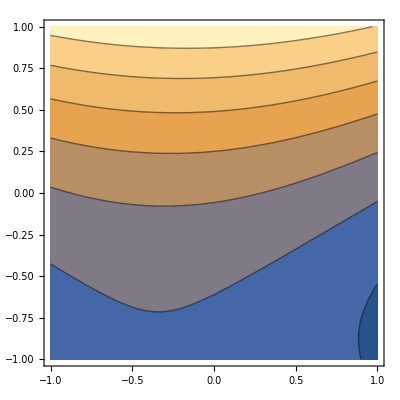

```mathematica
ContourPlot[stress[[1]][[1]],{xi,-1,1},{eta,-1,1}]
```

-Graphics-

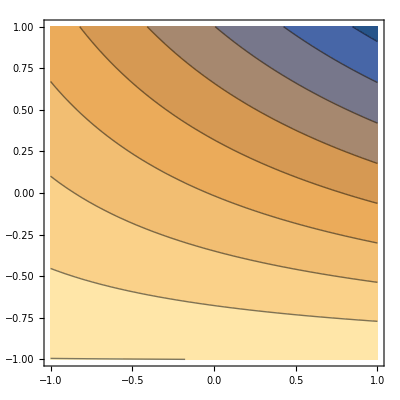

```mathematica
ContourPlot[stress[[1]][[1]],{xi,-1,1},{eta,-1,1}]
ContourPlot[stress[[2]][[1]],{xi,-1,1},{eta,-1,1}]
```

```mathematica
For[i=1,i≤Length[nnodes],i++,

];
```

```mathematica
topol
```

{{6,1,5,9,3,2,7,8,4},{5,16,21,9,11,18,14,7,12},{37,45,43,32,41,44,38,34,39},{43,40,30,32,42,35,31,38,36},{21,28,22,9,24,25,15,14,20},{6,9,22,17,8,15,19,10,13},{30,17,22,32,23,19,27,31,26},{32,22,28,37,27,25,33,34,29}}

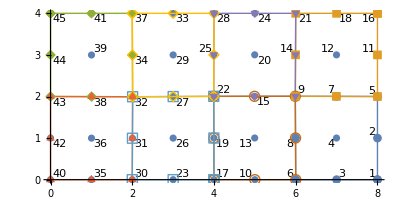

```mathematica
topol
```

{{6,1,5,9,3,2,7,8,4},{5,16,21,9,11,18,14,7,12},{37,45,43,32,41,44,38,34,39},{43,40,30,32,42,35,31,38,36},{21,28,22,9,24,25,15,14,20},{6,9,22,17,8,15,19,10,13},{30,17,22,32,23,19,27,31,26},{32,22,28,37,27,25,33,34,29}}

```mathematica
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
epsx=sol[[40 2-1]] D[psis[[1]],xi]+sol[[30 2-1]]D[psis[[2]],xi]+sol[[32 2-1]]D[psis[[3]],xi]+sol[[43 2-1]]D[psis[[4]],xi]+sol[[35 2-1]]D[psis[[5]],xi]+sol[[31 2-1]]D[psis[[6]],xi]+sol[[38 2-1]]D[psis[[7]],xi]+sol[[42 2-1]]D[psis[[8]],xi]+sol[[36 2-1]]D[psis[[9]],xi];
epsy=sol[[40 2]] D[psis[[1]],eta]+sol[[30 2]]D[psis[[2]],eta]+sol[[32 2]]D[psis[[3]],eta]+sol[[43 2]]D[psis[[4]],eta]+sol[[35 2]]D[psis[[5]],eta]+sol[[31 2]]D[psis[[6]],eta]+sol[[38 2]]D[psis[[7]],eta]+sol[[42 2]]D[psis[[8]],eta]+sol[[36 2]]D[psis[[9]],eta];
exy=sol[[40 2-1]] D[psis[[1]],eta]+sol[[30 2-1]]D[psis[[2]],eta]+sol[[32 2-1]]D[psis[[3]],eta]+sol[[43 2-1]]D[psis[[4]],eta]+sol[[35 2-1]]D[psis[[5]],eta]+sol[[31 2-1]]D[psis[[6]],eta]+sol[[38 2-1]]D[psis[[7]],eta]+sol[[42 2-1]]D[psis[[8]],eta]+sol[[36 2-1]]D[psis[[9]],eta];
exy+=sol[[40 2]] D[psis[[1]],xi]+sol[[30 2]]D[psis[[2]],xi]+sol[[32 2]]D[psis[[3]],xi]+sol[[43 2]]D[psis[[4]],xi]+sol[[35 2]]D[psis[[5]],xi]+sol[[31 2]]D[psis[[6]],xi]+sol[[38 2]]D[psis[[7]],xi]+sol[[42 2]]D[psis[[8]],xi]+sol[[36 2]]D[psis[[9]],xi];
CC=Table[0,{3},{3}];
CC[[1,1]]=young/(1-nu^2);
CC[[1,2]]=nu young/(1-nu^2);
CC[[2,1]]=CC[[1,2]];
CC[[2,2]]=CC[[1,1]];
CC[[3,3]]=young/(2 (1+nu));
s=CC.{epsx,epsy,exy}/.{xi->0,eta->0}
```

{-0.806992,22.1383,0.946604}

{{0,0},{10,0},{10,10},{0,10}}

{{2,1,4,3,2}}

-Graphics-

co = {{0,10},{10,10}}

(0
0
0
0
0.
33333.3
0.
16666.7)

{{4,3,2,1,4}}

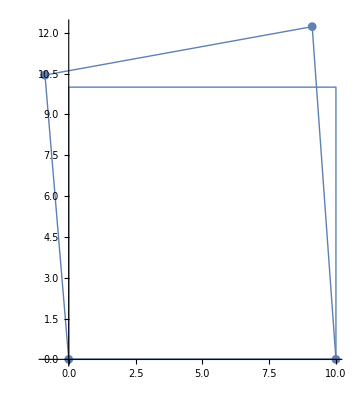

{0,0,0,0,0,0,0,0}

{7.87288×10^-32,1.11111×10^-15,1.64973×10^-31,2.22222×10^-15,-0.00111111,0.00277778,-0.00111111,0.000555556}

```mathematica
order=1;
young=30 10^6;
nu=0.;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol={{1,2,3,4}};
nnodes={{0,0},{10,0},{10,10},{0,10}}
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];



undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,2,{{10^12,1},{1,10^12}},{0,0}];

f[x_]:=1000 x;
diry=1;
FE=ContributeLineNewman[FE,f,order,nnodes,topol,4,3,1];

FE//MatrixForm

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=800;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotStyle->{Thick},PlotMarkers->Automatic];

Show[defplot,undefplot,PlotRange->All]

KE.sol-FE//Chop
sol
```

{{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,1,2,3,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2}}

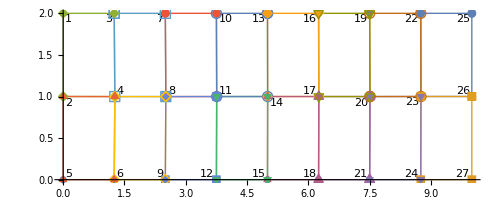

{{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{2,1,4,3,2},{4,3,2,1,4},{2,1,4,3,2}}

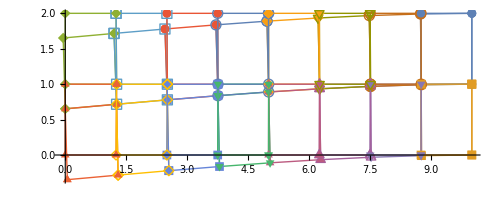

{-881.986,-765.635,-310.039}

{-306.434,-2.864,127.631}

{-501.437,-627.272,154.726}

{1412.92,1667.8,151.564}

{4200.47,4870.82,22.0833}

{-61.8441,33.8735,-314.131}

{4194.82,4866.47,-21.1568}

{4028.45,4659.6,-47.5726}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
order=1;
young=30 10^6;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp1els.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\reedybeamp1nodes.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,4}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords//Flatten[#,1]&

allcoordsNEW=MapThread[Part[#1,#2]&,{allcoords,ord}];
(*or*)
allcoordsNEW=Table[allcoords[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,27,25,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,1,1,{{1,1},{1,1}},{0,-100}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{0,-100}];
{KE,FE}=ApplyNodeBC[KE,FE,5,1,{{1,1},{1,1}},{0,-100}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=80;
deformed=(Flatten[nnodes]+scale sol);


tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[defplot,undefplot,PlotRange->All]

solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],young,nu][[1]];
stress[[1]]/.{xi->1,eta->1}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}

KE.sol-FE//Chop
```

```mathematica
topol
```

{{83,81,71,73,82,76,72,78,77},{85,83,73,75,84,78,74,80,79},{1,5,10,7,2,6,8,3,4},{5,15,18,10,9,16,14,6,11},{65,75,73,63,70,74,68,64,69},{61,63,73,71,62,68,72,66,67},{20,7,10,22,12,8,17,21,13},{10,18,27,22,14,23,24,17,19},{55,65,63,53,60,64,58,54,59},{63,61,51,53,62,56,52,58,57},{31,20,22,33,25,21,28,32,26},{22,27,35,33,24,30,34,28,29},{51,41,43,53,46,42,48,52,47},{55,53,43,45,54,48,44,50,49},{35,45,43,33,40,44,38,34,39},{43,41,31,33,42,36,32,38,37}}

```mathematica
nnodes
```

{{0,2},{0,1.5},{0.625,2},{0.628305,1.49981},{0,1},{0.631611,0.999613},{1.25,2},{1.25661,1.49961},{0,0.5},{1.26322,0.999226},{0.628305,0.499806},{1.875,2},{1.88122,1.49956},{1.25661,0.499613},{0,0},{0.625,0},{1.88744,0.999117},{1.25,0},{1.88122,0.499559},{2.5,2},{2.50583,1.4995},{2.51167,0.999009},{1.875,0},{2.50583,0.499505},{3.125,2},{3.12956,1.4996},{2.5,0},{3.13412,0.999206},{3.12956,0.499603},{3.125,0},{3.75,2},{3.75329,1.4997},{3.75658,0.999403},{3.75329,0.499701},{3.75,0},{4.375,2},{4.3774,1.49978},{4.37981,0.999564},{4.3774,0.499782},{4.375,0},{5,2},{5.00152,1.49986},{5.00304,0.999726},{5.00152,0.499863},{5,0},{5.625,2},{5.62715,1.49981},{5.6293,0.999613},{5.62715,0.499807},{5.625,0},{6.25,2},{6.25278,1.49975},{6.25556,0.999501},{6.25278,0.49975},{6.25,0},{6.875,2},{6.87828,1.49973},{6.88156,0.999451},{6.87828,0.499726},{6.875,0},{7.5,2},{7.50378,1.4997},{7.50756,0.999402},{7.50378,0.499701},{7.5,0},{8.125,2},{8.12814,1.49985},{8.13128,0.999706},{8.12814,0.499853},{8.125,0},{8.75,2},{8.7525,1.50001},{8.75501,1.00001},{8.7525,0.500005},{8.75,0},{9.375,2},{9.37625,1.5},{9.3775,1.00001},{9.37625,0.500003},{9.375,0},{10,2},{10,1.5},{10,1},{10,0.5},{10,0}}

{{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3},{2,5,1,8,4,7,3,6,2},{4,8,1,5,2,6,3,7,4},{2,5,1,8,4,7,3,6,2},{3,6,2,5,1,8,4,7,3}}

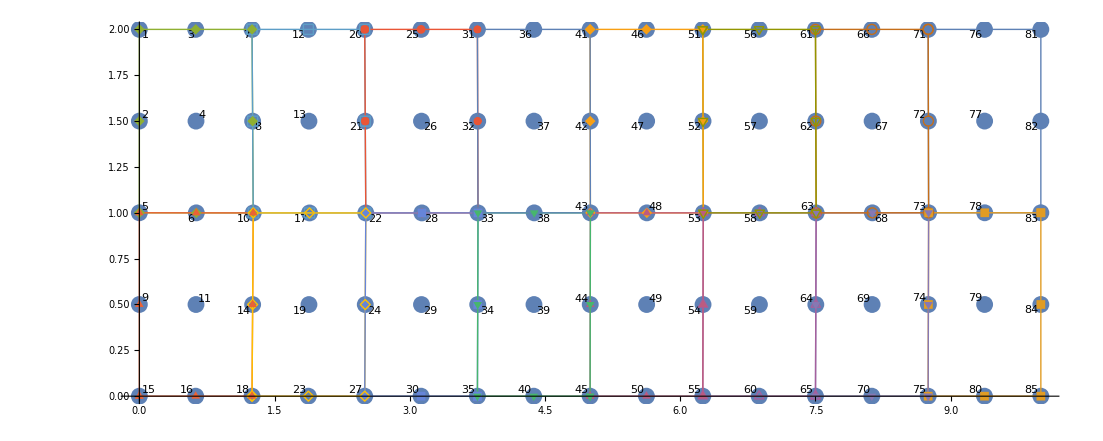

{{5,1,8,4,7,3,6,2,5},{5,2,6,3,7,4,8,1,5},{1,5,2,6,3,7,4,8,1},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{1,5,2,6,3,7,4,8,1},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{2,5,1,8,4,7,3,6,2},{5,2,6,3,7,4,8,1,5},{2,5,1,8,4,7,3,6,2},{5,1,8,4,7,3,6,2,5}}

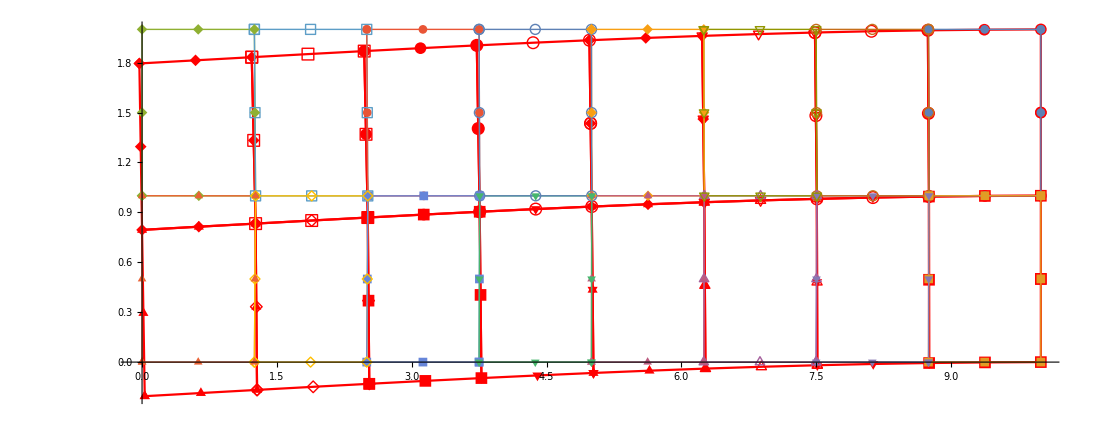

{-666.398,-793.7,-186.081}

{-365.004,-30.7153,139.377}

{-666.41,-793.711,186.08}

{1824.78,2103.15,166.889}

{5344.04,6087.,25.2455}

{-70.9172,37.8806,-349.985}

{5336.94,6081.4,-24.1907}

{5135.18,5838.47,-54.0792}

```mathematica
order=2;
young=30 10^6;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

topol=topol=Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elsp2-9-beam-redy.txt","Table"],1];
nnodes=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\nodesp2-9-beam-redy.txt","Table"][[;;,2;;]];
allcoords=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,9}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

allcoords2=Table[nnodes[[ topol[[i]][[j]] ]],{i,1,Length[topol]},{j,1,8}];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];

ord=FindCurvePath/@allcoords2//Flatten[#,1]&

allcoordsNEW=Table[allcoords2[[i,ord[[i]]]],{i,1,Length@ord}];

undefplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];

Show[nodeids,undefplot]

forcing=0.;
{KE,FE}=Assemble[allcoords,topol,order,forcing];

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,85,81,{{10^12,1},{1,10^12}},{0,0}];


{KE,FE}=ApplyNodeBC[KE,FE,5,1,{{1,1},{1,1}},{0,-300}];

sol=LinearSolve[KE,FE,Method->"Banded"];
scale=40;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords2]&@Flatten[nf@Flatten[allcoords2,1],1];

ord=FindCurvePath/@tabdeformed2//Flatten[#,1]&

allcoordsNEW=Table[tabdeformed2[[i,ord[[i]]]],{i,1,Length@ord}];

defplot=ListLinePlot[Tooltip[allcoordsNEW],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]

solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],30 10^6,0.30][[1]];
stress[[1]]/.{xi->0,eta->0}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}
```

```mathematica
Min[sol]
```

-0.00513177

```mathematica
topol
```

{{83,81,71,73,82,76,72,78,77},{85,83,73,75,84,78,74,80,79},{1,5,10,7,2,6,8,3,4},{5,15,18,10,9,16,14,6,11},{65,75,73,63,70,74,68,64,69},{61,63,73,71,62,68,72,66,67},{20,7,10,22,12,8,17,21,13},{10,18,27,22,14,23,24,17,19},{55,65,63,53,60,64,58,54,59},{63,61,51,53,62,56,52,58,57},{31,20,22,33,25,21,28,32,26},{22,27,35,33,24,30,34,28,29},{51,41,43,53,46,42,48,52,47},{55,53,43,45,54,48,44,50,49},{35,45,43,33,40,44,38,34,39},{43,41,31,33,42,36,32,38,37}}